```mathematica
Get["TransportFunctions/IntegrationTables.m"];
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

```mathematica
XDatam55p05=XDataCreation[{-0.055,0.005,0.},32]
```

{-0.055,-0.0530645,-0.051129,-0.0491935,-0.0472581,-0.0453226,-0.0433871,-0.0414516,-0.0395161,-0.0375806,-0.0356452,-0.0337097,-0.0317742,-0.0298387,-0.0279032,-0.0259677,-0.0240323,-0.0220968,-0.0201613,-0.0182258,-0.0162903,-0.0143548,-0.0124194,-0.0104839,-0.00854839,-0.0066129,-0.00467742,-0.00274194,-0.000806452,0.00112903,0.00306452,0.005}

### memoization

```mathematica
ClearAll[FitFuncMemoArith]
```

```mathematica
FitFuncMemoArith[
{b_,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_
]:=
FitFuncMemoArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]=
Reverse[IntegrationTableArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
FitFuncBinNormArith[bin_?NumericQ,{b_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_]:=FitFuncMemoArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec][[bin]]/Total[FitFuncMemoArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

# 90° no filter

Data 90° no Filter

```mathematica
t0=AbsoluteTime[];
ILLData90noFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14544 and 0.00554641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0346 and 0.0089511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.027142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0155816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94809 and 0.00517478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.036743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72955 and 0.0121513 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172851 and 0.000378833 for the integral and error estimates.

468.557663

### 450s

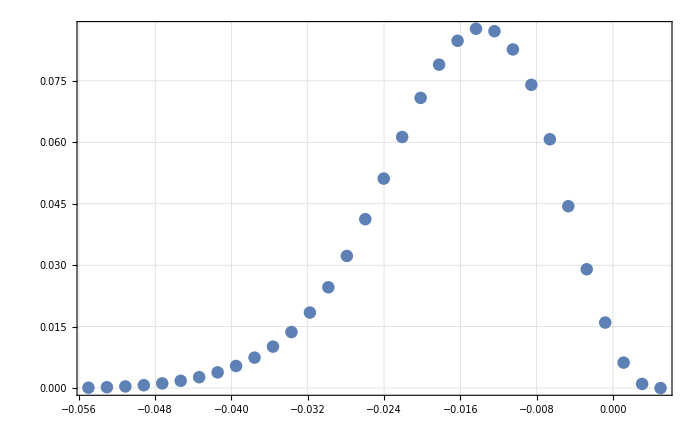

```mathematica
ListPlot[Transpose[{Reverse[XDatam55p05],ILLData90noFilter[[All,2]]}]]
```

```mathematica
(*Export["~/Dropbox/PhD/ElectronTransportSpectrum.txt",Transpose[{Reverse[XDatam55p05],ILLData90noFilter[[All,2]]}],"Table"]*)
```

~/Dropbox/PhD/ElectronTransportSpectrum.txt

Fits

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 17:40:44

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3336 and 0.00490097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14497 and 0.00544977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03401 and 0.00901064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0151044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0156212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3637 and 0.0104337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94881 and 0.00519046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172883 and 0.000377011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33421 and 0.00490258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14574 and 0.0054515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0354 and 0.00902454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.027273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94769 and 0.00525053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72907 and 0.0121454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06114 and 0.0366921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172789 and 0.000376794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.0049027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1458 and 0.00545164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0355 and 0.00902467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.0151064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0272729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0156197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1011 and 0.0141316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00525045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06111 and 0.0366914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.729 and 0.0121451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33418 and 0.0049025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14571 and 0.00545142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03533 and 0.00902446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272731 for the integral and error estimates.

$Aborted

2148.43893

### took 43751s or 12h

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
dBFit[[1]]["BestFitParameters"]
```

{b→0.0001}

### rA fit

```mathematica
t0=AbsoluteTime[];
drAFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2,1./2,1./2,1.,1/2.+1/2*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.003<b<0.003
},
{{b,-0.0001}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33501 and 0.00491574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14672 and 0.00554208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03696 and 0.00899823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4589 and 0.0150687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8606 and 0.0156764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0994 and 0.0141473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3593 and 0.0103892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94598 and 0.00516014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06067 and 0.0367192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72814 and 0.0121515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172693 and 0.000385474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33489 and 0.00491544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14658 and 0.00554175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00899792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3597 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94624 and 0.00516032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7283 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.000385516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33419 and 0.00491358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14568 and 0.00553973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03511 and 0.00899599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.015055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1016 and 0.0141504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94788 and 0.00516139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72935 and 0.0121555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06126 and 0.0367315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17282 and 0.000385773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3349 and 0.00491548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14659 and 0.00554179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03673 and 0.00899795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94621 and 0.0051603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72829 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000385512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3332 and 0.00488867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14444 and 0.00543444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03293 and 0.00899873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4546 and 0.0150521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.026995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8637 and 0.0156778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1043 and 0.0141541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3657 and 0.0104267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95016 and 0.00516288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06196 and 0.0367462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73081 and 0.0121602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17297 and 0.00038613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33493 and 0.00491554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03678 and 0.00899802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72825 and 0.0121519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94616 and 0.00516026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06073 and 0.0367204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000385503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33355 and 0.00491188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14487 and 0.00543538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03369 and 0.00899965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8631 and 0.015677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1034 and 0.0141528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3645 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94937 and 0.00516237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73031 and 0.0121586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06172 and 0.0367411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172918 and 0.000386007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33313 and 0.00488849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14436 and 0.00543424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03277 and 0.00899854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8638 and 0.015678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95032 and 0.00516299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06201 and 0.0367472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73091 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172981 and 0.000386155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3335 and 0.00491175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14481 and 0.00543524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03358 and 0.00899952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8632 and 0.0156771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1035 and 0.014153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3647 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94949 and 0.00516244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73038 and 0.0121588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06175 and 0.0367418 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172926 and 0.000386025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14571 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03517 and 0.00899606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72932 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172816 and 0.000385764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33402 and 0.00491312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14547 and 0.00544018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03474 and 0.00900093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1021 and 0.014151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94828 and 0.00516166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72961 and 0.0121563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06138 and 0.0367341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172846 and 0.000385836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33487 and 0.00491539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14655 and 0.00554169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00899786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3598 and 0.0103894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94629 and 0.00516035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72834 and 0.0121521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172714 and 0.000385524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00491459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14617 and 0.00554083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03598 and 0.00899704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4579 and 0.0150675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1006 and 0.0141489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3608 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94699 and 0.00516081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72878 and 0.0121536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06098 and 0.0367258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17276 and 0.000385633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33325 and 0.00488881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14451 and 0.00543459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03305 and 0.00899887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4547 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8636 and 0.0156777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1042 and 0.0141539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3655 and 0.0104266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95003 and 0.0051628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73073 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06192 and 0.0367454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172962 and 0.00038611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14431 and 0.00543414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.000386169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33376 and 0.00491244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00543597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03416 and 0.00900023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1028 and 0.014152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94888 and 0.00516205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72999 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06157 and 0.036738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172886 and 0.00038593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00491371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14574 and 0.00553987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03522 and 0.00899612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94777 and 0.00516132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172812 and 0.000385755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33367 and 0.0049122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14502 and 0.00543572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03396 and 0.00899998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.027128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0157297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1031 and 0.0141523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3641 and 0.010426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94909 and 0.00516219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73013 and 0.012158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06163 and 0.0367393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1729 and 0.000385963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00491393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14585 and 0.00554011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03541 and 0.00899635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00516119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72916 and 0.0121548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06117 and 0.0367295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000385725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33381 and 0.00491257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14521 and 0.0054396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00900036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1027 and 0.0141518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94877 and 0.00516197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72992 and 0.0121573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06153 and 0.0367372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172878 and 0.000385912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1443 and 0.00543413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.00038617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33311 and 0.00488845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14433 and 0.0054342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03273 and 0.00899849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95036 and 0.00516301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73094 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06202 and 0.0367474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172984 and 0.000386161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06107 and 0.0367276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14572 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03518 and 0.00899607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172815 and 0.000385763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00491389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14583 and 0.00554007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.00899631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94761 and 0.00516122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72918 and 0.0121549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0367298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172802 and 0.000385731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33374 and 0.00491238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14511 and 0.00543591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03411 and 0.00900017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94893 and 0.00516208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73003 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.000385938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33386 and 0.0049127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14527 and 0.00543973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03438 and 0.0090005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.0051619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72985 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172871 and 0.000385894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3347 and 0.00491492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14633 and 0.00554119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03626 and 0.00899738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8611 and 0.0156772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1002 and 0.0141484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3604 and 0.0103897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9467 and 0.00516062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7286 and 0.012153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06089 and 0.0367239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172741 and 0.000385588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33434 and 0.00491399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14588 and 0.00554018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03546 and 0.00899641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.015728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1012 and 0.0141498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94752 and 0.00516116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72912 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06115 and 0.0367292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172796 and 0.000385717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06108 and 0.0367277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.00491373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14575 and 0.0055399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03524 and 0.00899615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8619 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94775 and 0.0051613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172811 and 0.000385752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33416 and 0.0049135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14564 and 0.00553965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03505 and 0.00899591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3623 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94795 and 0.00516144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7294 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06128 and 0.0367319 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172824 and 0.000385783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33415 and 0.00491347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14563 and 0.00553962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03502 and 0.00899588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94797 and 0.00516145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72941 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172826 and 0.000385788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00491268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14526 and 0.00543971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03436 and 0.00900047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94867 and 0.00516191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72986 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172872 and 0.000385897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00491294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14538 and 0.00543999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.0150543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.015729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1023 and 0.0141513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3631 and 0.0104255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94844 and 0.00516176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72971 and 0.0121566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06143 and 0.0367351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172857 and 0.000385861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0049134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1456 and 0.00544047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03496 and 0.0089958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1018 and 0.0141506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3625 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94804 and 0.0051615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72946 and 0.0121558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0367325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17283 and 0.000385798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33451 and 0.00491442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14609 and 0.00554064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03583 and 0.00899686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1007 and 0.0141492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94714 and 0.00516091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06103 and 0.0367267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17277 and 0.000385657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33409 and 0.00491331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14556 and 0.00544038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03488 and 0.00899571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4567 and 0.0150547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1019 and 0.0141507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94812 and 0.00516155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7295 and 0.012156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172835 and 0.00038581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.0049132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03478 and 0.00899559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94822 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72957 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172842 and 0.000385826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.0049128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14532 and 0.00543984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03447 and 0.0090006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94857 and 0.00516184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72979 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172865 and 0.000385881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33388 and 0.00491276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1453 and 0.0054398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00900056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9486 and 0.00516186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72981 and 0.012157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06148 and 0.0367361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172867 and 0.000385885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00491324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14553 and 0.00544031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03483 and 0.00899564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94818 and 0.00516158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72954 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06135 and 0.0367334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172839 and 0.000385819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00491282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14533 and 0.00543986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03448 and 0.00900062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94855 and 0.00516183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72978 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172864 and 0.000385878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

22516.43869

### took 22516 s or 6,25h

```mathematica
drAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0000750132 | 0.0000470927 | 1.59288 | 0.121333

```mathematica
ChiList=Table[{b,
Total[(ILLData90noFilter[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi/2,0.2,1./2,1./2,1.,1/2.+1/2*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],{bin,1,32}])^2]},{b,drAFit[[2,1]]}];
```

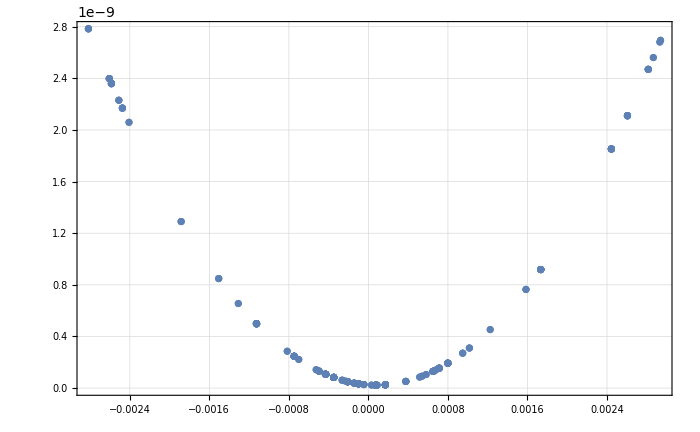

```mathematica
ListPlot[ChiList]
```

```mathematica
drAFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

0.750132

### Alpha Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dAlphaFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->5,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 00:27:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33444 and 0.00487253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.0089724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94748 and 0.00531564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0609 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33509 and 0.00487425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14676 and 0.00545655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03685 and 0.0089742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.015018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8601 and 0.0154271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3591 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94593 and 0.00514742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72811 and 0.0121574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06043 and 0.0367862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172697 and 0.000375918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14666 and 0.00545633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03668 and 0.00897399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94611 and 0.00514754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72822 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06049 and 0.0367874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000375945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33455 and 0.00487282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14606 and 0.00545501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03562 and 0.0089727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94719 and 0.00514047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14667 and 0.00545636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00897401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94609 and 0.00514753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72821 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06048 and 0.0367872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172708 and 0.000375942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00487111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14523 and 0.00545319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03419 and 0.00896316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4555 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94874 and 0.00531653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72989 and 0.0121632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0368042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172882 and 0.000376344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33504 and 0.00487412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14669 and 0.0054564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03674 and 0.00897405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94605 and 0.0051475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72819 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.036787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0048717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14552 and 0.00545382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03466 and 0.00897153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8618 and 0.0154293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00531616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0368008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172847 and 0.000376264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14517 and 0.00545306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03409 and 0.00896304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72996 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94884 and 0.00531661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.0368049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.00037636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00487153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14543 and 0.00545363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03451 and 0.00897135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8619 and 0.0154294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94837 and 0.00531627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0368018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172858 and 0.000376287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00487287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14609 and 0.00545506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03566 and 0.00897275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.361 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94715 and 0.00514044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000376106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03536 and 0.00897239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94749 and 0.00531565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.335 and 0.00487402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14664 and 0.00545629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00897395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4581 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8603 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00514756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0605 and 0.0367876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.00037595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33482 and 0.00487353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14641 and 0.00545577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03623 and 0.00897344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0271078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8606 and 0.0154277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3601 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94658 and 0.00514784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06063 and 0.0367904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72852 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000376017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33393 and 0.0048712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00487092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00545299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03403 and 0.00896297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9489 and 0.00531665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0368053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73 and 0.0121636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172893 and 0.000376369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00487202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14567 and 0.00545416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03493 and 0.00897186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8616 and 0.015429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94793 and 0.00531596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.036799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172829 and 0.000376221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.004873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14615 and 0.0054552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03577 and 0.00897288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8609 and 0.0154282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3608 and 0.010448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94704 and 0.00514037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06078 and 0.0367934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172771 and 0.000376089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03606 and 0.00897324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3603 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94675 and 0.00514795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72863 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06068 and 0.0367915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172751 and 0.000376043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14516 and 0.00545304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03407 and 0.00896302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94886 and 0.00531662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17289 and 0.000376363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14537 and 0.00545349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00896346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.010449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00531635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72973 and 0.0121627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06121 and 0.0368026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172866 and 0.000376306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00487219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14575 and 0.00545434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03508 and 0.00897204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94778 and 0.00531586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.061 and 0.036798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000376198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14591 and 0.00545468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.00897237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9475 and 0.00531566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7291 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1728 and 0.000376155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33458 and 0.0048729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1461 and 0.0054551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00897278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3609 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94713 and 0.00514043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.036794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172777 and 0.000376102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00487104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1452 and 0.00545311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03413 and 0.00896309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9488 and 0.00531658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72994 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0368046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172887 and 0.000376354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33394 and 0.00487121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33454 and 0.00487279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14605 and 0.00545499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0356 and 0.00897267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94722 and 0.00514049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72894 and 0.0121601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06083 and 0.0367946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000376116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03605 and 0.00897322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3604 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94676 and 0.00514796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06069 and 0.0367916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172752 and 0.000376045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00487222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14577 and 0.00545437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0351 and 0.00897207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.027109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94776 and 0.00531584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172817 and 0.000376194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

13770.33362

### took 13770s or 3,8h

```mathematica
dAlphaFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000916626 | 0.0000928275 | 9.87451 | 4.32917×10^-11

```mathematica
dAlphaFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

18.3325

```mathematica
ChiListAlphaFit=Table[{b,
Total[(ILLData90noFilter[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],{bin,1,32}])^2]},{b,dAlphaFit[[2,1]]}];
```

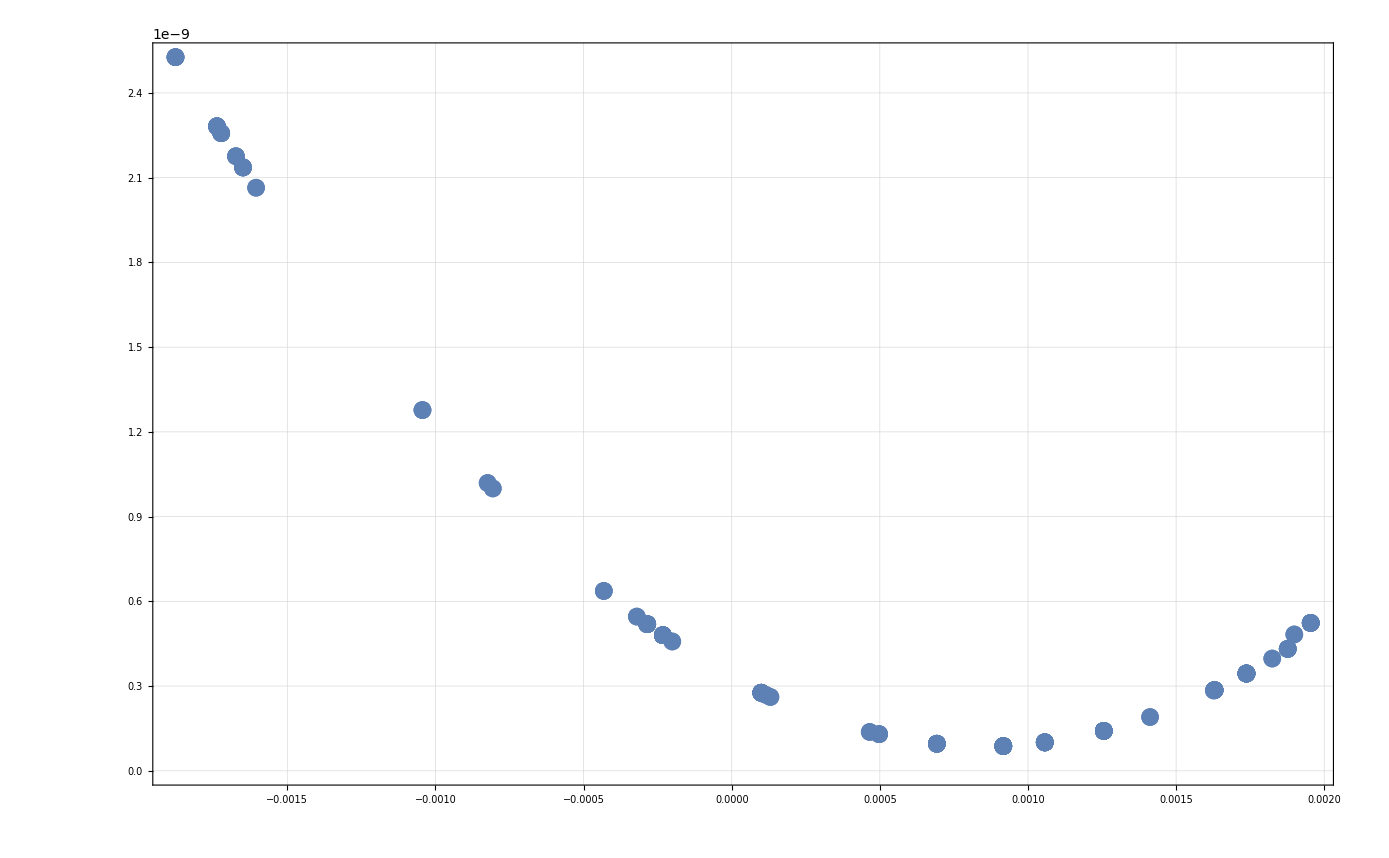

```mathematica
ListPlot[ChiListAlphaFit]
```

```mathematica
dAlphaChiInter=Interpolation[DeleteDuplicatesBy[ChiListAlphaFit,First],InterpolationOrder->2]
```

InterpolatingFunction[{{-0.00187738, 0.00195443}}, <>]

```mathematica
NMinimize[{dAlphaChiInter[x],-0.001<x<0.0015},x]
```

{8.64739×10^-11,{x→0.000860792}}

```mathematica
0.000860792/(5*10^-5)
```

17.2158

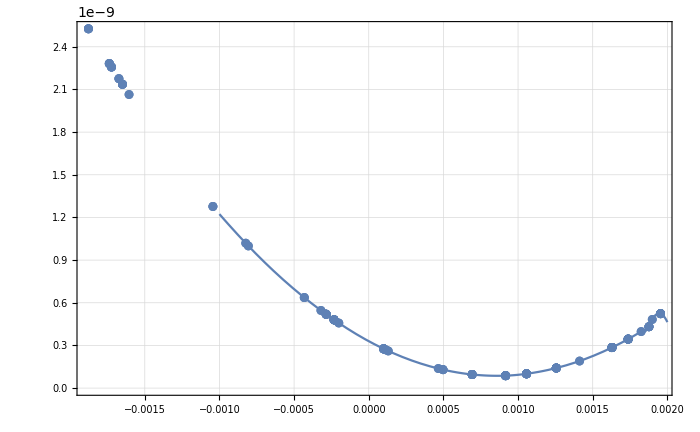

```mathematica
Show[
ListPlot[ChiListAlphaFit],
Plot[dAlphaChiInter[b],{b,-0.001,0.002}]
]
```

# 180° W filter

```mathematica
XDatam85p05=XDataCreation[{-0.085,0.005,0.},32]
```

{-0.085,-0.0820968,-0.0791935,-0.0762903,-0.0733871,-0.0704839,-0.0675806,-0.0646774,-0.0617742,-0.058871,-0.0559677,-0.0530645,-0.0501613,-0.0472581,-0.0443548,-0.0414516,-0.0385484,-0.0356452,-0.0327419,-0.0298387,-0.0269355,-0.0240323,-0.021129,-0.0182258,-0.0153226,-0.0124194,-0.00951613,-0.0066129,-0.00370968,-0.000806452,0.00209677,0.005}

Data

```mathematica
ILLData180WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_180°WFilter_Xm85p05_32Bins.txt","Table"]
```

{{0.005,0.},{0.00209677,0.000252048},{-0.000806452,0.0017237},{-0.00370968,0.00539714},{-0.0066129,0.0119853},{-0.00951613,0.0212666},{-0.0124194,0.0323628},{-0.0153226,0.0442408},{-0.0182258,0.0558807},{-0.021129,0.0662973},{-0.0240323,0.0747089},{-0.0269355,0.0804787},{-0.0298387,0.0832502},{-0.0327419,0.0828635},{-0.0356452,0.07949},{-0.0385484,0.0735347},{-0.0414516,0.0655851},{-0.0443548,0.0563155},{-0.0472581,0.046426},{-0.0501613,0.0365969},{-0.0530645,0.0274342},{-0.0559677,0.0195103},{-0.058871,0.0131508},{-0.0617742,0.00849305},{-0.0646774,0.00532177},{-0.0675806,0.00327343},{-0.0704839,0.00195778},{-0.0733871,0.00111995},{-0.0762903,0.000602935},{-0.0791935,0.000298793},{-0.0820968,0.000131299},{-0.085,0.0000498264}}

```mathematica
ILLData180WFilter=Transpose[{Table[i,{i,32}],ILLData180WFilter[[All,2]]}]
```

{{1,0.},{2,0.000252048},{3,0.0017237},{4,0.00539714},{5,0.0119853},{6,0.0212666},{7,0.0323628},{8,0.0442408},{9,0.0558807},{10,0.0662973},{11,0.0747089},{12,0.0804787},{13,0.0832502},{14,0.0828635},{15,0.07949},{16,0.0735347},{17,0.0655851},{18,0.0563155},{19,0.046426},{20,0.0365969},{21,0.0274342},{22,0.0195103},{23,0.0131508},{24,0.00849305},{25,0.00532177},{26,0.00327343},{27,0.00195778},{28,0.00111995},{29,0.000602935},{30,0.000298793},{31,0.000131299},{32,0.0000498264}}

```mathematica
t0=AbsoluteTime[];
ILLData180WFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam85p05,3]},{bin,1,Length[XDatam85p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41076 and 0.00245685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70297 and 0.00306239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95822 and 0.00345261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74613 and 0.00340646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05405 and 0.00242637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00177081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00138327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781715 and 0.000953262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633593 and 0.0000972753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926473 and 0.0000314074 for the integral and error estimates.

485.332008

### 450s

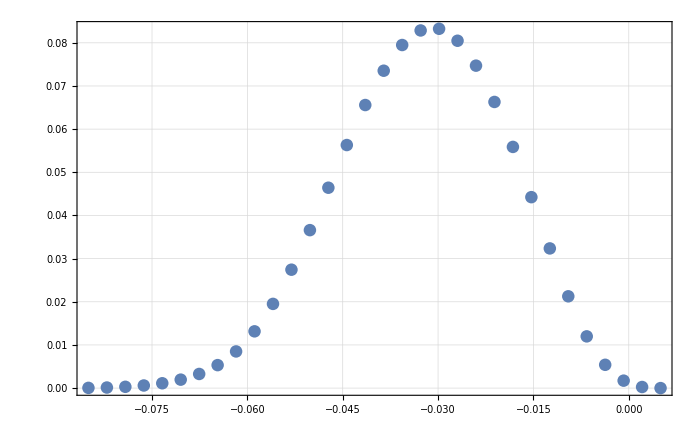

```mathematica
ListPlot[Transpose[{Reverse[XDatam85p05],ILLData180WFilter[[All,2]]}]]
```

```mathematica
(*Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_180°WFilter_Xm85p05_32Bins.txt", Transpose[{Reverse[XDatam85p05],ILLData180WFilter[[All,2]]}],"Table"];*)
```

### intermediate transport with lower alpha

```mathematica
XDatam20p05=XDataCreation[{-0.020,0.005,0.},32]
```

{-0.02,-0.0191935,-0.0183871,-0.0175806,-0.0167742,-0.0159677,-0.0151613,-0.0143548,-0.0135484,-0.0127419,-0.0119355,-0.011129,-0.0103226,-0.00951613,-0.00870968,-0.00790323,-0.00709677,-0.00629032,-0.00548387,-0.00467742,-0.00387097,-0.00306452,-0.00225806,-0.00145161,-0.000645161,0.00016129,0.000967742,0.00177419,0.00258065,0.0033871,0.00419355,0.005}

```mathematica
t0=AbsoluteTime[];
ILLDataBegin180WFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,22.5/180*Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam20p05,3]},{bin,1,Length[XDatam20p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0143046 and 0.0000194276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0951694 and 0.000152021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.13574 and 0.000200873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.262044 and 0.000324667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.6516 and 0.000676505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.881861 and 0.00168525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.18708 and 0.00179972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56615 and 0.00167852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67259 and 0.00312167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.24748 and 0.00327098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78208 and 0.00335799 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.31509 and 0.00311514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.890147 and 0.00291334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.552419 and 0.00287134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.11217 and 0.112134 for the integral and error estimates.

496.902993

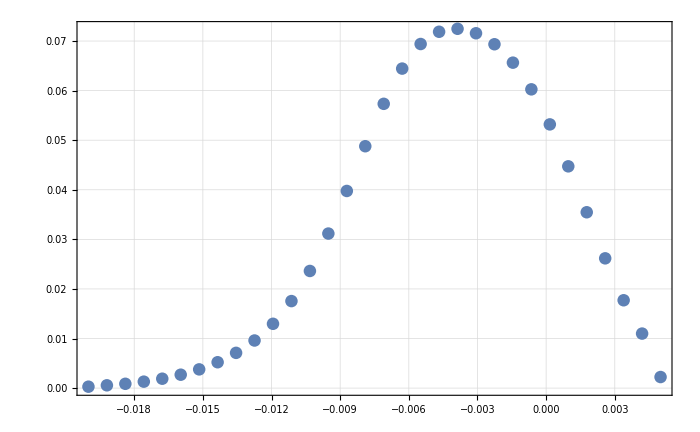

```mathematica
ListPlot[Transpose[{Reverse[XDatam20p05],ILLDataBegin180WFilter[[All,2]]}]]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_22,5°WFilter_Xm20p05_32Bins.txt",Transpose[{Reverse[XDatam20p05],ILLDataBegin180WFilter[[All,2]]}],"Table"];
```

Fits (still partly only copied from 90° fits)

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 17:40:44

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3336 and 0.00490097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14497 and 0.00544977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03401 and 0.00901064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0151044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0156212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3637 and 0.0104337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94881 and 0.00519046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172883 and 0.000377011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33421 and 0.00490258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14574 and 0.0054515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0354 and 0.00902454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.027273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94769 and 0.00525053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72907 and 0.0121454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06114 and 0.0366921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172789 and 0.000376794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.0049027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1458 and 0.00545164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0355 and 0.00902467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.0151064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0272729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0156197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1011 and 0.0141316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00525045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06111 and 0.0366914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.729 and 0.0121451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33418 and 0.0049025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14571 and 0.00545142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03533 and 0.00902446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272731 for the integral and error estimates.

$Aborted

2148.43893

### took 43751s or 12h

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
dBFit[[1]]["BestFitParameters"]
```

{b→0.0001}

### rA fit

```mathematica
t0=AbsoluteTime[];
drAFit=Reap[NonlinearModelFit[
ILLData180WFilter,
{
FitFuncBinNormArith[bin,{b,Pi,0.2,1.,1.,2.,1.+10^-4},{0.01,0.035,0.,0.,0.},XDatam85p05,3],
-0.003<b<0.003
},
{{b,0.0001}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41083 and 0.00246741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70304 and 0.00306209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95835 and 0.00346338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74622 and 0.00343003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0541 and 0.00242463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62627 and 0.00176986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18966 and 0.00136572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781753 and 0.000949502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633637 and 0.0000957935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926608 and 0.0000310169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41145 and 0.00244613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70359 and 0.00306272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95806 and 0.00346304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7457 and 0.0034292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05329 and 0.00241975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62547 and 0.00176354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18895 and 0.00136487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78121 and 0.000951346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633073 and 0.0000957119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925753 and 0.0000309885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4115 and 0.00244618 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70364 and 0.00306277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95804 and 0.00346301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74566 and 0.00342913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05323 and 0.00241967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6254 and 0.00176347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18889 and 0.0013648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781168 and 0.000951293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633029 and 0.0000957056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925687 and 0.0000309863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41142 and 0.00244609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70357 and 0.00306269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95807 and 0.00346306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74572 and 0.00342924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05333 and 0.00241981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62551 and 0.00176359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18898 and 0.00136491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781237 and 0.000951379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.06331 and 0.0000957159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925795 and 0.0000309899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41094 and 0.00246753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70313 and 0.00306219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9583 and 0.00346332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74614 and 0.00342989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05397 and 0.00242445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62613 and 0.00176679 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18954 and 0.00136558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781663 and 0.000949391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633543 and 0.00009578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926466 and 0.0000310122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41143 and 0.0024461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70357 and 0.0030627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95807 and 0.00346305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74572 and 0.00342923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05332 and 0.00241979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62549 and 0.00176357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18897 and 0.0013649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781229 and 0.00095137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633093 and 0.0000957148 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925783 and 0.0000309895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41025 and 0.00246677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70253 and 0.0030615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95862 and 0.00346369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74671 and 0.00343079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05485 and 0.00242181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19032 and 0.00136651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62702 and 0.0017739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782254 and 0.000950125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634157 and 0.0000958688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927397 and 0.0000310431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41145 and 0.00244612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70359 and 0.00306272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7457 and 0.00342921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95806 and 0.00346304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0533 and 0.00241976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18895 and 0.00136488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62547 and 0.00176355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781214 and 0.000951351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633077 and 0.0000957126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092576 and 0.0000309887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41049 and 0.00246703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70274 and 0.00306174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95851 and 0.00346356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74651 and 0.00343048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05455 and 0.0024252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62671 and 0.00177356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19005 and 0.00136619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78205 and 0.000949871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633945 and 0.0000958381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927076 and 0.0000310324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4102 and 0.00246671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70249 and 0.00306145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95864 and 0.00346371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74675 and 0.00343086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05491 and 0.00242189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62708 and 0.00177397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19038 and 0.00136658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782296 and 0.000950177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634201 and 0.0000958751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927462 and 0.0000310453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41145 and 0.00244613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70359 and 0.00306272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95806 and 0.00346304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7457 and 0.0034292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05329 and 0.00241975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62547 and 0.00176354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18895 and 0.00136487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78121 and 0.000951346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633073 and 0.0000957119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925753 and 0.0000309885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41042 and 0.00246696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70269 and 0.00306168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95854 and 0.0034636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74656 and 0.00343057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05463 and 0.00242152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62679 and 0.00177365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19012 and 0.00136628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782104 and 0.000949938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634001 and 0.0000958462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092716 and 0.0000310352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41095 and 0.00246755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70315 and 0.00306221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95829 and 0.00346331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74612 and 0.00342987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05394 and 0.00242442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62611 and 0.00176677 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.00136556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781647 and 0.000949371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633527 and 0.0000957776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926441 and 0.0000310114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41081 and 0.00246739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70303 and 0.00306207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95836 and 0.00346339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74624 and 0.00343005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05412 and 0.00242466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62629 and 0.00176989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18968 and 0.00136575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781767 and 0.00094952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633651 and 0.0000957956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092663 and 0.0000310176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41142 and 0.00246806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70355 and 0.00306267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95808 and 0.00346306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74574 and 0.00342926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05335 and 0.00241983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.189 and 0.00136493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62553 and 0.00176361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78125 and 0.000951396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633114 and 0.0000957179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925816 and 0.0000309906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41122 and 0.00246784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70338 and 0.00306247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95817 and 0.00346317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7459 and 0.00342952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05361 and 0.00242016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62578 and 0.0017639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18922 and 0.0013652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781422 and 0.000951609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633292 and 0.0000957437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926086 and 0.0000309996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41029 and 0.00246681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70257 and 0.00306154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9586 and 0.00346367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74668 and 0.00343075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0548 and 0.00242174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62697 and 0.00177385 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19028 and 0.00136646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782222 and 0.000950085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634124 and 0.0000958639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927346 and 0.0000310414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41017 and 0.00246668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70247 and 0.00306143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95865 and 0.00346373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74677 and 0.00343089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05495 and 0.00242193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62712 and 0.00177401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19041 and 0.00136661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782319 and 0.000950205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634225 and 0.0000958785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927499 and 0.0000310465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41062 and 0.00246717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70285 and 0.00306187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95845 and 0.00346349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7464 and 0.00343031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05438 and 0.00242498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62654 and 0.00177336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1899 and 0.00136601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781937 and 0.000949731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633828 and 0.0000958212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926898 and 0.0000310265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.411 and 0.0024676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70319 and 0.00306225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95827 and 0.00346329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74608 and 0.00342981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05389 and 0.00242435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62606 and 0.00176421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18947 and 0.0013655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781609 and 0.000949324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633487 and 0.0000957719 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926381 and 0.0000310094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41057 and 0.00246712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70281 and 0.00306182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95847 and 0.00346352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74644 and 0.00343037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05444 and 0.00242506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62661 and 0.00177343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18996 and 0.00136608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781978 and 0.000949782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633871 and 0.0000958273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926962 and 0.0000310287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41097 and 0.00246757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70317 and 0.00306223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95828 and 0.0034633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7461 and 0.00342984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05392 and 0.00242439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62609 and 0.00176425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1895 and 0.00136553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781629 and 0.000949348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633508 and 0.0000957749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926413 and 0.0000310104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41069 and 0.00246725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70291 and 0.00306194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74635 and 0.00343022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95841 and 0.00346345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05429 and 0.00242487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18982 and 0.00136592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62646 and 0.00176846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781878 and 0.000949657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633766 and 0.0000958122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926804 and 0.0000310234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41017 and 0.00246668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70247 and 0.00306142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95865 and 0.00346373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74677 and 0.0034309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05495 and 0.00242194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62712 and 0.00177401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19041 and 0.00136662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78232 and 0.000950207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634226 and 0.0000958788 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927501 and 0.0000310466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41019 and 0.0024667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70248 and 0.00306144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95864 and 0.00346372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74676 and 0.00343087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05493 and 0.00242191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6271 and 0.00177399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19039 and 0.00136659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782306 and 0.000950189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634211 and 0.0000958766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927478 and 0.0000310458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41112 and 0.00246773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7033 and 0.00306238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95821 and 0.00346322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74598 and 0.00342965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05373 and 0.00242414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6259 and 0.00176403 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18933 and 0.00136533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781502 and 0.000951709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633376 and 0.0000957558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926213 and 0.0000310038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4109 and 0.00246749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7031 and 0.00306216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74616 and 0.00342994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05401 and 0.00242451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62618 and 0.00176976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18958 and 0.00136563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781691 and 0.000949426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633573 and 0.0000957843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926511 and 0.0000310137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41104 and 0.00246764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70322 and 0.0030623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95825 and 0.00346327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74605 and 0.00342975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05383 and 0.00242428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62601 and 0.00176415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18942 and 0.00136544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781573 and 0.000949279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.063345 and 0.0000957665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926324 and 0.0000310075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41062 and 0.00246718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70286 and 0.00306187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7464 and 0.00343031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95845 and 0.00346349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05438 and 0.00242498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62654 and 0.00177336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1899 and 0.00136601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781936 and 0.00094973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633827 and 0.000095821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926896 and 0.0000310265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05403 and 0.00242453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6262 and 0.00176978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1896 and 0.00136565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781704 and 0.000949441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633586 and 0.0000957861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926531 and 0.0000310143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41075 and 0.00246732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70297 and 0.003062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95839 and 0.00346342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74629 and 0.00343014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05421 and 0.00242477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62638 and 0.00176837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18975 and 0.00136584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781824 and 0.00094959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.063371 and 0.0000958041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926719 and 0.0000310206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74617 and 0.00342995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05402 and 0.00242453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00136564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00176978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781701 and 0.000949437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633582 and 0.0000957857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926526 and 0.0000310142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41128 and 0.00246791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70343 and 0.00306254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95814 and 0.00346314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74585 and 0.00342944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05353 and 0.00242006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6257 and 0.00176381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18915 and 0.00136512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781368 and 0.000951542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633237 and 0.0000957356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926001 and 0.0000309968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41106 and 0.00246766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70324 and 0.00306231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95825 and 0.00346326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74604 and 0.00342973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05381 and 0.00242425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62599 and 0.00176413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00136542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78156 and 0.000949263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633436 and 0.0000957645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926304 and 0.0000310068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41105 and 0.00246766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70323 and 0.00306231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95825 and 0.00346326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74604 and 0.00342974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05382 and 0.00242426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62599 and 0.00176413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00136542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781563 and 0.000949266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633439 and 0.0000957649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926308 and 0.0000310069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41094 and 0.00246753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70314 and 0.0030622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9583 and 0.00346332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74613 and 0.00342989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05396 and 0.00242445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62612 and 0.00176679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18954 and 0.00136558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781659 and 0.000949386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633539 and 0.0000957794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092646 and 0.000031012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41073 and 0.0024673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70295 and 0.00306198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9584 and 0.00346343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74631 and 0.00343016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05424 and 0.0024248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6264 and 0.0017684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18978 and 0.00136586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781842 and 0.000949613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633729 and 0.0000958069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926748 and 0.0000310215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41091 and 0.0024675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70311 and 0.00306216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95831 and 0.00346334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74616 and 0.00342993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.054 and 0.0024245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62617 and 0.00176975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18957 and 0.00136562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781688 and 0.000949421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633569 and 0.0000957837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926505 and 0.0000310135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4109 and 0.00246748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7031 and 0.00306215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74617 and 0.00342994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05402 and 0.00242452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00176977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00136564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781697 and 0.000949433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633579 and 0.0000957852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092652 and 0.000031014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41074 and 0.00246731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70296 and 0.00306199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95839 and 0.00346343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7463 and 0.00343015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05422 and 0.00242478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62639 and 0.00176838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18976 and 0.00136585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781832 and 0.000949601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633719 and 0.0000958054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926732 and 0.000031021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05403 and 0.00242453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00176978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00136565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781703 and 0.00094944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633584 and 0.0000957859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926529 and 0.0000310143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41078 and 0.00246736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.703 and 0.00306204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95837 and 0.0034634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74627 and 0.0034301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05417 and 0.00242471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62633 and 0.00176832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18972 and 0.00136579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781796 and 0.000949556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633682 and 0.0000958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926676 and 0.0000310192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41071 and 0.00246728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70294 and 0.00306197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9584 and 0.00346344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74632 and 0.00343018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05425 and 0.00242482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18979 and 0.00136588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62642 and 0.00176842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781853 and 0.000949627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633741 and 0.0000958086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926766 and 0.0000310221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00246743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70306 and 0.00306211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00242459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62624 and 0.00176983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18964 and 0.0013657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781735 and 0.00094948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633618 and 0.0000957908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092658 and 0.000031016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41108 and 0.00246769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70326 and 0.00306234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95823 and 0.00346324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74601 and 0.0034297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05378 and 0.00242421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62595 and 0.00176409 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18937 and 0.00136538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781536 and 0.000949233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633412 and 0.0000957609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926267 and 0.0000310056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41088 and 0.00246746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70308 and 0.00306213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95833 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05404 and 0.00242455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62621 and 0.0017698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18961 and 0.00136566 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781712 and 0.000949452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633595 and 0.0000957874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926544 and 0.0000310148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00246743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70306 and 0.00306211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05407 and 0.00242459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62624 and 0.00176983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18964 and 0.0013657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781735 and 0.00094948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633618 and 0.0000957908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926579 and 0.0000310159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41084 and 0.00246742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70305 and 0.0030621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05409 and 0.00242461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62625 and 0.00176985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18965 and 0.00136571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781743 and 0.00094949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633627 and 0.000095792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926592 and 0.0000310164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05403 and 0.00242454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1896 and 0.00136565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6262 and 0.00176978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781705 and 0.000949443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633587 and 0.0000957863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926532 and 0.0000310144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41076 and 0.00246733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70298 and 0.00306202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95838 and 0.00346341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74628 and 0.00343012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05419 and 0.00242474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62636 and 0.00176835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18974 and 0.00136582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781813 and 0.000949577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633699 and 0.0000958025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926702 and 0.00003102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41077 and 0.00246734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70298 and 0.00306202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95838 and 0.00346341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74628 and 0.00343011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05419 and 0.00242474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62635 and 0.00176835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18973 and 0.00136581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781809 and 0.000949572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633695 and 0.0000958019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926696 and 0.0000310198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41084 and 0.00246742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70305 and 0.0030621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05409 and 0.00242461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62625 and 0.00176985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18965 and 0.00136571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781743 and 0.00094949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633626 and 0.000095792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926592 and 0.0000310164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41075 and 0.00246732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70297 and 0.00306201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95838 and 0.00346342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74629 and 0.00343013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0542 and 0.00242476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62637 and 0.00176837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18975 and 0.00136583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781821 and 0.000949586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633707 and 0.0000958037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926714 and 0.0000310204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00246743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70306 and 0.00306211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00242459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62624 and 0.00176983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18964 and 0.0013657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781735 and 0.00094948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633618 and 0.0000957908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092658 and 0.000031016 for the integral and error estimates.

25806.31947

### took 25806 s or 7,2h

```mathematica
drAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000011726 | 0.0000119401 | 0.982072 | 0.333667

```mathematica
drAFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

0.11726

### Alpha Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dAlphaFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->5,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 00:27:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33444 and 0.00487253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.0089724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94748 and 0.00531564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0609 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33509 and 0.00487425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14676 and 0.00545655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03685 and 0.0089742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.015018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8601 and 0.0154271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3591 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94593 and 0.00514742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72811 and 0.0121574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06043 and 0.0367862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172697 and 0.000375918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14666 and 0.00545633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03668 and 0.00897399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94611 and 0.00514754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72822 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06049 and 0.0367874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000375945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33455 and 0.00487282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14606 and 0.00545501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03562 and 0.0089727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94719 and 0.00514047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14667 and 0.00545636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00897401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94609 and 0.00514753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72821 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06048 and 0.0367872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172708 and 0.000375942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00487111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14523 and 0.00545319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03419 and 0.00896316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4555 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94874 and 0.00531653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72989 and 0.0121632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0368042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172882 and 0.000376344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33504 and 0.00487412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14669 and 0.0054564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03674 and 0.00897405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94605 and 0.0051475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72819 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.036787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0048717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14552 and 0.00545382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03466 and 0.00897153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8618 and 0.0154293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00531616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0368008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172847 and 0.000376264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14517 and 0.00545306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03409 and 0.00896304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72996 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94884 and 0.00531661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.0368049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.00037636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00487153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14543 and 0.00545363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03451 and 0.00897135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8619 and 0.0154294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94837 and 0.00531627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0368018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172858 and 0.000376287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00487287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14609 and 0.00545506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03566 and 0.00897275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.361 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94715 and 0.00514044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000376106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03536 and 0.00897239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94749 and 0.00531565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.335 and 0.00487402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14664 and 0.00545629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00897395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4581 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8603 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00514756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0605 and 0.0367876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.00037595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33482 and 0.00487353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14641 and 0.00545577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03623 and 0.00897344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0271078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8606 and 0.0154277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3601 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94658 and 0.00514784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06063 and 0.0367904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72852 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000376017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33393 and 0.0048712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00487092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00545299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03403 and 0.00896297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9489 and 0.00531665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0368053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73 and 0.0121636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172893 and 0.000376369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00487202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14567 and 0.00545416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03493 and 0.00897186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8616 and 0.015429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94793 and 0.00531596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.036799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172829 and 0.000376221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.004873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14615 and 0.0054552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03577 and 0.00897288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8609 and 0.0154282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3608 and 0.010448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94704 and 0.00514037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06078 and 0.0367934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172771 and 0.000376089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03606 and 0.00897324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3603 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94675 and 0.00514795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72863 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06068 and 0.0367915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172751 and 0.000376043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14516 and 0.00545304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03407 and 0.00896302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94886 and 0.00531662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17289 and 0.000376363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14537 and 0.00545349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00896346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.010449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00531635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72973 and 0.0121627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06121 and 0.0368026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172866 and 0.000376306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00487219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14575 and 0.00545434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03508 and 0.00897204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94778 and 0.00531586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.061 and 0.036798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000376198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14591 and 0.00545468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.00897237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9475 and 0.00531566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7291 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1728 and 0.000376155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33458 and 0.0048729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1461 and 0.0054551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00897278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3609 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94713 and 0.00514043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.036794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172777 and 0.000376102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00487104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1452 and 0.00545311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03413 and 0.00896309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9488 and 0.00531658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72994 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0368046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172887 and 0.000376354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33394 and 0.00487121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33454 and 0.00487279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14605 and 0.00545499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0356 and 0.00897267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94722 and 0.00514049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72894 and 0.0121601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06083 and 0.0367946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000376116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03605 and 0.00897322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3604 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94676 and 0.00514796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06069 and 0.0367916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172752 and 0.000376045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00487222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14577 and 0.00545437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0351 and 0.00897207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.027109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94776 and 0.00531584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172817 and 0.000376194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

13770.33362

### took 13770s or 3,8h

```mathematica
dAlphaFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000916626 | 0.0000928275 | 9.87451 | 4.32917×10^-11

```mathematica
dAlphaFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

18.3325

```mathematica
ChiListAlphaFit=Table[{b,
Total[(ILLData90noFilter[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],{bin,1,32}])^2]},{b,dAlphaFit[[2,1]]}];
```

```mathematica
ListPlot[ChiListAlphaFit]
```

-Graphics-

```mathematica
dAlphaChiInter=Interpolation[DeleteDuplicatesBy[ChiListAlphaFit,First],InterpolationOrder->2]
```

InterpolatingFunction[{{-0.00187738, 0.00195443}}, <>]

```mathematica
NMinimize[{dAlphaChiInter[x],-0.001<x<0.0015},x]
```

{8.64739×10^-11,{x→0.000860792}}

```mathematica
0.000860792/(5*10^-5)
```

17.2158

```mathematica
Show[
ListPlot[ChiListAlphaFit],
Plot[dAlphaChiInter[b],{b,-0.001,0.002}]
]
```

-Graphics-

Bfield ramp 180°

```mathematica
?D1stBPolyGrad
```

Global`D1stBPolyGrad

D1stBPolyGrad[p_,alpha_,th0_,BRxB_,rRxB_,y0_,R_,G1_,G2_]:=(p alpha fReduced[th0,rRxB])/(c BpolynomGrad[y0,BRxB,R,G1,G2])

```mathematica
Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,{0.2,0.4,0.6,0.8,1,1.2}}],0.001]
```

{0.104,0.057,0.041,0.033,0.029,0.026}

```mathematica
Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,{0.2,0.4,0.6,0.8,1,1.2}}],0.01]*0.8
```

{0.08,0.048,0.032,0.024,0.024,0.024}

```mathematica
XDataBRamp200=XDataCreation[{-0.075,0.005,0.},32]
```

{-0.075,-0.0724194,-0.0698387,-0.0672581,-0.0646774,-0.0620968,-0.0595161,-0.0569355,-0.0543548,-0.0517742,-0.0491935,-0.0466129,-0.0440323,-0.0414516,-0.038871,-0.0362903,-0.0337097,-0.031129,-0.0285484,-0.0259677,-0.0233871,-0.0208065,-0.0182258,-0.0156452,-0.0130645,-0.0104839,-0.00790323,-0.00532258,-0.00274194,-0.00016129,0.00241935,0.005}

```mathematica
XDataBRamp400=XDataCreation[{-0.043,0.005,0.},32]
```

{-0.043,-0.0414516,-0.0399032,-0.0383548,-0.0368065,-0.0352581,-0.0337097,-0.0321613,-0.0306129,-0.0290645,-0.0275161,-0.0259677,-0.0244194,-0.022871,-0.0213226,-0.0197742,-0.0182258,-0.0166774,-0.015129,-0.0135806,-0.0120323,-0.0104839,-0.00893548,-0.0073871,-0.00583871,-0.00429032,-0.00274194,-0.00119355,0.000354839,0.00190323,0.00345161,0.005}

```mathematica
XDataBRamp600=XDataCreation[{-0.027,0.005,0.},32]
```

{-0.027,-0.0259677,-0.0249355,-0.0239032,-0.022871,-0.0218387,-0.0208065,-0.0197742,-0.0187419,-0.0177097,-0.0166774,-0.0156452,-0.0146129,-0.0135806,-0.0125484,-0.0115161,-0.0104839,-0.00945161,-0.00841935,-0.0073871,-0.00635484,-0.00532258,-0.00429032,-0.00325806,-0.00222581,-0.00119355,-0.00016129,0.000870968,0.00190323,0.00293548,0.00396774,0.005}

```mathematica
XDataBRamp800=XDataCreation[{-0.019,0.005,0.},32]
```

{-0.019,-0.0182258,-0.0174516,-0.0166774,-0.0159032,-0.015129,-0.0143548,-0.0135806,-0.0128065,-0.0120323,-0.0112581,-0.0104839,-0.00970968,-0.00893548,-0.00816129,-0.0073871,-0.0066129,-0.00583871,-0.00506452,-0.00429032,-0.00351613,-0.00274194,-0.00196774,-0.00119355,-0.000419355,0.000354839,0.00112903,0.00190323,0.00267742,0.00345161,0.00422581,0.005}

```mathematica
XDataBRamp1000=XDataCreation[{-0.019,0.005,0.},32]
```

{-0.019,-0.0182258,-0.0174516,-0.0166774,-0.0159032,-0.015129,-0.0143548,-0.0135806,-0.0128065,-0.0120323,-0.0112581,-0.0104839,-0.00970968,-0.00893548,-0.00816129,-0.0073871,-0.0066129,-0.00583871,-0.00506452,-0.00429032,-0.00351613,-0.00274194,-0.00196774,-0.00119355,-0.000419355,0.000354839,0.00112903,0.00190323,0.00267742,0.00345161,0.00422581,0.005}

```mathematica
XDataBRamp1200=XDataCreation[{-0.019,0.005,0.},32]
```

{-0.019,-0.0182258,-0.0174516,-0.0166774,-0.0159032,-0.015129,-0.0143548,-0.0135806,-0.0128065,-0.0120323,-0.0112581,-0.0104839,-0.00970968,-0.00893548,-0.00816129,-0.0073871,-0.0066129,-0.00583871,-0.00506452,-0.00429032,-0.00351613,-0.00274194,-0.00196774,-0.00119355,-0.000419355,0.000354839,0.00112903,0.00190323,0.00267742,0.00345161,0.00422581,0.005}

### check first one separately

```mathematica
t0=AbsoluteTime[];
ILLData180WFilterBRamp1=
Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp200,4]},{bin,1,Length[XDataBRamp200]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.12713 and 0.0000679597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0809327 and 0.0000196856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0499009 and 7.35133×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294177 and 4.49118×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.195643 and 0.0000647179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296762 and 0.000130372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.632186 and 0.000361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.440209 and 0.000220842 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15403 and 0.000961266 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872711 and 0.000637861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78793 and 0.0016734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46401 and 0.00133048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10896 and 0.00197165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41076 and 0.00245688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67397 and 0.00285532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87933 and 0.0033746 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.016 and 0.00317147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06784 and 0.00308408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.0286 and 0.00333075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89947 and 0.00350243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68539 and 0.00327995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39778 and 0.00238263 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05405 and 0.00242636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67482 and 0.00192871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.2855 and 0.00152108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.58198 and 0.0007035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912026 and 0.000996358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319156 and 0.000293336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142547 and 0.000144073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674625 and 0.0000237034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.045494 and 0.0000870671 for the integral and error estimates.

879.35549

### 600s

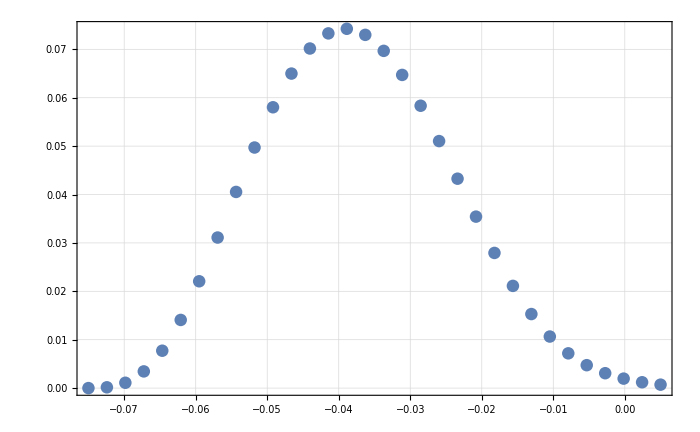

```mathematica
ListPlot[Transpose[{XDataBRamp200,ILLData180WFilterBRamp1[[All,2]]}]]
```

```mathematica
BRamps={0.4,0.6,0.8,1.};
```

```mathematica
XDataBRampList={XDataBRamp400,XDataBRamp600,XDataBRamp800,XDataBRamp1000};
```

```mathematica
t0=AbsoluteTime[];
ILLData180WFilterBRamp=
Table[
Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,BRamps[[BRampi]],1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampList[[BRampi]],4]},{bin,1,Length[XDataBRampList[[BRampi]]]}],
{BRampi,1,4}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0106121 and 2.01399×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0505172 and 7.07299×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.024429 and 2.80007×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0965307 and 0.0000133931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173492 and 0.0000215221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298511 and 0.0000858697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498907 and 0.000134653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.805397 and 0.000389692 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24417 and 0.00063322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83093 and 0.000947011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56794 and 0.00147992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.43957 and 0.00192056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40856 and 0.00288234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.41256 and 0.00369404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.37988 and 0.0052918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.22304 and 0.00609253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87224 and 0.00688045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25884 and 0.00725311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33892 and 0.00738035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.08799 and 0.00700931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.51912 and 0.00615388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.67045 and 0.00484381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61711 and 0.00409686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.45332 and 0.0030872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.2914 and 0.00177079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24686 and 0.00140121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.765279 and 0.000701611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39788 and 0.00118725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147514 and 0.00386457 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344311 and 0.000387315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110015 and 0.000284956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.240655 and 0.0000356666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135588 and 0.0000166407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411195 and 0.0000966121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682666 and 0.000226369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09368 and 0.000404816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67587 and 0.00066764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45145 and 0.00110702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42763 and 0.00175334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59437 and 0.00270401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.92414 and 0.00374974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.36919 and 0.00440601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.85942 and 0.00474781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3011 and 0.00685488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.5836 and 0.00734299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6012 and 0.00839597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2588 and 0.00803752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.4921 and 0.00765284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2674 and 0.00809946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5903 and 0.00828273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5077 and 0.00561895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1086 and 0.00440926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.51927 and 0.00299979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32193 and 0.00286305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88773 and 0.00263786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.89208 and 0.00237102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65516 and 0.00158421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65205 and 0.00186967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.904395 and 0.000931398 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.146698 and 0.0560775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102548 and 0.0102582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.407012 and 0.000523189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.34554 and 0.000566797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.850384 and 0.000267928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.0372 and 0.000836595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.94919 and 0.00136484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44235 and 0.00293419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08603 and 0.00206654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67344 and 0.00361466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.98758 and 0.00342578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.4341 and 0.00424315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2883 and 0.00491584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.8341 and 0.00559211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1864 and 0.00541796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4507 and 0.00573948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5691 and 0.00701278 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.2329 and 0.00649007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.4303 and 0.00668575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8236 and 0.00619283 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7996 and 0.00480285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8844 and 0.00483711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.45 and 0.00339947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1728 and 0.00610119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.38014 and 0.00322773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.86394 and 0.00234868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58511 and 0.0027326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.28813 and 0.0021625 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92567 and 0.00206414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82115 and 0.00176789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.996493 and 0.00114556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485317 and 0.161392 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133269 and 0.130954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215552 and 0.0214712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160608 and 0.0000307585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0723337 and 0.0000103043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.326292 and 0.0000536795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624844 and 0.00019904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.14218 and 0.000394205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.9574 and 0.000894397 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12614 and 0.00123501 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67107 and 0.00205039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.57419 and 0.00341463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76646 and 0.00394904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1298 and 0.00513044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.5105 and 0.00551919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.7382 and 0.00591555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6516 and 0.00605277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1138 and 0.00521179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.031 and 0.00421763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.355 and 0.00491611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.0856 and 0.00366006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0914 and 0.00304824 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.5126 and 0.00356305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.5821 and 0.00370509 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.37 and 0.00480182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.99981 and 0.0038258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.6175 and 0.00264181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03713 and 0.671626 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.38607 and 0.00285078 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45651 and 0.00234221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438286 and 0.433058 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94068 and 0.0020686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0708521 and 0.0708805 for the integral and error estimates.

2350.30469

```mathematica
t0=AbsoluteTime[];
ILLData180WFilterBRamp2=
Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,1.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp1200,4]},{bin,1,Length[XDataBRamp1200]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0754637 and 0.0000203645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00583842 and 1.68914×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0243347 and 9.37423×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.194331 and 0.0000256316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.444126 and 0.000107275 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.942805 and 0.000323366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83907 and 0.000799343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.25418 and 0.00155369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.22897 and 0.00269394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.72562 and 0.00398597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.599 and 0.00492855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.611 and 0.00542911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4594 and 0.00584907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.8729 and 0.005588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6426 and 0.00444199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.6772 and 0.00287926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.383 and 0.00236038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.9207 and 0.00347302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8964 and 0.00380395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.3583 and 0.00441791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4608 and 0.00415822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.45548 and 0.00439535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.88951 and 1.79121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.63278 and 0.00385385 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.770216 and 0.761662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.26233 and 0.0023466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140295 and 0.140342 for the integral and error estimates.

580.551979

### took 0.65h

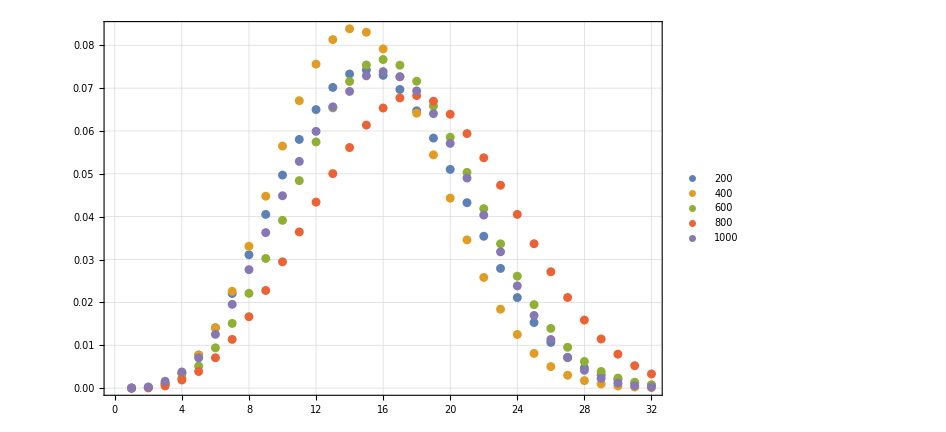

```mathematica
ListPlot[Join[{ILLData180WFilterBRamp1},ILLData180WFilterBRamp],PlotLegends->{200,400,600,800,1000}]
```

```mathematica
(*Table[Export["BRampData"<>ToString[{200,400,600,800,1000}[[i]]]<>"_180wFilter.txt",{Join[{XDataBRamp200},XDataBRampList][[i]],Join[{ILLData180WFilterBRamp1},ILLData180WFilterBRamp][[i,All,2]]},"Table"],{i,1,5}]*)
```

{BRampData200_180wFilter.txt,BRampData400_180wFilter.txt,BRampData600_180wFilter.txt,BRampData800_180wFilter.txt,BRampData1000_180wFilter.txt}

### fits

### first separately

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFitBRamp1=Reap[NonlinearModelFit[
ILLData180WFilterBRamp1,
{
FitFuncBinNormArith[bin,{b,Pi,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp200,4],
-0.002<b<0.001
},
{{b,-0.001}},bin,MaxIterations->4,EvaluationMonitor:>Sow[b],(*Method->"NMinimize",*)PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Mon 10 Feb 2020 14:46:37

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127098 and 0.0000692038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809345 and 0.0000192712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498775 and 7.55288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294032 and 4.52814×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1956 and 0.0000657238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296698 and 0.000130857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.440131 and 0.000223527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632167 and 0.000358532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872654 and 0.000632945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.154 and 0.000956431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46403 and 0.00133961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78801 and 0.00166851 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10911 and 0.00194896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41094 and 0.00245253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67421 and 0.00284225 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8796 and 0.00337156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01629 and 0.00318469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02887 and 0.00334298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06811 and 0.00308945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89964 and 0.00349779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6855 and 0.00327561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39783 and 0.00239975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05404 and 0.00242877 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67471 and 0.00191776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581914 and 0.000703237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911953 and 0.00100043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28543 and 0.00152843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319115 and 0.000290727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674508 and 0.0000236487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142526 and 0.000144138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454941 and 0.0000855663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127098 and 0.0000692038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294032 and 4.52814×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809345 and 0.0000192712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498775 and 7.55288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1956 and 0.0000657238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296698 and 0.000130857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.440131 and 0.000223527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632167 and 0.000358532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872654 and 0.000632945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.154 and 0.000956431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46403 and 0.00133961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78801 and 0.00166851 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10911 and 0.00194896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41094 and 0.00245253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67421 and 0.00284225 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8796 and 0.00337156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01629 and 0.00318469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06811 and 0.00308945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02887 and 0.00334298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89964 and 0.00349779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6855 and 0.00327561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39783 and 0.00239975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05404 and 0.00242877 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67471 and 0.00191776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28543 and 0.00152843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911953 and 0.00100043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581914 and 0.000703237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319115 and 0.000290727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142526 and 0.000144138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674508 and 0.0000236487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454941 and 0.0000855663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127116 and 0.0000692137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294076 and 4.5288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498848 and 7.55388×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809459 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296737 and 0.000130875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440186 and 0.000222302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632244 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872755 and 0.000633024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67436 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05383 and 0.00242849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.00152819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911796 and 0.00100025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581803 and 0.000703101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319048 and 0.00029067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674346 and 0.0000236431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454835 and 0.0000855467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127116 and 0.0000692137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809459 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294076 and 4.5288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498848 and 7.55388×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296737 and 0.000130875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440186 and 0.000222302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632244 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872755 and 0.000633024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67436 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05383 and 0.00242849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.00152819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581803 and 0.000703101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911796 and 0.00100025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319048 and 0.00029067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674346 and 0.0000236431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454835 and 0.0000855467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127116 and 0.0000692137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294075 and 4.5288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498847 and 7.55387×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809458 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296736 and 0.000130875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440186 and 0.000222302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632243 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872754 and 0.000633023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67436 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05384 and 0.0024285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.00152819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911798 and 0.00100025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581804 and 0.000703103 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319049 and 0.00029067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674348 and 0.0000236431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454836 and 0.0000855469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127115 and 0.0000692136 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294075 and 4.52879×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809457 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498846 and 7.55386×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296736 and 0.000130874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440185 and 0.000222301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632243 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872753 and 0.000633022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67435 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05384 and 0.0024285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911799 and 0.00100026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.0015282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581805 and 0.000703104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319049 and 0.000290671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454837 and 0.0000855471 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674349 and 0.0000236432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127116 and 0.0000692137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294076 and 4.5288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498848 and 7.55388×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809459 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296737 and 0.000130875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440186 and 0.000222302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632244 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872755 and 0.000633024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67436 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05383 and 0.00242849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.00152819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911797 and 0.00100025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581803 and 0.000703102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319048 and 0.00029067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454835 and 0.0000855467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674346 and 0.0000236431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127116 and 0.0000692137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294076 and 4.5288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498848 and 7.55388×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809459 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296737 and 0.000130875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440186 and 0.000222302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632244 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872755 and 0.000633024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67436 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05383 and 0.00242849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581803 and 0.000703102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.00152819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911797 and 0.00100025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319048 and 0.00029067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674346 and 0.0000236431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454835 and 0.0000855467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127116 and 0.0000692137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294075 and 4.5288×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498847 and 7.55387×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809458 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296736 and 0.000130875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440186 and 0.000222302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632243 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872754 and 0.000633023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67436 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05384 and 0.0024285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.00152819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911798 and 0.00100025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319049 and 0.00029067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581804 and 0.000703103 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674348 and 0.0000236431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454836 and 0.0000855469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127115 and 0.0000692136 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294075 and 4.52879×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498846 and 7.55386×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809457 and 0.0000192738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195626 and 0.0000657327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296736 and 0.000130874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.440185 and 0.000222301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632243 and 0.00035858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872753 and 0.000633022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15413 and 0.000956541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46418 and 0.00133975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78817 and 0.00166867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10928 and 0.00194912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4111 and 0.00245271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67435 and 0.0028424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87972 and 0.00337173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01636 and 0.00318475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89955 and 0.00349762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02883 and 0.00334294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68535 and 0.00327538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39764 and 0.00239954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05384 and 0.0024285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6745 and 0.00191751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28524 and 0.0015282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911799 and 0.00100026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319049 and 0.000290671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581805 and 0.000703104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142495 and 0.000144107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674349 and 0.0000236432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454837 and 0.0000855471 for the integral and error estimates.

1.68091

### took 1.75h

```mathematica
dBFitBRamp1[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.00169986 | 0.000193964 | -8.76381 | 6.78349×10^-10

### chi2 plot

```mathematica
dBFitBRamp1
```

{FittedModel[FitFuncBinNormArith[bin,{-0.00169986,π,0.20001,1.,1.,2.,1.},{0.01,«3»,0.},{-0.075,-0.0724194,-0.0698387,-0.0672581,«24»,-0.00274194,-0.00016129,0.00241935,0.005},4]],{{-0.001,-0.000999985,-0.0017,-0.00169999,-0.0017,-0.00169999,-0.0017,-0.00169999,-0.0017,-0.00169394,-0.00169394,-0.00168789,-0.0017,-0.00169986,-0.00169986,-0.00169985,-0.00169986,-0.00169381,-0.00169381,-0.00168775,-0.00169986}}}

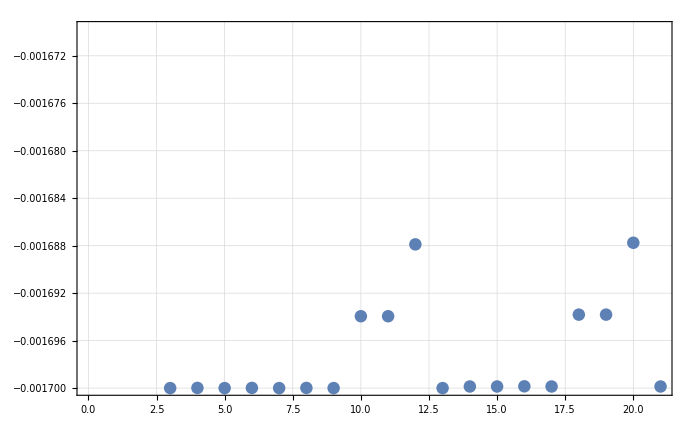

```mathematica
ListPlot[dBFitBRamp1[[2,1]]]
```

```mathematica
dBFitBRamp1[[2,1,1]]
```

-0.001

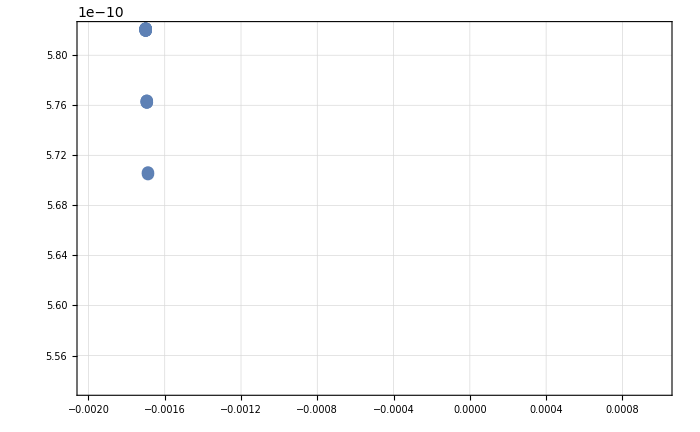

```mathematica
ListPlot[Table[
{
dBFitBRamp1[[2,1,b]],
Total[(
ILLData180WFilterBRamp1[[All,2]]-
Table[
FitFuncBinNormArith[bin,{dBFitBRamp1[[2,1,b]],Pi,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp200,4],
{bin,1,32}]
)^2]
},
{b,1,Length[dBFitBRamp1[[2,1]]]}],PlotRange->{{-0.002,0.001},Automatic}]
```

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ManualbVaryBRamp1=Table[
Table[FitFuncBinNormArith[bin,{b,Pi,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp200,4],{bin,1,32}],
{b,{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Mon 10 Feb 2020 16:38:28

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127123 and 0.000069218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294095 and 4.52909×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809509 and 0.000019275 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498879 and 7.55431×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195638 and 0.0000657368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296753 and 0.000130882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.44021 and 0.000222316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632277 and 0.000358601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15418 and 0.00095659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872798 and 0.000633057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46424 and 0.00133982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78824 and 0.00166874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10935 and 0.00194919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41118 and 0.00245279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67442 and 0.00284247 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87977 and 0.00337181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.0164 and 0.00318478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06814 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02881 and 0.00334292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8995 and 0.00349754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68528 and 0.00327528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39756 and 0.00239944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05374 and 0.00242838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67441 and 0.0019174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28516 and 0.00152809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911729 and 0.00100018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581755 and 0.000703044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.31902 and 0.000290645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142481 and 0.000144093 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674277 and 0.0000236407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454789 and 0.0000855383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294063 and 4.52861×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127111 and 0.0000692109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809427 and 0.0000192731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498827 and 7.5536×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195619 and 0.0000657303 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296726 and 0.00013087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.44017 and 0.000222293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632222 and 0.000358567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872726 and 0.000633001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15409 and 0.000956511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46414 and 0.00133971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78813 and 0.00166862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10923 and 0.00194907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41106 and 0.00245266 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67431 and 0.00284236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87968 and 0.00337169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01634 and 0.00318474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06813 and 0.00308946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02884 and 0.00334295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89957 and 0.00349767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68539 and 0.00327545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39769 and 0.00239959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05389 and 0.00242858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67456 and 0.00191758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28529 and 0.00152826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581834 and 0.00070314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.911841 and 0.0010003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319067 and 0.000290686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142504 and 0.000144116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674393 and 0.0000236447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0454865 and 0.0000855523 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127086 and 0.0000691967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0294 and 4.52766×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498723 and 7.55216×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809263 and 0.0000192693 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29667 and 0.000130844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195582 and 0.0000657173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.440091 and 0.000222275 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632112 and 0.000358497 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872581 and 0.000632889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15391 and 0.000957815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46393 and 0.0013395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.7879 and 0.0016684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10899 and 0.00194885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67411 and 0.00284214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41083 and 0.0024524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87952 and 0.00337144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01624 and 0.00318465 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.0681 and 0.00308944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02889 and 0.00334301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89971 and 0.00349791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.6856 and 0.00327577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39796 and 0.00239991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05419 and 0.00242897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67486 and 0.00191795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28557 and 0.0015286 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.581994 and 0.000703333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912065 and 0.00100056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319162 and 0.000290768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142549 and 0.000144161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674623 and 0.0000236527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0455016 and 0.0000855802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127073 and 0.0000691897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0809181 and 0.0000192674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0293969 and 4.52719×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0498671 and 7.55145×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195563 and 0.0000657108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296643 and 0.000130831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.440051 and 0.000222252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632057 and 0.000358463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872509 and 0.000632834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15382 and 0.000957735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46382 and 0.0013394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78778 and 0.00166828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10887 and 0.00194874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41071 and 0.00245227 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.674 and 0.00284203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87944 and 0.00337131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01619 and 0.00318461 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06808 and 0.00308944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02892 and 0.00334304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89978 and 0.00349804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68571 and 0.00327593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39809 and 0.00240007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05434 and 0.00242916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67501 and 0.00191813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28571 and 0.00152877 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.582073 and 0.00070343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912177 and 0.00100068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319209 and 0.000290809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674738 and 0.0000236568 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142571 and 0.000144184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0455092 and 0.0000855941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.08091 and 0.0000192655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.127061 and 0.0000691826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0293938 and 4.52672×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.049862 and 7.55074×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.296615 and 0.000130818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.195544 and 0.0000657043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.440012 and 0.00022223 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632002 and 0.000358428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.872437 and 0.000632778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15373 and 0.000957655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.46372 and 0.00133929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78766 and 0.00166817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41059 and 0.00245214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.10875 and 0.00194863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.6739 and 0.00284192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.87936 and 0.00337119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.01614 and 0.00318457 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.06807 and 0.00308943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.02895 and 0.00334307 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.89985 and 0.00349816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.39823 and 0.00240022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05449 and 0.00242936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.68581 and 0.00327609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67516 and 0.00191832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.582153 and 0.000703526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.912289 and 0.00100081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.319257 and 0.00029085 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.28584 and 0.00152894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.142594 and 0.000144207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00674853 and 0.0000236608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0455167 and 0.0000856081 for the integral and error estimates.

{{0.,0.000163174,0.00110058,0.00344802,0.00772021,0.0140784,0.0220637,0.0311005,0.0405203,0.0497002,0.0580205,0.0649834,0.0701674,0.0732967,0.0742484,0.0729962,0.0696898,0.0647204,0.05835,0.051046,0.0432751,0.0354344,0.027931,0.0211215,0.015301,0.010653,0.00718137,0.0047344,0.00307636,0.001959,0.00120728,0.000711704},{0.,0.000163202,0.00110076,0.00344856,0.00772136,0.0140803,0.0220664,0.0311038,0.040524,0.0497038,0.0580237,0.0649859,0.0701691,0.0732973,0.074248,0.0729949,0.0696878,0.0647179,0.0583472,0.0510431,0.0432723,0.0354319,0.0279288,0.0211198,0.0152997,0.010652,0.0071807,0.00473394,0.00307606,0.0019588,0.00120715,0.000711627},{0.,0.00016323,0.00110095,0.00344911,0.00772251,0.0140822,0.0220691,0.0311072,0.0405276,0.0497074,0.0580269,0.0649885,0.0701708,0.073298,0.0742477,0.0729937,0.0696858,0.0647154,0.0583443,0.0510402,0.0432695,0.0354293,0.0279267,0.021118,0.0152983,0.0106511,0.00718003,0.00473349,0.00307575,0.0019586,0.00120703,0.000711551},{0.,0.000163257,0.00110113,0.00344966,0.00772366,0.0140841,0.0220718,0.0311105,0.0405313,0.0497111,0.0580302,0.064991,0.0701724,0.0732987,0.0742473,0.0729924,0.0696838,0.0647129,0.0583415,0.0510372,0.0432667,0.0354268,0.0279245,0.0211163,0.015297,0.0106501,0.00717936,0.00473304,0.00307545,0.0019584,0.0012069,0.000711475},{0.,0.000163285,0.00110131,0.0034502,0.00772481,0.0140861,0.0220745,0.0311138,0.0405349,0.0497147,0.0580334,0.0649936,0.0701741,0.0732993,0.074247,0.0729912,0.0696818,0.0647103,0.0583387,0.0510343,0.0432639,0.0354243,0.0279223,0.0211145,0.0152957,0.0106492,0.0071787,0.00473258,0.00307515,0.0019582,0.00120677,0.000711399},{0.,0.000163313,0.0011015,0.00345075,0.00772595,0.014088,0.0220772,0.0311171,0.0405386,0.0497183,0.0580366,0.0649961,0.0701757,0.0733,0.0742467,0.0729899,0.0696799,0.0647078,0.0583358,0.0510314,0.0432611,0.0354217,0.0279201,0.0211128,0.0152943,0.0106482,0.00717803,0.00473213,0.00307485,0.001958,0.00120665,0.000711323}}

0.846273

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ManualbVaryBRamp2=Table[
Table[FitFuncBinNormArith[bin,{b,Pi,1.2+1.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp1200,4],{bin,1,32}],
{b,{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Mon 17 Feb 2020 16:33:57

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0243215 and 9.01372×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.07544 and 0.0000201398 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00583301 and 1.66718×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.194295 and 0.0000260923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.444077 and 0.000108595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.8391 and 0.000799375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.94276 and 0.000320489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.25459 and 0.00151255 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.2295 and 0.00270809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.72676 and 0.00416681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.6003 and 0.00498787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.6125 and 0.00533253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4609 and 0.00591524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.8742 and 0.00559036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6435 and 0.00443998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.6777 and 0.00287349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3832 and 0.00234991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.9207 and 0.0034775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.896 and 0.00381743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.3576 and 0.00443696 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4597 and 0.00413745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.45423 and 0.00436822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.88881 and 1.79055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63154 and 0.00383348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.769844 and 0.761295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.26135 and 0.00233245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140211 and 0.140258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0243187 and 9.01264×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0754319 and 0.0000201374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00583233 and 1.66698×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.194275 and 0.0000260898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.444033 and 0.000108584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.942672 and 0.000320458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83894 and 0.000798348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.25433 and 0.00151243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.22912 and 0.00270791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.5997 and 0.00493174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.72627 and 0.00416659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.6119 and 0.00533246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4604 and 0.0059153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6433 and 0.0044402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.8738 and 0.00559058 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.6776 and 0.00287365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3834 and 0.00234978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.921 and 0.00347732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8964 and 0.00381732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.3581 and 0.004437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4602 and 0.0041377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.4548 and 0.00436837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.88905 and 1.79078 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63203 and 0.00383361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.769962 and 0.761411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.2617 and 0.00233266 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140235 and 0.140281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.024316 and 9.01157×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00583164 and 1.66677×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0754238 and 0.0000201351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.194256 and 0.0000260873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.44399 and 0.000108574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.942585 and 0.000320426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83878 and 0.000798277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.25407 and 0.00151231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.22874 and 0.00270774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.72578 and 0.00416638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.5991 and 0.00493156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.6114 and 0.00533239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4599 and 0.00591536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6431 and 0.00444041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.8734 and 0.00559079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.6776 and 0.00287381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3836 and 0.00234965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.9212 and 0.00347715 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8968 and 0.00381721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.3586 and 0.00443704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4608 and 0.00413769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.45536 and 0.00436853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.8893 and 1.79101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63252 and 0.00383375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.77008 and 0.761527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.26206 and 0.00233287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140258 and 0.140305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0243133 and 9.0105×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00583096 and 1.66657×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0754158 and 0.0000201328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.194236 and 0.0000260848 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.443946 and 0.000108563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.942497 and 0.000320394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83861 and 0.000798206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.2538 and 0.00151218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.22837 and 0.00270419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.72529 and 0.00416616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.5986 and 0.00493138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.6108 and 0.00533233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4594 and 0.00591543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.8731 and 0.005591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6429 and 0.00444062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.6775 and 0.00287396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3837 and 0.00234953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.9215 and 0.00347697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8972 and 0.0038171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.3591 and 0.00443708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4614 and 0.00413768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.45593 and 0.00436868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.88954 and 1.79124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63301 and 0.00383388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.770197 and 0.761644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.26242 and 0.00233218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140282 and 0.140328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0243106 and 9.00943×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0754077 and 0.0000201304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00583028 and 1.66637×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.194216 and 0.0000260823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.443903 and 0.000108552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.942409 and 0.000320363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83845 and 0.000795373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.25354 and 0.00151206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.22799 and 0.00270402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.7248 and 0.00416594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.598 and 0.0049312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.6102 and 0.00533226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4589 and 0.00591549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6427 and 0.00444084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.8733 and 0.00832949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.6774 and 0.00287412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3839 and 0.0023494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.9218 and 0.0034768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8976 and 0.00381699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.3596 and 0.00443713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4619 and 0.00413767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.45649 and 0.00436883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.88978 and 1.79147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6335 and 0.00383401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.770315 and 0.76176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.26277 and 0.00233239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140305 and 0.140352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0753996 and 0.0000201281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0243078 and 9.00836×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00582961 and 1.66617×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.194196 and 0.0000260798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.44386 and 0.000108541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.942322 and 0.000320331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83829 and 0.000795303 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.25328 and 0.00151193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.22761 and 0.00270384 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.72432 and 0.00416573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.5975 and 0.00493102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.6097 and 0.00533219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4584 and 0.00591555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 18.8726 and 0.00565033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6425 and 0.00444105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.6773 and 0.00287428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3841 and 0.00234927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.922 and 0.00347663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8979 and 0.00381688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.3601 and 0.00443717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4625 and 0.00413766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.45705 and 0.00436899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.89002 and 1.79169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.770432 and 0.761876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.634 and 0.00383645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.26313 and 0.00233261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140329 and 0.140375 for the integral and error estimates.

{{0.,0.00048522,0.00266415,0.00653648,0.0112863,0.0194887,0.029257,0.0396578,0.0496864,0.0584709,0.0654776,0.0705389,0.0737874,0.0756086,0.076218,0.0750187,0.0714398,0.0653167,0.0569651,0.0471079,0.0366837,0.0267395,0.0180974,0.011263,0.00636446,0.00326255,0.00153679,0.000672386,0.000261071,0.0000841678,0.0000201859,2.85229×10^-6},{0.,0.000485302,0.00266456,0.00653732,0.0112876,0.0194904,0.029259,0.0396597,0.0496882,0.0584723,0.0654786,0.0705395,0.0737877,0.0756087,0.076218,0.0750184,0.071439,0.0653154,0.0569633,0.0471059,0.0366817,0.0267378,0.0180961,0.0112621,0.00636389,0.00326225,0.00153664,0.000672317,0.000261043,0.0000841583,0.0000201836,2.85194×10^-6},{0.,0.000485383,0.00266497,0.00653816,0.0112888,0.0194921,0.0292609,0.0396616,0.0496899,0.0584736,0.0654795,0.0705401,0.073788,0.0756089,0.076218,0.0750182,0.0714383,0.0653141,0.0569616,0.047104,0.0366797,0.0267361,0.0180948,0.0112611,0.00636333,0.00326194,0.00153649,0.000672248,0.000261015,0.0000841488,0.0000201812,2.85159×10^-6},{0.,0.000485464,0.00266537,0.006539,0.01129,0.0194938,0.0292629,0.0396636,0.0496916,0.0584749,0.0654804,0.0705406,0.0737883,0.075609,0.076218,0.0750179,0.0714375,0.0653128,0.0569599,0.047102,0.0366778,0.0267344,0.0180935,0.0112602,0.00636277,0.00326164,0.00153634,0.000672179,0.000260986,0.0000841394,0.0000201788,2.85125×10^-6},{0.,0.000485544,0.00266577,0.00653983,0.0112912,0.0194955,0.0292648,0.0396654,0.0496932,0.0584761,0.0654812,0.0705411,0.0737885,0.075609,0.0762178,0.0750174,0.0714366,0.0653134,0.056958,0.0470999,0.0366758,0.0267327,0.0180921,0.0112593,0.00636221,0.00326133,0.00153618,0.000672108,0.000260958,0.0000841298,0.0000201764,2.8509×10^-6},{0.,0.000485752,0.00266688,0.00654238,0.0112954,0.0195023,0.0292744,0.0396777,0.0497079,0.0584928,0.0654993,0.0705601,0.0738081,0.0753682,0.0762378,0.0750368,0.0714546,0.065328,0.0569712,0.0471103,0.0366834,0.026738,0.0180955,0.0112613,0.00636331,0.00326188,0.00153644,0.000672215,0.000260998,0.0000841424,0.0000201794,2.8513×10^-6}}

0.912715

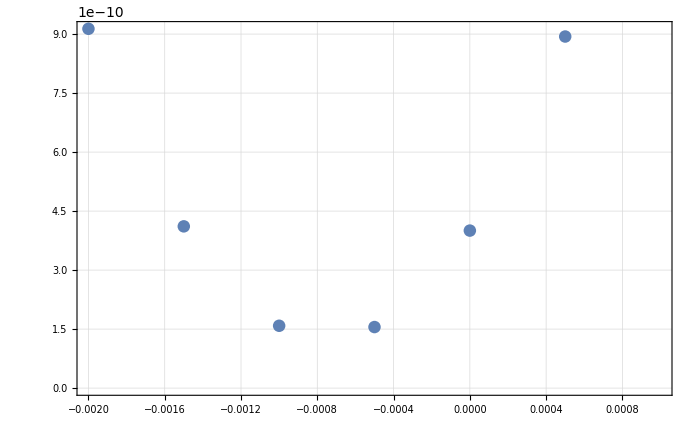

```mathematica
ListPlot[Table[
{
{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp1[[All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],Pi,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp200,4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}]}],PlotRange->{{-0.002,0.001},Automatic}]
```

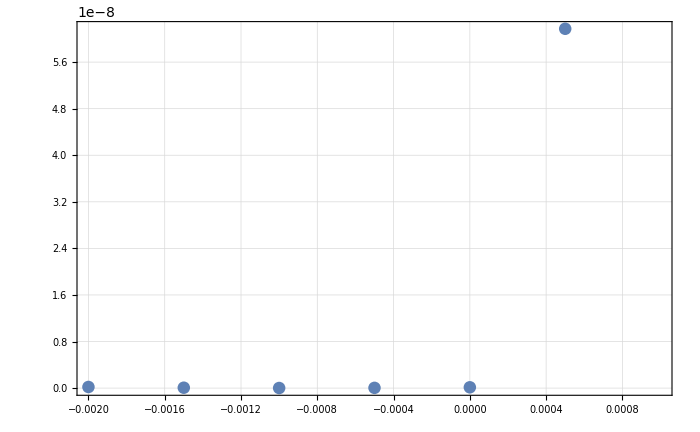

```mathematica
ListPlot[Table[
{
{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp2[[All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],Pi,1.2+1.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp1200,4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}]}],PlotRange->{{-0.002,0.001},All}]
```

```mathematica
Chi2Fit1=NonlinearModelFit[
Table[
{
{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp1[[All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],Pi,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp200,4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}]}],
{Chi2Func[b,b0,a,ce],-0.002<b0<0.002&&0.00001<a<0.001&&0.<ce<10^-9},
{{b0,-0.001},{a,0.0005},{ce,10^-10}},
b,Method->"NMinimize"
]
```

FittedModel[1.25706×10^-10+0.000497862 (0.000742688+b)^2]

```mathematica
Chi2Fit1=FittedModel[1.2570649843766801*^-10+0.000497862210552143 (0.0007426883966941822+b)^2]
```

FittedModel[1.25706×10^-10+0.000497862 (0.000742688+b)^2]

```mathematica
Chi2Fit1["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000742688 | 3.01635×10^-7 | -2462.21 | 1.4774×10^-10
a | 0.000497862 | 4.11183×10^-7 | 1210.81 | 1.24236×10^-9
ce | 1.25706×10^-10 | 3.94505×10^-13 | 318.644 | 6.81615×10^-8

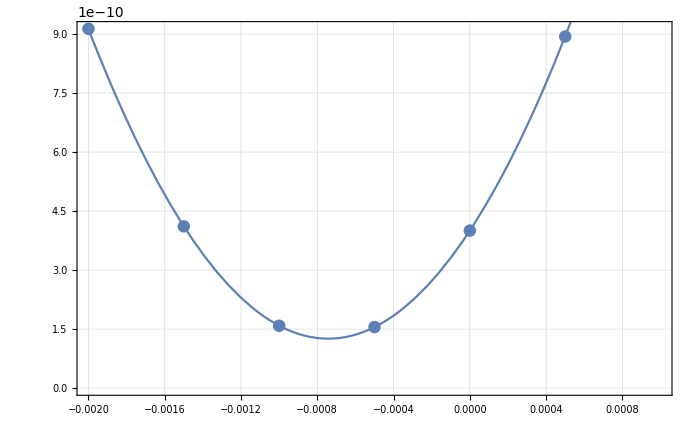

```mathematica
Show[
ListPlot[Table[
{
{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp1[[All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],Pi,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp200,4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}]}],PlotRange->{{-0.002,0.001},Automatic}],
Plot[Chi2Fit1[b],{b,-0.002,0.001}]
]
```

### 1.2Tesla - we remove b= 0.0005 because completely off??

```mathematica
Chi2Fit2=NonlinearModelFit[
Table[
{
{-0.002,-0.0015,-0.001,-0.0005,0.}[[b]],
Total[(
ILLData180WFilterBRamp2[[All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.001,-0.0005,0.}[[b]],Pi,1.2+1.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp1200,4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.001,-0.0005,0.}]}],
{Chi2Func[b,b0,a,ce],-0.001<b0<0.001&&0.00001<a<0.001&&0.<ce<10^-10},
{{b0,-0.0009},{a,0.00015},{ce,1*10^-11}},
b,Method->"NMinimize"
]
```

FittedModel[1.43354×10^-11+0.000148533 (0.000908414+b)^2]

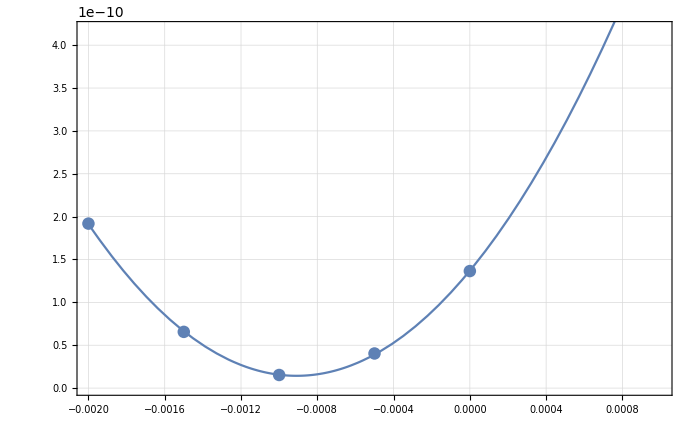

```mathematica
Show[
ListPlot[Table[
{
{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp2[[All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}[[b]],Pi,1.2+1.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRamp1200,4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}]}],PlotRange->{{-0.002,0.001},Automatic}],
Plot[Chi2Fit2[b],{b,-0.002,0.001}]
]
```

```mathematica
Chi2Fit2["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000908414 | 2.57944×10^-6 | -352.174 | 8.06268×10^-6
a | 0.000148533 | 1.23728×10^-6 | 120.048 | 0.0000693814
ce | 1.43354×10^-11 | 8.01481×10^-13 | 17.8862 | 0.00311125

```mathematica
-0.0009084140664250158/(5*10^-5)
```

-18.1683

### k value

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ManualbVaryBRamp=
Table[
Table[
Table[FitFuncBinNormArith[bin,{b,Pi,BRamps[[BRampi]]+BRamps[[BRampi]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampList[[BRampi]],4],{bin,1,32}],
{b,{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}}],
{BRampi,1,4}];
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Mon 10 Feb 2020 17:32:40

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0106056 and 2.04324×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0505015 and 7.07631×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244182 and 2.89298×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0965097 and 0.0000134739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173468 and 0.0000217152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298482 and 0.0000853459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.49888 and 0.000134752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.805397 and 0.000392187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24425 and 0.000629873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83108 and 0.000950317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56824 and 0.00146748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.44004 and 0.00192814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40924 and 0.00288436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.41345 and 0.00371109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.38087 and 0.00527777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.22406 and 0.0062232 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87322 and 0.00690254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25965 and 0.0072229 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33944 and 0.00734652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.08817 and 0.0070138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.51887 and 0.00627527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.66992 and 0.0048102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.6164 and 0.00407102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.45256 and 0.00306602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29064 and 0.0017654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24619 and 0.00138415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39738 and 0.00119377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.764636 and 0.000815771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147439 and 0.00386245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344155 and 0.000386939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109963 and 0.000284703 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0106044 and 2.04302×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0504961 and 7.07562×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0964996 and 0.0000134726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244155 and 2.89267×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173451 and 0.000021713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298452 and 0.0000853378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498832 and 0.000134739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.805324 and 0.000392146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24414 and 0.000629815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83093 and 0.000950236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56804 and 0.00146736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.4398 and 0.00192802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40896 and 0.00288417 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.41315 and 0.00371088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.38057 and 0.00527752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.2238 and 0.00622302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25955 and 0.00722281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87302 and 0.00690239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33946 and 0.00734663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.0883 and 0.00701399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.67024 and 0.00481047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.51911 and 0.00627555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61676 and 0.0040713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.45291 and 0.00306626 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29095 and 0.00176554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24644 and 0.00138427 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.764742 and 0.000815865 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39755 and 0.00119389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147464 and 0.00386311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344208 and 0.000386995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109981 and 0.000284748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0964946 and 0.000013472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0106038 and 2.0429×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244142 and 2.89252×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0504934 and 7.07527×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173442 and 0.0000217119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298438 and 0.0000853338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.805287 and 0.000392126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498809 and 0.000134733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24409 and 0.000629786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83085 and 0.000950195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56794 and 0.00146731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.43967 and 0.00192796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40882 and 0.00288408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.413 and 0.00371077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.38043 and 0.00527739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.22367 and 0.00622293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87293 and 0.00690232 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.2595 and 0.00722276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33946 and 0.00734668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.08837 and 0.00701408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.6704 and 0.00481061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.51923 and 0.0062757 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61693 and 0.00407144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.45309 and 0.00306637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29111 and 0.00176561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24656 and 0.00138433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39764 and 0.00119396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.764796 and 0.000815912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147476 and 0.00386344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344234 and 0.000387024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.10999 and 0.000284771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0106026 and 2.04268×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0964846 and 0.0000134707 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.050488 and 7.07458×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244115 and 2.89221×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173425 and 0.0000217097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298409 and 0.0000853257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498762 and 0.00013472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.805213 and 0.000392086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24398 and 0.000629728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.8307 and 0.000950114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56774 and 0.00146719 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.43943 and 0.00192785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40854 and 0.00288389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.4127 and 0.00371056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.38013 and 0.00527714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.22341 and 0.00622274 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87273 and 0.00690217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25938 and 0.00723915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33948 and 0.00734679 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.0885 and 0.00701427 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.51946 and 0.00627598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.67072 and 0.00481088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61729 and 0.00407173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.45344 and 0.00306661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29142 and 0.00176575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24681 and 0.00138445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39782 and 0.00119409 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.764902 and 0.000816006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147501 and 0.0038641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344287 and 0.00038708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.110008 and 0.000284816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010602 and 2.04256×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0964796 and 0.00001347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244102 and 2.89205×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0504853 and 7.07423×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173416 and 0.0000217086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298394 and 0.0000853217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498738 and 0.000134713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.805176 and 0.000392065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24393 and 0.000629699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83063 and 0.000950073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56764 and 0.00146714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.43931 and 0.00192779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.4084 and 0.0028838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.41255 and 0.00371046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.37998 and 0.00527701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.22328 and 0.00622265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87264 and 0.0069021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25933 and 0.0072391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33948 and 0.00734685 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.08856 and 0.00701436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.51958 and 0.00627612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.67087 and 0.00481102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61747 and 0.00407187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.45362 and 0.00306672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29157 and 0.00176582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24693 and 0.00138451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.3979 and 0.00119415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.764956 and 0.000816053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147514 and 0.00386443 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344313 and 0.000387108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.110017 and 0.000284839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0106014 and 2.04245×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0504826 and 7.07389×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0964745 and 0.0000134694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244088 and 2.8919×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173407 and 0.0000217075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.29838 and 0.0000853177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498715 and 0.000134707 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.80514 and 0.000392045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24387 and 0.00062967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83055 and 0.000950033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56754 and 0.00146708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.43919 and 0.00192773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40826 and 0.00288371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.4124 and 0.00371035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.37984 and 0.00527688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.22315 and 0.00622256 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87254 and 0.00690202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25928 and 0.00723906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33949 and 0.0073469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.08862 and 0.00701041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5197 and 0.00627627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.67103 and 0.00481116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61765 and 0.00407201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.4538 and 0.0030675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29173 and 0.00176589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24705 and 0.00138401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39799 and 0.00119422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.765009 and 0.0008161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147527 and 0.00386476 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344339 and 0.000387136 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.110026 and 0.000284862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0106008 and 2.04234×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0964695 and 0.0000134687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0504799 and 7.07355×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244075 and 2.89174×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173398 and 0.0000217064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298365 and 0.0000853136 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498691 and 0.0001347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.805103 and 0.000392025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24382 and 0.000629641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83047 and 0.000949992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56744 and 0.00146702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.43907 and 0.00192767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40812 and 0.00288361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.41225 and 0.00371025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.37969 and 0.00527676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.22302 and 0.00622247 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87244 and 0.00690195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25923 and 0.00723902 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33949 and 0.00734696 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.08868 and 0.0070105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.51982 and 0.00627641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.67119 and 0.00481129 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61783 and 0.00407215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.45397 and 0.00306761 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29188 and 0.00176596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24717 and 0.00138407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.765062 and 0.000816147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39808 and 0.00119428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147539 and 0.00386508 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344366 and 0.000387165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.110035 and 0.000284884 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0504745 and 7.07286×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0244048 and 2.89143×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0964595 and 0.0000134674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0105996 and 2.04211×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.173381 and 0.0000217042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.298336 and 0.0000853056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.498644 and 0.000134687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.80503 and 0.000391984 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.24371 and 0.000629583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.83032 and 0.000949911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.56725 and 0.00146691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.43882 and 0.00192755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.40784 and 0.00288343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.41195 and 0.00371004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.3794 and 0.0052765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.22276 and 0.00622229 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.87225 and 0.0069018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.25913 and 0.00723893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.08881 and 0.00701069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.33951 and 0.00734707 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.52005 and 0.00627669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.67152 and 0.00481472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.45433 and 0.00306785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61818 and 0.00407244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.29219 and 0.0017661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.24742 and 0.00138418 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.765169 and 0.00081624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.39825 and 0.00119441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0147564 and 0.00386574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.110053 and 0.00028493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.344418 and 0.000387221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240621 and 0.0000356721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135562 and 0.0000169294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411233 and 0.0000870255 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682716 and 0.000217102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67593 and 0.000670148 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09368 and 0.000408908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45164 and 0.00111371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42801 and 0.00174028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.92471 and 0.00378457 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59493 and 0.00270544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.37025 and 0.00441097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.86062 and 0.00474746 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3024 and 0.00685575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.585 and 0.00735686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6025 and 0.00840636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2598 and 0.00805354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2677 and 0.00809792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5902 and 0.00833715 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5073 and 0.00577553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1078 and 0.00441151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.51834 and 0.00299179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88674 and 0.00264884 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32101 and 0.00290718 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.89113 and 0.0023387 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65438 and 0.00159362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65146 and 0.00186208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.90404 and 0.000916915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.146626 and 0.0560496 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102502 and 0.0102537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.406824 and 0.00052203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240597 and 0.0000356688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135548 and 0.0000169277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411193 and 0.0000870117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682652 and 0.000217081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09358 and 0.000408871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67579 and 0.000670092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45143 and 0.00111362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42775 and 0.00174015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59461 and 0.00270525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.92433 and 0.00378435 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.36983 and 0.00441074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.86019 and 0.00474731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.302 and 0.00685558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.5846 and 0.00735669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6022 and 0.00840635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2597 and 0.00805358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2678 and 0.00809812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5905 and 0.0083373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5077 and 0.00577572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.5188 and 0.00299186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1083 and 0.00441163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88721 and 0.00264897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32144 and 0.00290729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.8915 and 0.00233885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65467 and 0.00159375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65167 and 0.00186226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.904166 and 0.000917033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14665 and 0.0560587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010252 and 0.0102554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.406886 and 0.000522105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135541 and 0.0000169269 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240585 and 0.0000356672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411173 and 0.0000870048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.68262 and 0.00021707 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09353 and 0.000408852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67571 and 0.000670064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45133 and 0.00111358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42762 and 0.00174008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59445 and 0.00270515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.92414 and 0.00378424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.36962 and 0.00441063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.85997 and 0.00474723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3018 and 0.00685549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.5844 and 0.00735661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6021 and 0.00840634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2596 and 0.00810129 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2679 and 0.00809822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5906 and 0.00833738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5079 and 0.00577582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1085 and 0.00441169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.51904 and 0.0029919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88744 and 0.00264903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32165 and 0.00290735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.89168 and 0.00233892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65482 and 0.00159049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65177 and 0.00186236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.904229 and 0.000917092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.146662 and 0.0560632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102528 and 0.0102563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.406917 and 0.000522142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135527 and 0.0000169252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240561 and 0.0000356639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411133 and 0.0000869911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682556 and 0.000217049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09343 and 0.000409034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67557 and 0.000670008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45113 and 0.00111349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42735 and 0.00173995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59412 and 0.00270497 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.92376 and 0.00378401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.3692 and 0.0044104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.85953 and 0.00474708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3014 and 0.00685532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.584 and 0.00735644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6018 and 0.00840632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2594 and 0.00810133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.268 and 0.00809842 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5909 and 0.00833754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5083 and 0.00577602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1089 and 0.00441181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.5195 and 0.00299197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.8879 and 0.00264916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32208 and 0.00290746 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.89205 and 0.00233906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65511 and 0.00159062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65198 and 0.00186254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.904355 and 0.000917211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.146686 and 0.0560724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102546 and 0.010258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.406979 and 0.000522217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240549 and 0.0000356622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.13552 and 0.0000169244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411113 and 0.0000869842 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682523 and 0.000217038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6755 and 0.00066998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09338 and 0.000409015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45103 and 0.00111344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42722 and 0.00173988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59396 and 0.00270487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.92357 and 0.00378389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.36899 and 0.00441029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.85932 and 0.00474701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3012 and 0.00685523 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.5839 and 0.00735635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6017 and 0.00840631 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2593 and 0.00810135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2681 and 0.00809851 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.591 and 0.00833762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5085 and 0.00577612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1092 and 0.00441187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.51974 and 0.00299201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88813 and 0.00264922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32229 and 0.00290752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.89223 and 0.00233914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65525 and 0.00159069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65208 and 0.00186263 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.904418 and 0.00091727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.146698 and 0.0560769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102555 and 0.0102589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.40701 and 0.000522255 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240537 and 0.0000356606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135513 and 0.0000169236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411093 and 0.0000869773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682491 and 0.000217027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09333 and 0.000408997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67542 and 0.000669952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45093 and 0.00111339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42709 and 0.00173981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.5938 and 0.00270478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.92338 and 0.00378378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.36878 and 0.00441018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.8591 and 0.00474694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.5837 and 0.00735627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3009 and 0.00685515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6015 and 0.0084063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2593 and 0.00810137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2682 and 0.00809861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5912 and 0.0083377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5086 and 0.00577622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1094 and 0.00441193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.51997 and 0.00300679 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88836 and 0.00264929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32251 and 0.00290757 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.89242 and 0.00233921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.6554 and 0.00159075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65219 and 0.00186272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.904481 and 0.000917329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14671 and 0.0560815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102563 and 0.0102598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.407041 and 0.000522292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135506 and 0.0000169227 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240525 and 0.0000356589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411073 and 0.0000869705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682459 and 0.000217017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09328 and 0.000408978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.67535 and 0.000669925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45083 and 0.00111335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.42696 and 0.00173975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59364 and 0.00270469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.9232 and 0.00378366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.36858 and 0.00442678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.85888 and 0.00474686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3007 and 0.00685506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.5835 and 0.00735619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6014 and 0.00840629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.2592 and 0.00810139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764626 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2683 and 0.00809871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5913 and 0.00833778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5088 and 0.00577632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1096 and 0.00441199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.5202 and 0.00300683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88859 and 0.00264935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32272 and 0.00290763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.8926 and 0.00233928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65229 and 0.00186281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65554 and 0.00159082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.904544 and 0.000917388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.146722 and 0.056086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102572 and 0.0102606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.407072 and 0.000522329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.240501 and 0.0000356557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.135492 and 0.0000169211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.411033 and 0.0000869567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.682395 and 0.000216996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.09318 and 0.000408942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.6752 and 0.000669869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45063 and 0.00111326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.4267 and 0.00173961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.59331 and 0.0027045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.92282 and 0.00378343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.36814 and 0.00442901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.85845 and 0.00474671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.5831 and 0.00735602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3003 and 0.00685489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6011 and 0.00840627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.259 and 0.00810143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2684 and 0.00809891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.4929 and 0.00764639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.5916 and 0.00833794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.5092 and 0.00577652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.11 and 0.00441211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.52067 and 0.0030069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.88905 and 0.00264948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.32315 and 0.00290775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.65583 and 0.00159095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.89297 and 0.00233942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.65249 and 0.00186299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.90467 and 0.000917506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0102589 and 0.0102624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.146745 and 0.0560951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.407134 and 0.000522404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34554 and 0.000567389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03724 and 0.000856386 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.850347 and 0.000267986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.94943 and 0.00135809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08643 and 0.00207076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.98846 and 0.00342185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67457 and 0.00361359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44305 and 0.00300788 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4354 and 0.00424344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1878 and 0.00541503 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8361 and 0.0054432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2896 and 0.0049483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4519 and 0.00572024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2339 and 0.00646869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5699 and 0.00701109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.4307 and 0.00665764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8238 and 0.00621466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7995 and 0.00481095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8838 and 0.00486397 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.4496 and 0.00339692 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1719 and 0.00611492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.37913 and 0.00321906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.86282 and 0.00235723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58399 and 0.00274717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.28709 and 0.00215988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92489 and 0.00201203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.82051 and 0.0017704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.996081 and 0.00115338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485088 and 0.161317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133214 and 0.130899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215461 and 0.0214622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.850268 and 0.00026796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03707 and 0.000850713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.94919 and 0.00135798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34542 and 0.000567334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08612 and 0.00207061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44267 and 0.0030077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67408 and 0.00361348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.98802 and 0.00342168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4349 and 0.00424331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1873 and 0.00541492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8356 and 0.00544315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2892 and 0.00494831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4516 and 0.0057203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2337 and 0.0064688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5699 and 0.00701124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.4308 and 0.00665776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.824 and 0.00621484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7998 and 0.00481094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8842 and 0.00486388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.45 and 0.00339684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1724 and 0.00611479 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.37965 and 0.00321915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.5845 and 0.00274729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.86329 and 0.00235727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.2875 and 0.00216002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92521 and 0.00201221 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.82073 and 0.0017706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.99622 and 0.00115352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485162 and 0.161342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133235 and 0.13092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215497 and 0.0214658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.850228 and 0.000267946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03698 and 0.000850675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.94907 and 0.00135792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34536 and 0.000567307 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08597 and 0.00207054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44248 and 0.0030076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67384 and 0.00361342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.9878 and 0.00342159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4346 and 0.00424325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.187 and 0.00541487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.289 and 0.00494831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8354 and 0.00544313 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4515 and 0.00572033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2336 and 0.00646886 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.4308 and 0.00665781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5698 and 0.00701132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.8 and 0.00481093 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8241 and 0.00621493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8844 and 0.00486384 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.4502 and 0.00339681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1727 and 0.00611473 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.3799 and 0.00321919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58476 and 0.00274735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.86353 and 0.00235729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.2877 and 0.00216009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92537 and 0.0020123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.82085 and 0.00177069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.99629 and 0.00115359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485199 and 0.161355 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133246 and 0.13093 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215516 and 0.0214676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.850149 and 0.00026792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34524 and 0.000567252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03681 and 0.000850599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.94883 and 0.00135781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08566 and 0.00207039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.98736 and 0.00342142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44211 and 0.00300752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67335 and 0.00361331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4341 and 0.00424312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1865 and 0.00541476 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8349 and 0.00544308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2886 and 0.00494833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4512 and 0.00572039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5698 and 0.00701148 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2335 and 0.00646897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.4309 and 0.00665793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8243 and 0.00621511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.8003 and 0.00481092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.4506 and 0.00339673 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8849 and 0.00486375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1732 and 0.00611459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.38042 and 0.00321927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58526 and 0.00274748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.864 and 0.00235732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.28811 and 0.00216023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92569 and 0.00201247 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.82107 and 0.00177089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.996429 and 0.00115374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485274 and 0.16138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133267 and 0.130951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215552 and 0.0214713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.850109 and 0.000267907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34518 and 0.000567225 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.94872 and 0.00135776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03672 and 0.000850562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08551 and 0.00207032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44192 and 0.00300743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.98714 and 0.00342134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67311 and 0.00361326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4339 and 0.00424306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8347 and 0.00544306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1863 and 0.0054147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2885 and 0.00494833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.451 and 0.00572042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5698 and 0.00701156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2334 and 0.00646902 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.431 and 0.00665799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8244 and 0.00621519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.8004 and 0.00481091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8851 and 0.0048637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.4508 and 0.00339669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1734 and 0.00611453 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.38067 and 0.00321931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58552 and 0.00274754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.86423 and 0.00235734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.28831 and 0.0021603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92585 and 0.00201256 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.82119 and 0.00177098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.996498 and 0.00115381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485311 and 0.161392 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133278 and 0.130962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215571 and 0.0214731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34512 and 0.000567197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.85007 and 0.000267894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03663 and 0.000850524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9486 and 0.0013577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08535 and 0.00207025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44173 and 0.00300734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.98692 and 0.00342125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67287 and 0.0036132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4336 and 0.00424299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8345 and 0.00544304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.186 and 0.00541464 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2883 and 0.00494834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4509 and 0.00572045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2333 and 0.00646908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5698 and 0.00701164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.431 and 0.00665805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8245 and 0.00621528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.8006 and 0.00481091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.451 and 0.0033739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8853 and 0.00486366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1737 and 0.00611446 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.38093 and 0.00321935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58577 and 0.0027476 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.86447 and 0.00235735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92601 and 0.00201265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.28851 and 0.00216037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.8213 and 0.00176931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.996567 and 0.00115388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133289 and 0.130973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485348 and 0.161405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215589 and 0.0214749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34506 and 0.00056717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03654 and 0.000850486 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.94848 and 0.00135765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.85003 and 0.000267881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.0852 and 0.00207018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44154 and 0.00300724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.9867 and 0.00342117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67262 and 0.00361315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4334 and 0.00424293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1858 and 0.00541459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8343 and 0.00544302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2881 and 0.00494834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2333 and 0.00646913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5698 and 0.00701253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4508 and 0.00572048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.4311 and 0.00665811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8246 and 0.00621537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.4512 and 0.00337386 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.8007 and 0.00481092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8855 and 0.00486361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1739 and 0.0061144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.8647 and 0.00235737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58602 and 0.00274767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.38119 and 0.00321939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.28871 and 0.00216044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.996637 and 0.00115395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92617 and 0.00201274 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82142 and 0.0017694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485385 and 0.161417 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215607 and 0.0214768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.1333 and 0.130983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.849951 and 0.000267855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.34494 and 0.000567115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.03637 and 0.000850411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.94824 and 0.00135754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.08489 and 0.00207003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.44116 and 0.00300706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.67214 and 0.00361304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.98626 and 0.003421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4329 and 0.0042428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1853 and 0.00541448 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.8338 and 0.00544297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.2877 and 0.0049256 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.4505 and 0.00571965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.5698 and 0.00701268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.2331 and 0.00646445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.4313 and 0.00679452 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.8249 and 0.00619461 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.801 and 0.00481096 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.886 and 0.00486352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.4515 and 0.00337378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.1744 and 0.00611426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.3817 and 0.00321948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.86517 and 0.0023574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.58653 and 0.00274779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.28912 and 0.00216057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92649 and 0.00201292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82164 and 0.0017696 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.996775 and 0.00115409 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.485459 and 0.161442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.133321 and 0.131004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0215644 and 0.0214804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160574 and 0.000030838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0723108 and 0.0000155781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.326243 and 0.0000513646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624796 and 0.000201114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14203 and 0.000402937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.95745 and 0.000897081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1264 and 0.00124365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67157 and 0.0020248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57497 and 0.00340082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76757 and 0.0039766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1312 and 0.00515408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.512 and 0.00552957 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7397 and 0.00591551 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6529 and 0.00604669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1148 and 0.00516857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0317 and 0.00420953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3554 and 0.00492208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.0859 and 0.00367082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0914 and 0.00298569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5124 and 0.00357438 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.3692 and 0.00479177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.5816 and 0.00369494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.99873 and 0.00386197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.60845 and 0.00314095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.0367 and 0.671328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.38475 and 0.00294675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45553 and 0.0023354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.93999 and 0.00206893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438106 and 0.43288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0708231 and 0.0708515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.072303 and 0.0000155764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160557 and 0.0000308349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.326211 and 0.000051358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624736 and 0.000201093 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14192 and 0.000399675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.95728 and 0.000896999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12615 and 0.00124355 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67123 and 0.00202466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57453 and 0.00340062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76705 and 0.00397954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1306 and 0.00515394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.5115 and 0.00552463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7392 and 0.00591549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6525 and 0.00604689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1146 and 0.00516871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0316 and 0.00420979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3555 and 0.00492227 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.086 and 0.00367083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0917 and 0.00298554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5127 and 0.00357428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.582 and 0.00369489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.3697 and 0.0047918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.99928 and 0.0038621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.60898 and 0.00314107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03684 and 0.671424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.38522 and 0.00294675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.4559 and 0.00233559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438173 and 0.432947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94024 and 0.00206913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.070835 and 0.0708634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0722991 and 0.0000155756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160549 and 0.0000308334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.326194 and 0.0000513547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624706 and 0.000201083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14187 and 0.000399656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.95719 and 0.000896959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12602 and 0.00124351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67105 and 0.00202458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.7668 and 0.00397954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57431 and 0.00340053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1304 and 0.00515387 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.5112 and 0.00559038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.739 and 0.00591547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6523 and 0.00604699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1145 and 0.00516878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0315 and 0.00420992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3555 and 0.00492236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.086 and 0.00367084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0918 and 0.00298547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5129 and 0.00357423 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.5822 and 0.00369486 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.3699 and 0.00479181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.99955 and 0.00386217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.60925 and 0.00314113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03692 and 0.671471 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.38546 and 0.00294687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438207 and 0.43298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45608 and 0.00233568 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94036 and 0.00206924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.070841 and 0.0708694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0722914 and 0.0000155739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160532 and 0.0000308303 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.326162 and 0.0000513482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624646 and 0.000201062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14177 and 0.000399618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.95702 and 0.000896878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12577 and 0.00124341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67071 and 0.00202444 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57388 and 0.00340033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76629 and 0.00397955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1298 and 0.00515635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.5106 and 0.00552949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7385 and 0.00591545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6519 and 0.00604718 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1142 and 0.0051793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0314 and 0.00421018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3555 and 0.00492254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.0861 and 0.00367086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0921 and 0.00297678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5133 and 0.00357412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.5827 and 0.00369481 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.3705 and 0.00479183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.0001 and 0.00386231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.60978 and 0.00314126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03707 and 0.671567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.38593 and 0.00294714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45644 and 0.00233588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438275 and 0.433047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.9406 and 0.00206945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0708529 and 0.0708813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160524 and 0.0000308288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0722875 and 0.000015573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.326146 and 0.0000513449 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624616 and 0.000201052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14172 and 0.000399599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.95694 and 0.000896837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12564 and 0.00124336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67054 and 0.00202436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57366 and 0.00340024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76604 and 0.00397956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1295 and 0.00515628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.5104 and 0.00552947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7382 and 0.00591543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6518 and 0.00604728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1141 and 0.00517938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0314 and 0.00421031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3555 and 0.00492263 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.0862 and 0.00367087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0922 and 0.0029767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5134 and 0.00357407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.5829 and 0.00369479 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.3707 and 0.00479185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.0004 and 0.00386238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.61005 and 0.00314132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03714 and 0.671615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.38616 and 0.00294728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45663 and 0.00233776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438309 and 0.433081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94072 and 0.00206955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0708588 and 0.0708873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0722836 and 0.0000155722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160516 and 0.0000308273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.32613 and 0.0000513416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624587 and 0.000201042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14166 and 0.00039958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.95685 and 0.000896796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12552 and 0.00124331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67036 and 0.00202429 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57344 and 0.00340014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76579 and 0.00397538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1293 and 0.00515621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.5101 and 0.00552946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.738 and 0.00591542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6516 and 0.00604738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.114 and 0.00517945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0313 and 0.00421044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3555 and 0.00492272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.0862 and 0.00367088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0924 and 0.00297663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5136 and 0.00357402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.371 and 0.00479186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.5831 and 0.00369477 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.0006 and 0.00386244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.61032 and 0.00314138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03721 and 0.671663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45681 and 0.00233785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.3864 and 0.00294742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438343 and 0.433114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94084 and 0.00206965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0708648 and 0.0708932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0722797 and 0.0000155713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160507 and 0.0000308258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.326113 and 0.0000513383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624557 and 0.000201031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14161 and 0.000399561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.95677 and 0.000896756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12539 and 0.00124326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67019 and 0.00202422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57322 and 0.00340005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76553 and 0.00397538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.129 and 0.00515614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.5098 and 0.00552944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7378 and 0.00591541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.6514 and 0.00604748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1139 and 0.00517952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0313 and 0.00421057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3555 and 0.00492282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.0863 and 0.00367089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0925 and 0.00297655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5138 and 0.00357396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.5833 and 0.00369474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.3712 and 0.00479187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.0009 and 0.00386251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.61058 and 0.00314144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03729 and 0.671711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.38663 and 0.00294756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438376 and 0.433148 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45699 and 0.00233795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.94096 and 0.00206975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0708707 and 0.0708991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.160491 and 0.0000308227 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.072272 and 0.0000155696 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.326081 and 0.0000513318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.624497 and 0.000201011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.14151 and 0.000414938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.9566 and 0.000896675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.12514 and 0.00124317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.66985 and 0.00202407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.76503 and 0.00397539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.57279 and 0.00339985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.1285 and 0.005156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.5093 and 0.00552941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7373 and 0.00591538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.651 and 0.00604768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.1137 and 0.00517967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.0312 and 0.00421083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.3555 and 0.004923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.0864 and 0.00367723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.0927 and 0.0029764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.5142 and 0.00357386 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.5838 and 0.00369469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.3717 and 0.00479189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.0015 and 0.00386265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.61112 and 0.00314156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.03743 and 0.671806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.3871 and 0.00294783 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.45736 and 0.00233814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.438444 and 0.433214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.9412 and 0.00206996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0708826 and 0.070911 for the integral and error estimates.

5.10877

### 5.1h

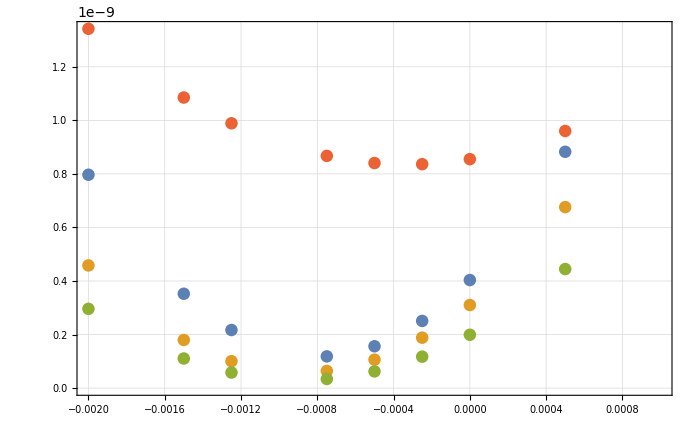

```mathematica
ListPlot[
Table[(*setup table*)
Table[(*b table*)
{
{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp[[setup,All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}[[b]],Pi,BRamps[[setup]]+BRamps[[setup]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampList[[setup]],4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}]}],
{setup,1,4}],PlotRange->{{-0.002,0.001},Automatic}]
```

```mathematica
Chi2BRamp=Table[(*setup table*)
Table[(*b table*)
{
{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp[[setup,All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}[[b]],Pi,BRamps[[setup]]+BRamps[[setup]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampList[[setup]],4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}]}],
{setup,1,4}];
```

```mathematica
ClearAll[Chi2Func]
```

```mathematica
Chi2Func[x_,x0_,a_,ce_]:=a*(x-x0)^2+ce
```

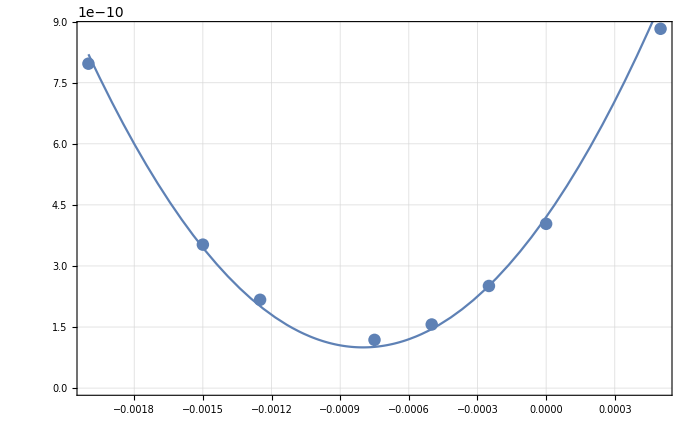

```mathematica
Show[
ListPlot[Chi2BRamp[[1]]],
Plot[Chi2Func[b,-0.0008,0.0005,1*10^-10],{b,-0.002,0.0005}]
]
```

```mathematica
Chi2FitBRamp=Table[
NonlinearModelFit[
Chi2BRamp[[setup]],
{Chi2Func[b,b0,a,ce],-0.002<b0<0.002&&0.00001<a<0.001&&0.<ce<10^-9},
{{b0,-0.001},{a,0.0005},{ce,10^-10}},
b,Method->"NMinimize"
],
{setup,1,4}]
```

{FittedModel[1.16394×10^-10+0.000462665 (0.000787622+b)^2],FittedModel[5.80014×10^-11+0.000323182 (0.000886429+b)^2],FittedModel[3.06778×10^-11+0.000215736 (0.000885369+b)^2],FittedModel[8.36827×10^-10+0.000181146 (0.000330115+b)^2]}

```mathematica
Chi2FitBRamp={FittedModel[1.1639448527944862*^-10+0.0004626652962695355 (0.0007876224431540024+b)^2],FittedModel[5.8001391585783126*^-11+0.0003231821407141568 (0.0008864288719769628+b)^2],FittedModel[3.0677834293175435*^-11+0.00021573570282643702 (0.0008853694986255048+b)^2],FittedModel[8.368265732207052*^-10+0.0001811458445381758 (0.0003301148952705439+b)^2]}
```

{FittedModel[1.16394×10^-10+0.000462665 (0.000787622+b)^2],FittedModel[5.80014×10^-11+0.000323182 (0.000886429+b)^2],FittedModel[3.06778×10^-11+0.000215736 (0.000885369+b)^2],FittedModel[8.36827×10^-10+0.000181146 (0.000330115+b)^2]}

```mathematica
#["ParameterTable"]&/@Chi2FitBRamp
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{ | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000787622 | 6.9395×10^-7 | -1134.98 | 1.00774×10^-14
a | 0.000462665 | 8.47781×10^-7 | 545.737 | 3.92078×10^-13
ce | 1.16394×10^-10 | 7.13561×10^-13 | 163.118 | 1.64294×10^-10, | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000886429 | 1.23804×10^-6 | -715.996 | 1.00865×10^-13
a | 0.000323182 | 1.00707×10^-6 | 320.914 | 5.57587×10^-12
ce | 5.80014×10^-11 | 8.45348×10^-13 | 68.6124 | 1.24538×10^-8, | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000885369 | 1.74699×10^-6 | -506.798 | 5.67689×10^-13
a | 0.000215736 | 9.4939×10^-7 | 227.236 | 3.13203×10^-11
ce | 3.06778×10^-11 | 7.9699×10^-13 | 38.4921 | 2.23003×10^-7, | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000330115 | 3.02597×10^-6 | -109.094 | 1.22718×10^-9
a | 0.000181146 | 9.52541×10^-7 | 190.171 | 7.62873×10^-11
ce | 8.36827×10^-10 | 7.38586×10^-13 | 1133.01 | 1.01655×10^-14}

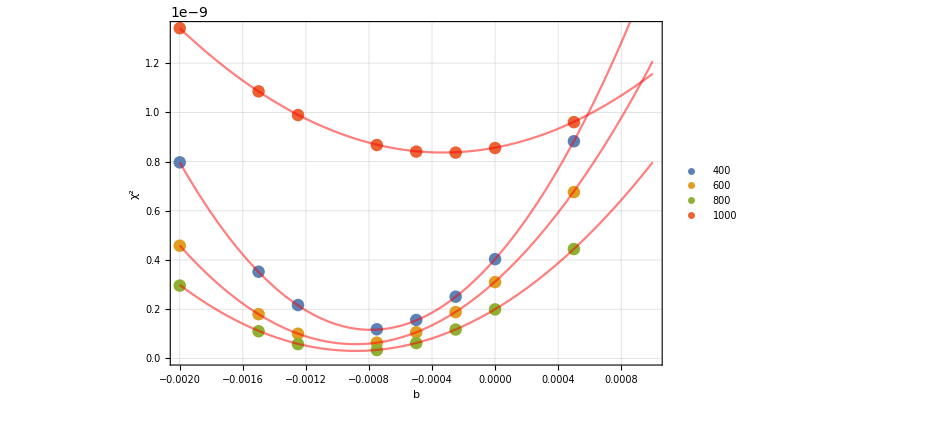

```mathematica
Show[
ListPlot[
Table[(*setup table*)
Table[(*b table*)
{
{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}[[b]],
Total[(
ILLData180WFilterBRamp[[setup,All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}[[b]],Pi,BRamps[[setup]]+BRamps[[setup]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampList[[setup]],4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005}]}],
{setup,1,4}],PlotRange->{{-0.002,0.001},Automatic},FrameLabel->{{"χ^2",None},{"b","Chi^2 parable fits"}},PlotLegends->{"400","600","800","1000"}],
Plot[Table[Chi2FitBRamp[[i]][b],{i,1,4}],{b,-0.002,0.001},PlotStyle->Directive[Red,Opacity[0.5]]]
]
```

### plot the sensitivity dependent on Bfield

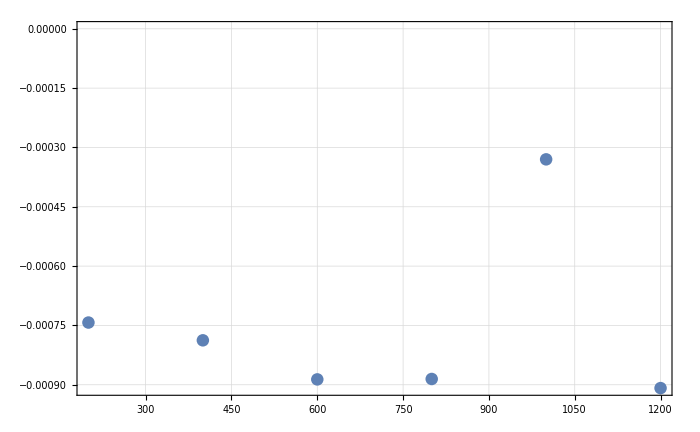

```mathematica
ListPlot[Transpose[{{200,400,600,800,1000,1200},Join[{Chi2Fit1["BestFitParameters"][[1,2]]},(#["BestFitParameters"][[1,2]])&/@Chi2FitBRamp,{Chi2Fit2["BestFitParameters"][[1,2]]}]}],PlotRange->All]
```

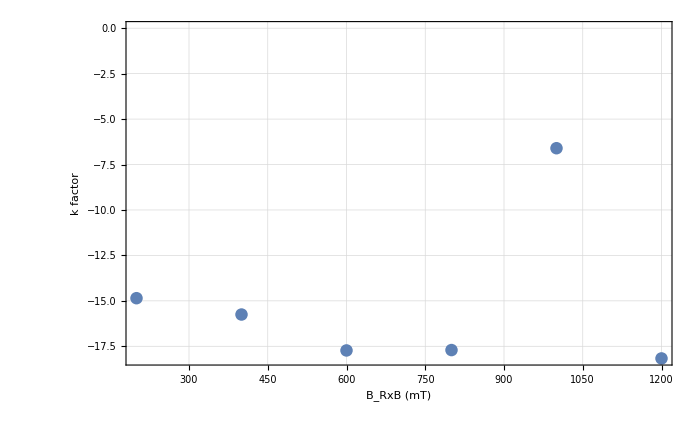

```mathematica
ListPlot[Transpose[{{200,400,600,800,1000,1200},Join[{Chi2Fit1["BestFitParameters"][[1,2]]},(#["BestFitParameters"][[1,2]])&/@Chi2FitBRamp,{Chi2Fit2["BestFitParameters"][[1,2]]}]/(5*10^-5)}],FrameLabel->{{"k factor",None},{"B_RxB (mT)","Fierz term sensitivity on B_RxB for varying B_RxB, α=180°"}},PlotRange->All]
```

Bfield ramp 90°

```mathematica
Round[Table[D1stBPolyGrad[pmax,Pi/2,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,{0.2,0.4,0.6,0.8,1}}],0.01]*0.8
```

{0.056,0.032,0.024,0.024,0.016}

```mathematica
XDataBRamp200A90=XDataCreation[{-0.051,0.005,0.},32]
```

{-0.051,-0.0491935,-0.0473871,-0.0455806,-0.0437742,-0.0419677,-0.0401613,-0.0383548,-0.0365484,-0.0347419,-0.0329355,-0.031129,-0.0293226,-0.0275161,-0.0257097,-0.0239032,-0.0220968,-0.0202903,-0.0184839,-0.0166774,-0.014871,-0.0130645,-0.0112581,-0.00945161,-0.00764516,-0.00583871,-0.00403226,-0.00222581,-0.000419355,0.0013871,0.00319355,0.005}

```mathematica
XDataBRamp400A90=XDataCreation[{-0.027,0.005,0.},32]
```

{-0.027,-0.0259677,-0.0249355,-0.0239032,-0.022871,-0.0218387,-0.0208065,-0.0197742,-0.0187419,-0.0177097,-0.0166774,-0.0156452,-0.0146129,-0.0135806,-0.0125484,-0.0115161,-0.0104839,-0.00945161,-0.00841935,-0.0073871,-0.00635484,-0.00532258,-0.00429032,-0.00325806,-0.00222581,-0.00119355,-0.00016129,0.000870968,0.00190323,0.00293548,0.00396774,0.005}

```mathematica
XDataBRamp600A90=XDataCreation[{-0.019,0.005,0.},32]
```

{-0.019,-0.0182258,-0.0174516,-0.0166774,-0.0159032,-0.015129,-0.0143548,-0.0135806,-0.0128065,-0.0120323,-0.0112581,-0.0104839,-0.00970968,-0.00893548,-0.00816129,-0.0073871,-0.0066129,-0.00583871,-0.00506452,-0.00429032,-0.00351613,-0.00274194,-0.00196774,-0.00119355,-0.000419355,0.000354839,0.00112903,0.00190323,0.00267742,0.00345161,0.00422581,0.005}

```mathematica
XDataBRamp1000A90=XDataCreation[{-0.011,0.005,0.},32]
```

{-0.011,-0.0104839,-0.00996774,-0.00945161,-0.00893548,-0.00841935,-0.00790323,-0.0073871,-0.00687097,-0.00635484,-0.00583871,-0.00532258,-0.00480645,-0.00429032,-0.00377419,-0.00325806,-0.00274194,-0.00222581,-0.00170968,-0.00119355,-0.000677419,-0.00016129,0.000354839,0.000870968,0.0013871,0.00190323,0.00241935,0.00293548,0.00345161,0.00396774,0.00448387,0.005}

```mathematica
BRampsA90={0.2,0.4,0.6,1.};
```

```mathematica
XDataBRampListA90={XDataBRamp200A90,XDataBRamp400A90,XDataBRamp600A90,XDataBRamp1000A90};
```

```mathematica
t0=AbsoluteTime[];
ILLData90WFilterBRamp=
Table[
Table[{bin,FitFuncBinNormArith[bin,{0.,Pi/2,BRampsA90[[BRampi]],1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampListA90[[BRampi]],4]},{bin,1,Length[XDataBRampListA90[[BRampi]]]}],
{BRampi,1,4}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0118425 and 2.78799×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574889 and 0.0000181189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0357802 and 6.71079×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212449 and 5.12671×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192721 and 0.000121459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0886864 and 0.0000407424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.13251 and 0.000057662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274383 and 0.000112819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738227 and 0.00232042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384418 and 0.000233495 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533214 and 0.00064516 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.01563 and 0.000561053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34683 and 0.00394797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37674 and 0.000977171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82357 and 0.00128982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.92236 and 0.0021972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.5111 and 0.0032371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06663 and 0.00405974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54545 and 0.00459721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89489 and 0.0057245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08149 and 0.00642924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84294 and 0.00517939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07107 and 0.00514496 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38672 and 0.00417816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.70978 and 0.00405999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99516 and 0.00185895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86275 and 0.00236154 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.23818 and 0.00107858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.227034 and 0.0143898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.637929 and 0.00118116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.035085 and 0.000158958 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353829 and 0.0000266391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0641759 and 0.0000180083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109835 and 0.0000270091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.179453 and 0.0000337389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282419 and 0.0000823649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643517 and 0.000325309 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431563 and 0.0000925981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943949 and 0.000274536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37219 and 0.00568196 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96716 and 0.00556653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75503 and 0.00174212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.74464 and 0.00228555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92118 and 0.00298918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24868 and 0.00400826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65852 and 0.00497023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07531 and 0.00575028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3945 and 0.00632604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.4923 and 0.00773098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2316 and 0.00843175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4834 and 0.00792915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1458 and 0.00644247 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.213 and 0.00456194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92806 and 0.00455121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47876 and 0.00411423 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92423 and 0.00354752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.34072 and 0.00440248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81049 and 0.00635627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43091 and 0.00223179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109795 and 0.0107841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29158 and 0.00244353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.481073 and 0.00081936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0774331 and 0.0000224477 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398244 and 0.0000792688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.24239 and 0.0000481256 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140931 and 0.0000298598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633203 and 0.000263183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.980662 and 0.00071599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25075 and 0.00911621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49682 and 0.000982042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.2933 and 0.00178255 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65286 and 0.00260862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.30697 and 0.00479619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20186 and 0.00490763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2378 and 0.00519628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2853 and 0.00737152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.1928 and 0.00725564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7877 and 0.00638309 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.9004 and 0.00581803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3651 and 0.00376379 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6296 and 0.00240199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8526 and 0.00343704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7797 and 0.00453785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3937 and 0.00514175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.706 and 0.00473139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78876 and 0.00465798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72411 and 0.00550642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63813 and 0.00439767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68231 and 0.00591509 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.794873 and 0.663161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.040527 and 0.0405387 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00845 and 0.00508966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26435 and 0.00055202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00185 and 0.00122415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1096 and 0.00156384 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64317 and 0.00270485 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.62367 and 0.00372199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00412 and 0.00500643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.632 and 0.00621433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3467 and 0.00734246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9127 and 0.00619419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0862 and 0.00619292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6129 and 0.00491379 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6857 and 0.00209785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6451 and 0.00304517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6821 and 0.003803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3126 and 0.00526798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4903 and 0.00635276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2563 and 0.0075729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.0054 and 1.76287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61286 and 5.27403 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7013 and 0.0067863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59286 and 3.54164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69858 and 1.69106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410566 and 0.410626 for the integral and error estimates.

2292.84701

### took 0.64h

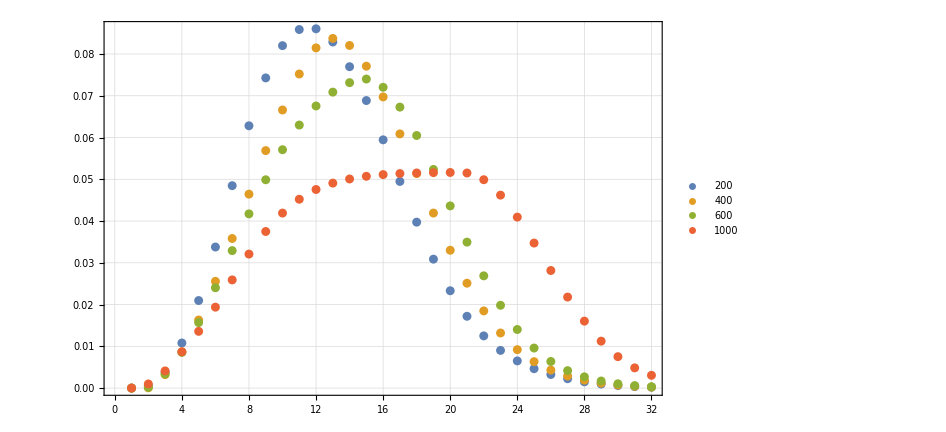

```mathematica
ListPlot[ILLData90WFilterBRamp,PlotLegends->{200,400,600,1000}]
```

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ManualbVaryBRampA90=
Table[(*Bvary*)
Table[(*b vary*)
Table[FitFuncBinNormArith[bin,{b,Pi/2,BRampsA90[[BRampi]]+BRampsA90[[BRampi]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampListA90[[BRampi]],4],{bin,1,32}],
{b,{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}}],
{BRampi,1,4}];
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Tue 11 Feb 2020 17:08:30

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113411 and 0.00257308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574845 and 0.0000182135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212402 and 5.23155×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357764 and 6.79247×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886826 and 0.000040773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192731 and 0.000122375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132512 and 0.0000613259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274402 and 0.000113004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738299 and 0.00232194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.38445 and 0.000231453 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533252 and 0.000643683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01574 and 0.000561649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34718 and 0.00390761 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.3769 and 0.000982605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82381 and 0.00128155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92274 and 0.00218913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.5116 and 0.00322409 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06721 and 0.00405069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54596 and 0.00457415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89531 and 0.00569284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08177 and 0.00644414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07131 and 0.00522147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84285 and 0.0051855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38647 and 0.00420683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.70944 and 0.00406384 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99478 and 0.00186346 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86232 and 0.00236756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.2379 and 0.00110118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.226951 and 0.0143853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.637752 and 0.00116099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350686 and 0.000158845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113398 and 0.00257279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574788 and 0.0000182118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.021238 and 5.23103×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357728 and 6.79181×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886741 and 0.000040769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132499 and 0.0000613202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192714 and 0.000122365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274379 and 0.000112996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384419 and 0.000231432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738244 and 0.00232171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533211 and 0.000643616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01567 and 0.000561608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.3768 and 0.000982533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34706 and 0.00393002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82369 and 0.00128147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92259 and 0.00218902 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51145 and 0.00322395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06708 and 0.00405054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54586 and 0.0045741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89526 and 0.0056928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08178 and 0.00644419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07138 and 0.00522158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84299 and 0.00518564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38665 and 0.00420703 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.70964 and 0.00406401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86251 and 0.0023677 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99494 and 0.00186358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.23801 and 0.00110128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.226981 and 0.0143864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.637816 and 0.00116556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350741 and 0.000158868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113392 and 0.00257264 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212368 and 5.23076×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.057476 and 0.0000182109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.035771 and 6.79149×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886699 and 0.0000407277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192705 and 0.00012236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132493 and 0.0000613173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274367 and 0.000112991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384403 and 0.000231422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.53319 and 0.000643583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738217 and 0.00232159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01563 and 0.000561587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37676 and 0.000982497 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34699 and 0.0039299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82364 and 0.00128143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92252 and 0.00218897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51138 and 0.00322388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54581 and 0.00457407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06701 and 0.00405047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89523 and 0.00569277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08178 and 0.00644421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84306 and 0.00518571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07142 and 0.00522163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38674 and 0.00420713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.70975 and 0.0040641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99502 and 0.00186364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86261 and 0.00236777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.23807 and 0.00110133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.226996 and 0.0143869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.637851 and 0.00116561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350769 and 0.000158774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.011338 and 0.00257234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574703 and 0.0000182092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212346 and 5.23024×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357673 and 6.79084×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886615 and 0.0000407237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192689 and 0.00012235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132481 and 0.0000613115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274344 and 0.000112982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384372 and 0.000231402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533149 and 0.000643516 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738162 and 0.00232136 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01556 and 0.000561546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37666 and 0.000982426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34686 and 0.00392967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82352 and 0.00128135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92237 and 0.00218887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51123 and 0.00322373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06688 and 0.00405032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54571 and 0.00457402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89518 and 0.00569273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08179 and 0.00644426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.8432 and 0.00518585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.0715 and 0.00522173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38693 and 0.00420732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.70995 and 0.0040739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86281 and 0.00236887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99518 and 0.00186377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.23819 and 0.00110143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.227025 and 0.014388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.637919 and 0.00116571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350824 and 0.000158797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113374 and 0.0025722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212335 and 5.22997×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357655 and 6.79051×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574675 and 0.0000182084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886573 and 0.0000407217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132475 and 0.0000613087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.19268 and 0.000122345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274333 and 0.000112978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384357 and 0.000231391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533128 and 0.000643482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738134 and 0.00232124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01553 and 0.000561525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37662 and 0.00098239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34679 and 0.00392956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82346 and 0.00128131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.9223 and 0.00218882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51116 and 0.00322366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06681 and 0.00405025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54566 and 0.00457399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89516 and 0.0056927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.0818 and 0.00644428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07154 and 0.00522178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84326 and 0.00518592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38702 and 0.00420742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.71005 and 0.00407399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.8629 and 0.00236894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99526 and 0.00186383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.23824 and 0.00110148 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.22704 and 0.0143885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.637954 and 0.00116577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350852 and 0.000158809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574647 and 0.0000182075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113368 and 0.00257205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212324 and 5.22971×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357637 and 6.79019×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886531 and 0.0000407197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132469 and 0.0000613058 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192672 and 0.000122339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274321 and 0.000112974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384341 and 0.000231641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533108 and 0.000643449 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738107 and 0.00232113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01549 and 0.000561504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37657 and 0.000982354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34672 and 0.00392944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82341 and 0.00128127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92222 and 0.00218877 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51108 and 0.00322359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06675 and 0.00405018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54561 and 0.00457396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89513 and 0.00569268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.0818 and 0.0064443 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84333 and 0.00518599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07158 and 0.00522183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38711 and 0.00420752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.71015 and 0.00407408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.863 and 0.00237636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99534 and 0.0018639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.2383 and 0.00110153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.227055 and 0.0143891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.637988 and 0.00116582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350879 and 0.000158821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113362 and 0.0025719 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212313 and 5.22945×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574619 and 0.0000182067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357619 and 6.78986×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886489 and 0.0000407178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192663 and 0.000122334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132463 and 0.0000613029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274309 and 0.000112969 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.73808 and 0.00232101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533087 and 0.000643415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384325 and 0.000231631 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01545 and 0.000561484 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37652 and 0.000982318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34666 and 0.00392933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82335 and 0.00128123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92215 and 0.00218871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51101 and 0.00322352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06668 and 0.00405011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54556 and 0.00457393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89511 and 0.00569266 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08181 and 0.00644433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.8434 and 0.00518606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07161 and 0.00522188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38719 and 0.00418747 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.71026 and 0.00407416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99542 and 0.00186396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86309 and 0.00237643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.23836 and 0.00110158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.22707 and 0.0143896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.638022 and 0.00116587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350907 and 0.000158832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113349 and 0.00257161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357583 and 6.78921×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574562 and 0.000018205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212291 and 5.22892×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886405 and 0.0000407138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192646 and 0.000122324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.132451 and 0.0000612972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274286 and 0.000112961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.738025 and 0.00232078 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384294 and 0.00023161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533046 and 0.000643348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01538 and 0.000561442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37643 and 0.000982247 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34652 and 0.0039291 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82324 and 0.00128114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92201 and 0.00218861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51086 and 0.00322338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06655 and 0.00404996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54546 and 0.00457388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.89505 and 0.00569261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08182 and 0.00645782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84354 and 0.0051862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07169 and 0.00522198 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38738 and 0.00418767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.71046 and 0.00407434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99558 and 0.00186408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86329 and 0.00237657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.23847 and 0.00110168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.227099 and 0.0143907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.638091 and 0.00116049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0350961 and 0.000158856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0113337 and 0.00257131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574506 and 0.0000182033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0212268 and 5.2284×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0357546 and 6.78857×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0886321 and 0.0000407098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.192629 and 0.000122314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.13244 and 0.0000590769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.274263 and 0.000112952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.384263 and 0.00023159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.73797 and 0.00232055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.533005 and 0.000643281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.01531 and 0.000561401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.37634 and 0.000982175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34639 and 0.00392887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.82312 and 0.00128106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.92186 and 0.00218851 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.51071 and 0.00322323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.06642 and 0.00404982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.54536 and 0.00457383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.895 and 0.00569256 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.08183 and 0.00645786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.07177 and 0.00522208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.84368 and 0.00518634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.38756 and 0.00418786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.71067 and 0.00407451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.99574 and 0.00186421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.86348 and 0.00237671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.23858 and 0.00110178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.227129 and 0.0143917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.63816 and 0.00116059 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0351016 and 0.000158879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353756 and 0.0000265925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641672 and 0.0000183067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109826 and 0.00002694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179442 and 0.0000349584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282422 and 0.0000833215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643556 and 0.00032509 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431584 and 0.0000952158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.944022 and 0.00026949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.3723 and 0.00569134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96744 and 0.00551821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75535 and 0.00173366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74509 and 0.00227609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92181 and 0.00301261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24653 and 0.00414388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65945 and 0.00493985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07629 and 0.00576715 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3954 and 0.00615597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4932 and 0.00772667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2322 and 0.00847393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4837 and 0.00797601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.146 and 0.00640739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.2128 and 0.00457767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92772 and 0.00454516 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47827 and 0.00412069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92362 and 0.00358383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.34034 and 0.00439701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.80988 and 0.00618087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43034 and 0.00255586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29124 and 0.00245187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109751 and 0.0107798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.480926 and 0.000801818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353719 and 0.0000265899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641607 and 0.000018305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109815 and 0.0000269375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179425 and 0.0000349555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282397 and 0.0000833143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643503 and 0.000325065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431546 and 0.000095209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943948 and 0.000269466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.3722 and 0.00569076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.9673 and 0.00551773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75516 and 0.00173354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74486 and 0.00227596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92154 and 0.00301246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24623 and 0.00414376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65915 and 0.00493972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07601 and 0.00576713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3951 and 0.00615593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.493 and 0.00772676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2322 and 0.00847404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4837 and 0.00797612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1462 and 0.00640748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.2131 and 0.00457755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92801 and 0.0045451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.4786 and 0.00412071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92395 and 0.00358393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.34065 and 0.00439709 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81015 and 0.00618083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43065 and 0.00221692 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010977 and 0.0107816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29137 and 0.00245207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.480985 and 0.000801926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.03537 and 0.0000265886 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.10981 and 0.0000269363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641575 and 0.0000183042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179417 and 0.0000349541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282384 and 0.0000833107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643476 and 0.000325053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431528 and 0.0000952057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943911 and 0.000269455 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37215 and 0.00569047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96723 and 0.00551749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75507 and 0.00173348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74474 and 0.00227589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9214 and 0.00301238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24608 and 0.0041437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65899 and 0.00493966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07587 and 0.00576712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.395 and 0.00615592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4929 and 0.00772681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2322 and 0.0084741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4838 and 0.00797617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1463 and 0.00640752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.2132 and 0.00457749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92816 and 0.00454507 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47876 and 0.00412071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92412 and 0.00358398 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.3408 and 0.00439713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81029 and 0.00619005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43075 and 0.00221699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109779 and 0.0107825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29144 and 0.00245217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.481014 and 0.00080198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353663 and 0.0000265861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.064151 and 0.0000183025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109799 and 0.0000269338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1794 and 0.0000349512 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282359 and 0.0000833035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643423 and 0.000325028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431491 and 0.0000951989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943836 and 0.000269431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37204 and 0.00568989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96709 and 0.00551701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75489 and 0.00173337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74451 and 0.00227576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92113 and 0.00301223 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24578 and 0.00414357 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65869 and 0.00493953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.0756 and 0.00577026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3948 and 0.00615588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4928 and 0.0077269 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2321 and 0.00847421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4839 and 0.00797628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1464 and 0.00640761 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.2135 and 0.00457736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92846 and 0.00454502 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47908 and 0.00412073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92445 and 0.00358408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.34112 and 0.0043972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81056 and 0.00619932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43095 and 0.00221714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109798 and 0.0107843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29156 and 0.00245238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.481076 and 0.000800155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353645 and 0.0000265848 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109794 and 0.0000269325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641478 and 0.0000183017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179391 and 0.0000349497 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282346 and 0.0000832999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643397 and 0.000325015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431472 and 0.0000951955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943799 and 0.00026942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37199 and 0.0056896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96702 and 0.00551676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75479 and 0.00173331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.7444 and 0.0022757 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92099 and 0.00301215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24564 and 0.00414351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65854 and 0.00493946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07546 and 0.00577025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3947 and 0.00615586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4927 and 0.00772695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2321 and 0.00847427 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4839 and 0.00797634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1465 and 0.00640765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 11.2136 and 0.0045773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92861 and 0.00454499 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47924 and 0.00412073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92461 and 0.00358412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.34127 and 0.00439724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.8107 and 0.0061993 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43105 and 0.00221722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29163 and 0.00245248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109807 and 0.0107852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.481105 and 0.000800209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353626 and 0.0000265835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641445 and 0.0000183008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109788 and 0.0000269313 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179383 and 0.0000349483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282333 and 0.0000832964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.64337 and 0.000325003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431453 and 0.0000951921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943762 and 0.000269408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37194 and 0.00568931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96695 and 0.00551652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7547 and 0.00173325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74428 and 0.00227563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92086 and 0.00301208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24549 and 0.00414345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65839 and 0.00495933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07532 and 0.00577025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3946 and 0.00615584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4927 and 0.00772699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2321 and 0.00847432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4839 and 0.0079764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1466 and 0.00640769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.2132 and 0.00451568 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92875 and 0.00454496 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47941 and 0.00412074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92478 and 0.00358417 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.34143 and 0.00439728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81083 and 0.00619928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43115 and 0.00221729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109816 and 0.0107861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29169 and 0.00245258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.481135 and 0.000800262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353608 and 0.0000265822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641413 and 0.0000183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179375 and 0.0000349468 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109783 and 0.0000269301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282321 and 0.0000832928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643344 and 0.000324991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431435 and 0.0000951887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943725 and 0.000269396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37189 and 0.00568903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96688 and 0.00551628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75461 and 0.0017332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74417 and 0.00227557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92072 and 0.003012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24534 and 0.00414339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65823 and 0.00495927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07518 and 0.00577024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3945 and 0.00615582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4926 and 0.00773874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.2321 and 0.00847438 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.484 and 0.00797645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1467 and 0.00640774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.2133 and 0.00451516 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47957 and 0.00412075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.9289 and 0.00454493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92494 and 0.00358422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.34158 and 0.00439732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81096 and 0.00619926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43125 and 0.00221737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29175 and 0.00245268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109825 and 0.010787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.481164 and 0.000800316 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353571 and 0.0000265796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641348 and 0.0000182983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109772 and 0.0000269276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179358 and 0.000034944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.282295 and 0.0000832856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643291 and 0.000324966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.431398 and 0.0000951819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.94365 and 0.000269373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37179 and 0.00568845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.96674 and 0.0055158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75443 and 0.00173308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74394 and 0.00227544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92045 and 0.00301185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24504 and 0.00414327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65793 and 0.00495914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.0749 and 0.00577022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3942 and 0.00615578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4925 and 0.00773883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.232 and 0.00847449 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4841 and 0.00797656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1469 and 0.00640782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.2136 and 0.00451412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.9292 and 0.00454488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.47989 and 0.00412076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.92527 and 0.0035793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.3419 and 0.00439739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81123 and 0.00619571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43146 and 0.00221752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109844 and 0.0107888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29188 and 0.00245286 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.481222 and 0.000800423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.757838,0.00986073,0.0268404}. NIntegrate obtained 0.0353534 and 0.000026577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0641284 and 0.0000182966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.109761 and 0.0000269251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.179341 and 0.0000349411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.28227 and 0.0000832785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.643238 and 0.000324941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.43136 and 0.0000951752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.943576 and 0.00026935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.37168 and 0.00568787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.9666 and 0.00551532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.75424 and 0.00173297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.74371 and 0.00227531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.92018 and 0.0030117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.24475 and 0.00414315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.65763 and 0.004959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.07462 and 0.00577021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.394 and 0.00615574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.4923 and 0.00773892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.232 and 0.0084746 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.4841 and 0.00797853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1471 and 0.00640791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.2138 and 0.00451308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.92949 and 0.00454482 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.48021 and 0.00412077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.9256 and 0.00357941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.34221 and 0.00439747 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.81151 and 0.00620108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43166 and 0.00221767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.29201 and 0.00245307 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0109862 and 0.0107906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.48128 and 0.000800531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0774244 and 0.0000228296 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398247 and 0.0000801638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242384 and 0.0000483145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140928 and 0.0000287187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980725 and 0.00072422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633226 and 0.000267073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25103 and 0.00908974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49693 and 0.000976053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29368 and 0.0017169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65472 and 0.0027411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.30775 and 0.0048288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20284 and 0.00491095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2865 and 0.00736712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2388 and 0.0052144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1939 and 0.00696614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7885 and 0.00639583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.901 and 0.00576726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3656 and 0.00388657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6298 and 0.0023871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8528 and 0.00344625 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7796 and 0.00461884 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3936 and 0.00511527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7055 and 0.00471157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78811 and 0.00465911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63734 and 0.00439994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72336 and 0.00549321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68162 and 0.00589197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.794723 and 0.663036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0405055 and 0.0405171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00798 and 0.00508637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0774166 and 0.0000228275 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242361 and 0.0000483104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398211 and 0.0000801573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140914 and 0.000028716 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633172 and 0.000267052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980646 and 0.000724164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25087 and 0.00908892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49682 and 0.000975975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29345 and 0.00171679 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.30741 and 0.00482856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65443 and 0.00274096 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20247 and 0.0049108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2384 and 0.00521431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2861 and 0.00736716 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1936 and 0.00696613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7884 and 0.00639601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.901 and 0.00577566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3656 and 0.00388665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6299 and 0.00238699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8529 and 0.00344618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7798 and 0.00461867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3939 and 0.00511494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7058 and 0.00471172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72374 and 0.00549341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78849 and 0.00465875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63769 and 0.00440017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.6819 and 0.00589212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.794796 and 0.663098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0405122 and 0.0405239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00816 and 0.00508666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398194 and 0.000080154 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140908 and 0.0000287147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0774127 and 0.0000228265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.24235 and 0.0000483083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633145 and 0.000267041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980607 and 0.000724137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25079 and 0.0090885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49676 and 0.000975937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65429 and 0.00274089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29334 and 0.00171673 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.30724 and 0.00482844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20228 and 0.00491073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2382 and 0.00521426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.286 and 0.00736718 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1935 and 0.00696612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7883 and 0.00639609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9009 and 0.00577577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3656 and 0.00388668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6299 and 0.00238694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.853 and 0.00344615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.78 and 0.00461858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.394 and 0.00511478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.706 and 0.00471179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78869 and 0.00465857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72393 and 0.0054935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63786 and 0.00440029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68204 and 0.0058922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.794832 and 0.663129 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0405155 and 0.0405272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00826 and 0.0050868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398158 and 0.0000801475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140894 and 0.000028712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242327 and 0.0000483041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0774049 and 0.0000228244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633092 and 0.00026702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980528 and 0.000724081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25063 and 0.00908767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49665 and 0.000975859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29312 and 0.00171661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.654 and 0.00274075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.3069 and 0.0048282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20189 and 0.00490809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2379 and 0.00521416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2856 and 0.00736722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1932 and 0.00696611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7881 and 0.00639627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3657 and 0.00388676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9009 and 0.00577598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6301 and 0.00238683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8532 and 0.00344608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7802 and 0.0046184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3943 and 0.00511445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7064 and 0.00471194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72432 and 0.00549369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78907 and 0.00465821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63821 and 0.00440052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68232 and 0.00589236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.794905 and 0.663192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0405222 and 0.0405339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00843 and 0.00508457 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242316 and 0.000048302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140887 and 0.0000287106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398141 and 0.0000801442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0774009 and 0.0000228234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633065 and 0.000267009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980489 and 0.000724054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25055 and 0.00908726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49659 and 0.00097582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29301 and 0.00171655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65386 and 0.00274068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.30673 and 0.00482809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.2017 and 0.00490801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2377 and 0.00521412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2854 and 0.00736724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1931 and 0.0069661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.788 and 0.00639636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9008 and 0.00577609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3657 and 0.0038868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6301 and 0.00238678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8533 and 0.00344605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7803 and 0.00461832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3944 and 0.00511428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7065 and 0.00471202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78926 and 0.00465802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72451 and 0.00549379 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63839 and 0.00440064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68246 and 0.00589243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.794942 and 0.663223 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0405256 and 0.0405373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00852 and 0.00508472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398123 and 0.000080141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.077397 and 0.0000228223 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14088 and 0.0000287093 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242305 and 0.0000482999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980449 and 0.000724026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633038 and 0.000266999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25046 and 0.00908684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49654 and 0.000975782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.2929 and 0.00171649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65372 and 0.00274061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.30657 and 0.00485069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20151 and 0.00490794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2375 and 0.00521407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2853 and 0.00736726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.193 and 0.0069661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7879 and 0.00639645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9008 and 0.0057762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3657 and 0.00388683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6302 and 0.00238673 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7804 and 0.00461823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8533 and 0.00344601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3946 and 0.00511412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7067 and 0.00471209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78945 and 0.00465784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63856 and 0.00440075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72471 and 0.00549389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.6826 and 0.00589251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.794978 and 0.663254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.040529 and 0.0405406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00862 and 0.00508486 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0773931 and 0.0000228213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398105 and 0.0000801377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140873 and 0.0000287079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242294 and 0.0000482979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.633012 and 0.000266988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.98041 and 0.000723999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25038 and 0.00908643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49648 and 0.000975743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29279 and 0.00171643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65357 and 0.00274054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.3064 and 0.00485057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20132 and 0.00490787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2373 and 0.00521402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1928 and 0.00696609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2851 and 0.00736728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7879 and 0.00639654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9014 and 0.00665586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3657 and 0.00388687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6302 and 0.00238667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8534 and 0.00344598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7805 and 0.00461814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3947 and 0.00511395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7069 and 0.00471216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.78964 and 0.00465766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.7249 and 0.00549398 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63874 and 0.00440087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68274 and 0.00589259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.795014 and 0.663285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0405323 and 0.040544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00871 and 0.005085 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0773853 and 0.0000227939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.39807 and 0.0000801312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242271 and 0.0000482937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.14086 and 0.0000287052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980332 and 0.000723944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632958 and 0.000266967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25022 and 0.0090856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49636 and 0.000975666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29257 and 0.00171631 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.65329 and 0.0027404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.30606 and 0.00485033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20095 and 0.00490772 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2369 and 0.00521392 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2847 and 0.00736732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1926 and 0.00696608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7877 and 0.00639672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.9013 and 0.00638678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3657 and 0.00388695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6304 and 0.00238657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.7807 and 0.00461797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8536 and 0.00344591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.395 and 0.00511362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7072 and 0.00471231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72528 and 0.00549417 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.79002 and 0.0046573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63909 and 0.0044011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68301 and 0.00589274 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.795087 and 0.663348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.040539 and 0.0405507 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00889 and 0.00508529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.398035 and 0.0000801247 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0773775 and 0.0000227919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.242249 and 0.0000482895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.140846 and 0.0000287025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.632905 and 0.000266946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.980253 and 0.000723888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.25006 and 0.00908478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.49625 and 0.000975588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.29235 and 0.00171619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.653 and 0.00274026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.30572 and 0.00485009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.20057 and 0.00490758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.2844 and 0.00736736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.2365 and 0.00521383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1923 and 0.00696606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.7875 and 0.00639689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.9012 and 0.00631289 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 17.3658 and 0.00388702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 16.6305 and 0.00238646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8538 and 0.00344584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.781 and 0.00461779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 13.3953 and 0.0051133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.7076 and 0.00471246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.72549 and 0.00555244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.7904 and 0.00465694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.63944 and 0.00440133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.68329 and 0.0058929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.79516 and 0.66341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0405457 and 0.0405574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00908 and 0.00508558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26443 and 0.000556091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00198 and 0.00120591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10988 and 0.00161704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64366 and 0.0026838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62472 and 0.0036775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00513 and 0.00497275 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6356 and 0.00638435 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3479 and 0.00739241 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9138 and 0.00619305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0871 and 0.00621751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6135 and 0.00485742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6859 and 0.00209562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6453 and 0.00304754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6821 and 0.00381611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3125 and 0.00530234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4899 and 0.00633964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00433 and 1.76257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2557 and 0.0075877 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61212 and 5.27333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7004 and 0.00675634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59197 and 3.54074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69793 and 1.6904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410359 and 0.410419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26433 and 0.000556043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00183 and 0.00120583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10966 and 0.00161693 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64336 and 0.00268363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62435 and 0.00367732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00469 and 0.00497258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6352 and 0.00638428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3475 and 0.00739256 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9135 and 0.00619333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0869 and 0.00621785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6134 and 0.00485769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.686 and 0.00209547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6454 and 0.00304725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6823 and 0.00381582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3128 and 0.00530211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4903 and 0.00633943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00479 and 1.76269 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2561 and 0.00758767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61247 and 5.27365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7008 and 0.00675644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69813 and 1.6906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59229 and 3.54107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.41042 and 0.41048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26428 and 0.000556018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00176 and 0.00120579 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64321 and 0.00268355 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10955 and 0.00161687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62416 and 0.00367723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00448 and 0.00497249 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6349 and 0.00638425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3473 and 0.00739264 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9133 and 0.00619346 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0868 and 0.00621802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6133 and 0.00485783 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.686 and 0.0020954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6455 and 0.00304711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6824 and 0.00381568 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3129 and 0.005302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4904 and 0.00633932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2563 and 0.00758766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00501 and 1.76274 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61264 and 5.27381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59246 and 3.54123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7011 and 0.0067565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69824 and 1.69071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.41045 and 0.410511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26418 and 0.00055597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00161 and 0.00120572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10933 and 0.00161676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64292 and 0.00268338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62378 and 0.00367705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00404 and 0.00497232 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6345 and 0.00638418 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3469 and 0.00739279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.913 and 0.00619374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0865 and 0.00621841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6132 and 0.00485811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6861 and 0.00209525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6456 and 0.00304683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6826 and 0.00381539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3132 and 0.00530177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4908 and 0.00633912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2567 and 0.00758763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00547 and 1.76285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61299 and 5.27413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59278 and 3.54156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7015 and 0.0067566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69844 and 1.69091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410511 and 0.410572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26412 and 0.000555945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00153 and 0.00120568 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10922 and 0.0016167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64277 and 0.0026833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62359 and 0.00367696 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00382 and 0.00497224 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6343 and 0.00638414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3466 and 0.00739286 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9128 and 0.00619388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0864 and 0.00621858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6132 and 0.00485824 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6861 and 0.00209518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6457 and 0.00304669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6827 and 0.00380966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3133 and 0.00530165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.491 and 0.00633901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2569 and 0.00758761 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00569 and 1.76291 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61316 and 5.27429 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7017 and 0.00673812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59295 and 3.54172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69854 and 1.69102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410541 and 0.410602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26407 and 0.000555921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00146 and 0.00120564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10912 and 0.00161664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64262 and 0.00268322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62341 and 0.00367687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00361 and 0.00497215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.634 and 0.00640162 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3464 and 0.00739294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9127 and 0.00619401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6132 and 0.00485838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0863 and 0.00621874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6861 and 0.00209511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6457 and 0.00304655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6828 and 0.00380952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3135 and 0.00530154 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4911 and 0.00633891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00592 and 1.76297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2571 and 0.0075876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61334 and 5.27445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.702 and 0.00673818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59311 and 3.54188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69864 and 1.69112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410572 and 0.410633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26402 and 0.000555897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00138 and 0.0012056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10901 and 0.00161659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64247 and 0.00268314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62322 and 0.00367678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00339 and 0.00497206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6338 and 0.00640159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3462 and 0.00739301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9125 and 0.00621011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0862 and 0.00621891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.6131 and 0.00485852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6862 and 0.00209503 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6458 and 0.0030464 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6829 and 0.00380937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3136 and 0.00530142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4913 and 0.00633881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00615 and 1.76305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2573 and 0.00758758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61351 and 5.27461 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7022 and 0.00673823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59327 and 3.54204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69875 and 1.69122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410602 and 0.410663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26392 and 0.000555848 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00123 and 0.00120552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10879 and 0.00161648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64217 and 0.00268297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62284 and 0.0036766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00295 and 0.00497189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6333 and 0.00640152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3458 and 0.00739316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9122 and 0.00621038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.086 and 0.00621925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.613 and 0.00485879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6862 and 0.00209489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6459 and 0.00304612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6831 and 0.00380908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3139 and 0.00530119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.4917 and 0.0063386 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.0066 and 1.7632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2578 and 0.00758755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61386 and 5.27493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7026 and 0.00673833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.5936 and 3.54237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69895 and 1.69143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410663 and 0.410724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.26382 and 0.0005558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00108 and 0.00120545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.64188 and 0.0026828 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.10857 and 0.00161636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.62247 and 0.00367642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 9.00252 and 0.00497172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 11.6329 and 0.00640145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.3454 and 0.00739331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.9119 and 0.00621066 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.0858 and 0.00621959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 20.613 and 0.00485907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 20.6863 and 0.00209474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.6461 and 0.00303799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.6833 and 0.00380879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 17.3141 and 0.00533972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 15.492 and 0.0063384 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.00705 and 1.76335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 13.2582 and 0.00757526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.61421 and 5.27525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.7031 and 0.00673844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.59393 and 3.54269 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.69916 and 1.69163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.410724 and 0.410785 for the integral and error estimates.

5.53705

### 5.5h

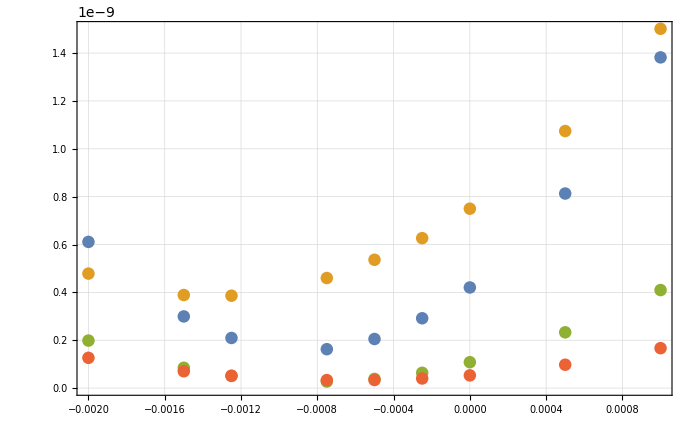

```mathematica
ListPlot[
Table[(*setup table*)
Table[(*b table*)
{
{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}[[b]],
Total[(
ILLData90WFilterBRamp[[setup,All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}[[b]],Pi/2,BRampsA90[[setup]]+BRampsA90[[setup]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampListA90[[setup]],4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}]}],
{setup,1,4}],PlotRange->{{-0.002,0.001},Automatic}]
```

```mathematica
Chi2BRampA90=Table[(*setup table*)
Table[(*b table*)
{
{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}[[b]],
Total[(
ILLData90WFilterBRamp[[setup,All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}[[b]],Pi/2,BRampsA90[[setup]]+BRampsA90[[setup]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampListA90[[setup]],4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}]}],
{setup,1,4}];
```

```mathematica
Chi2Func[x_,x0_,a_,ce_]:=a*(x-x0)^2+ce
```

```mathematica
Chi2FitBRampA90=Table[
NonlinearModelFit[
Chi2BRampA90[[setup]],
{Chi2Func[b,b0,a,ce],-0.002<b0<0.002&&0.00001<a<0.001&&0.<ce<10^-9},
{{b0,-0.001},{a,0.0005},{ce,10^-10}},
b,Method->"NMinimize"
],
{setup,1,4}]
```

{FittedModel[1.56703×10^-10+0.000352348 (0.000870101+b)^2],FittedModel[3.8249×10^-10+0.000200732 (0.00136866+b)^2],FittedModel[2.77649×10^-11+0.000118414 (0.000804922+b)^2],FittedModel[3.27019×10^-11+0.0000503583 (0.000632773+b)^2]}

```mathematica
#["ParameterTable"]&/@Chi2FitBRampA90
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{ | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000870101 | 2.89261×10^-6 | -300.802 | 9.11059×10^-14
a | 0.000352348 | 1.73109×10^-6 | 203.541 | 9.48916×10^-13
ce | 1.56703×10^-10 | 1.96505×10^-12 | 79.7454 | 2.61815×10^-10, | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00136866 | 0.0000182595 | -74.9562 | 3.79525×10^-10
a | 0.000200732 | 3.74439×10^-6 | 53.6088 | 2.82819×10^-9
ce | 3.8249×10^-10 | 4.30117×10^-12 | 88.9269 | 1.36219×10^-10, | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000804922 | 5.10645×10^-6 | -157.628 | 4.39768×10^-12
a | 0.000118414 | 1.09771×10^-6 | 107.874 | 4.27786×10^-11
ce | 2.77649×10^-11 | 1.25915×10^-12 | 22.0505 | 5.6861×10^-7, | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000632773 | 9.92216×10^-7 | -637.737 | 1.00331×10^-15
a | 0.0000503583 | 1.04146×10^-7 | 483.535 | 5.28089×10^-15
ce | 3.27019×10^-11 | 1.22022×10^-13 | 268. | 1.82139×10^-13}

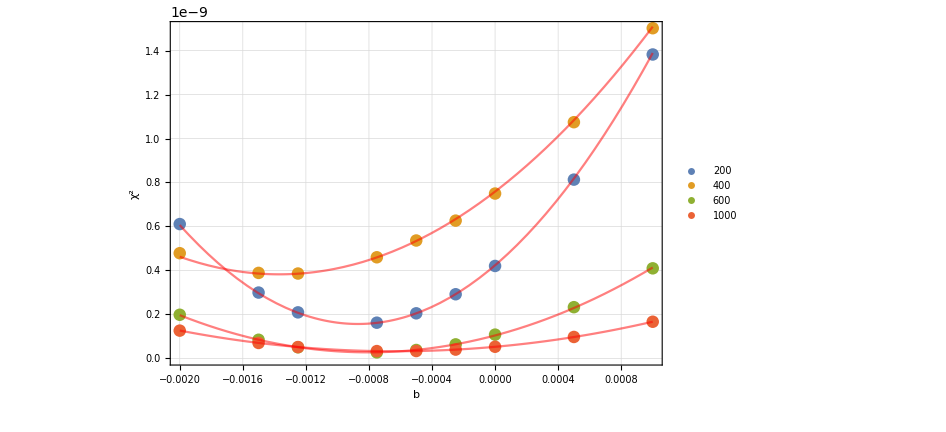

```mathematica
Show[
ListPlot[
Table[(*setup table*)
Table[(*b table*)
{
{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}[[b]],
Total[(
ILLData90WFilterBRamp[[setup,All,2]]-
Table[
FitFuncBinNormArith[bin,{{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}[[b]],Pi/2,BRampsA90[[setup]]+BRampsA90[[setup]]*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDataBRampListA90[[setup]],4],
{bin,1,32}]
)^2]
},
{b,1,Length[{-0.002,-0.0015,-0.00125,-0.00075,-0.0005,-0.00025,0.,0.0005,0.001}]}],
{setup,1,4}],PlotRange->{{-0.002,0.001},Automatic},FrameLabel->{{"χ^2",None},{"b","Chi^2 parable fits"}},PlotLegends->{"200","400","600","1000"}],
Plot[Table[Chi2FitBRampA90[[i]][b],{i,1,4}],{b,-0.002,0.001},PlotStyle->Directive[Red,Opacity[0.5]]]
]
```

### plot the sensitivity dependent on Bfield

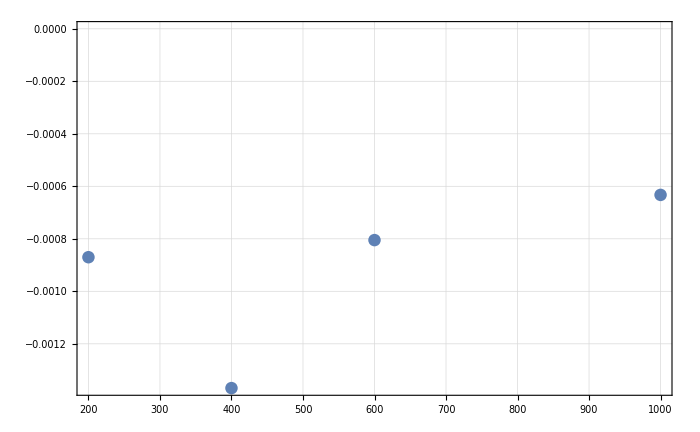

```mathematica
ListPlot[Transpose[{{200,400,600,1000},(#["BestFitParameters"][[1,2]])&/@Chi2FitBRampA90}]]
```

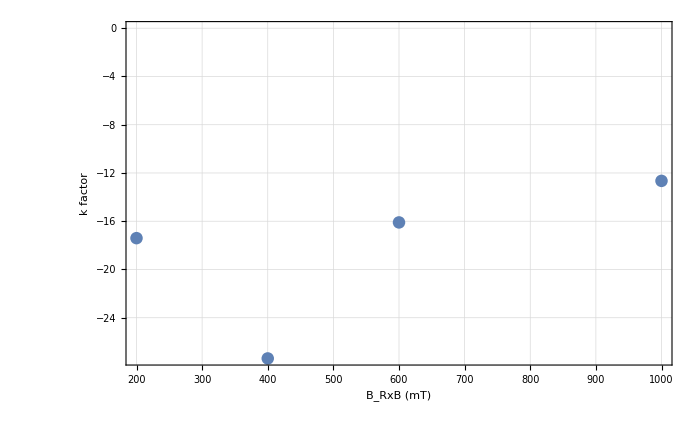

```mathematica
ListPlot[Transpose[{{200,400,600,1000},((#["BestFitParameters"][[1,2]])&/@Chi2FitBRampA90)/(5*10^-5)}],FrameLabel->{{"k factor",None},{"B_RxB (mT)","Fierz term sensitivity on B_RxB for varying B_RxB, α=90°"}}]
```

rF ramp

### check how the XData are limited

```mathematica
(thetamax[#]&/@{1.5,2.,3.,4.(*ratio*)})/Pi*180
```

{54.7356,45.,35.2644,30.}

```mathematica
Round[Table[D1stBPolyGrad[pmax,Pi,thetamaxi,0.2,1,0.,1,1,1]+2rG[pmax,thetamaxi,0.2]+0.01,{thetamaxi,thetamax[#]&/@{1.5,2.,3.,4.(*ratio*)}}],0.01]*0.8
```

{0.088,0.08,0.08,0.072}

# 180° at PERC

```mathematica
XDatam70p05=XDataCreation[{-0.070,0.005,0.},32]
```

{-0.07,-0.0675806,-0.0651613,-0.0627419,-0.0603226,-0.0579032,-0.0554839,-0.0530645,-0.0506452,-0.0482258,-0.0458065,-0.0433871,-0.0409677,-0.0385484,-0.036129,-0.0337097,-0.0312903,-0.028871,-0.0264516,-0.0240323,-0.0216129,-0.0191935,-0.0167742,-0.0143548,-0.0119355,-0.00951613,-0.00709677,-0.00467742,-0.00225806,0.00016129,0.00258065,0.005}

### Data (BDV = 1.5T)

```mathematica
t0=AbsoluteTime[];
PERCData180=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05,3]},{bin,1,Length[XDatam70p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74406 and 0.00275347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34389 and 0.00243879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10046 and 0.00217815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901291 and 0.00111872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481701 and 0.00161171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938561 and 0.000100574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299955 and 0.0000449281 for the integral and error estimates.

470.017208

### took 470s

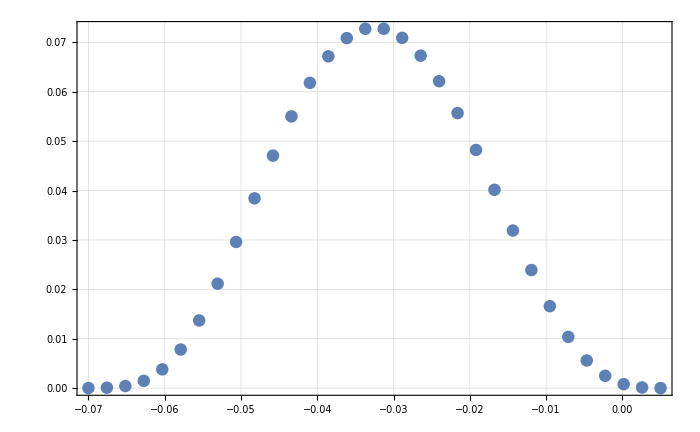

```mathematica
ListPlot[Transpose[{Reverse[XDatam70p05],PERCData180[[All,2]]}]]
```

```mathematica
t0=AbsoluteTime[];
PERCData180b1em3=Table[{bin,FitFuncBinNormArith[bin,{1.*10^-3,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05,3]},{bin,1,Length[XDatam70p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74404 and 0.00275347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34409 and 0.00243898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10071 and 0.00217841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901508 and 0.00112012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481866 and 0.00161226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938864 and 0.000100605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300055 and 0.0000449429 for the integral and error estimates.

466.457733

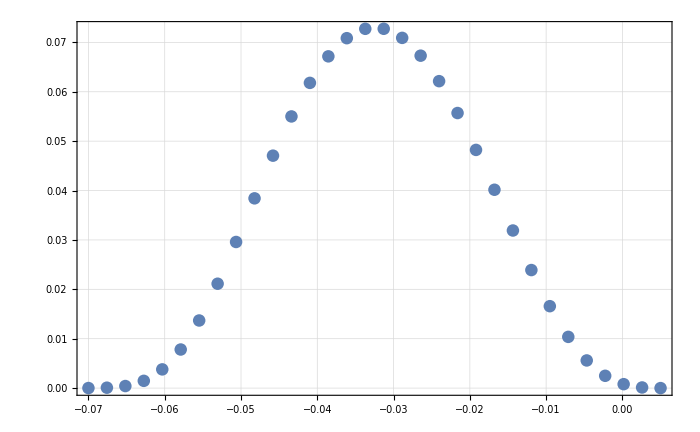

```mathematica
ListPlot[Transpose[{Reverse[XDatam70p05],PERCData180b1em3[[All,2]]}]]
```

```mathematica
(*Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronPERCData_180°_Xm70p05_32Bins.txt",Transpose[{Reverse[XDatam70p05],PERCData180[[All,2]]}],"Table"];
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronPERCData_180°_Xm70p05_32Bins_b1e-3.txt",Transpose[{Reverse[XDatam70p05],PERCData180b1em3[[All,2]]}],"Table"];*)
```

Fits

### dB fit

```mathematica
CloseKernels[];
LaunchKernels[2];
```

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFitPERC=Reap[NonlinearModelFit[
PERCData180,
{
FitFuncBinNormArith[bin,{b,Pi,0.2+0.2*5*10^-5,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05,3],
-0.002<b<0.002
},
{{b,-0.0005}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 4 Nov 2019 10:51:56

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34406 and 0.0024458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10059 and 0.0021849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901293 and 0.00110823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938557 and 0.000101313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299952 and 0.0000449492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481679 and 0.00161158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10029 and 0.00218457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901021 and 0.00111477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093818 and 0.000101274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299827 and 0.0000449308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481475 and 0.00161089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74432 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34379 and 0.00244553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10025 and 0.00218453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.900991 and 0.00111474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938138 and 0.000101269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299813 and 0.0000449287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481452 and 0.00161082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34383 and 0.00244558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10031 and 0.00218459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90104 and 0.00111345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938207 and 0.000101276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299836 and 0.0000449321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481489 and 0.00161094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34411 and 0.00244585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10065 and 0.00218497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901351 and 0.0011083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938638 and 0.000101321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299978 and 0.0000449531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481723 and 0.00161173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34383 and 0.00244557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1003 and 0.00218458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901035 and 0.00111344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.09382 and 0.000101276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299834 and 0.0000449318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481485 and 0.00161093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34449 and 0.00244624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10113 and 0.00218625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901776 and 0.00110817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939235 and 0.000101383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300176 and 0.0000449823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00482047 and 0.00161281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10029 and 0.00218457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901024 and 0.00111478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938185 and 0.000101274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299829 and 0.000044931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481477 and 0.0016109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74424 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34436 and 0.00244611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10096 and 0.00218607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901631 and 0.00110815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939029 and 0.000101362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300108 and 0.0000449722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481936 and 0.00161244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34452 and 0.00244627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10116 and 0.00218629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901806 and 0.00110821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939277 and 0.000101388 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.030019 and 0.0000449843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048207 and 0.00161289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10029 and 0.00218457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901021 and 0.00111477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093818 and 0.000101274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299827 and 0.0000449308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481475 and 0.00161089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74425 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34433 and 0.00244608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10092 and 0.00218602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901596 and 0.00110811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093898 and 0.000101357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300092 and 0.0000449698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481909 and 0.00161235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3441 and 0.00244584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10064 and 0.00218496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90134 and 0.00110828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938622 and 0.000101319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299973 and 0.0000449524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481715 and 0.0016117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34418 and 0.00244592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10074 and 0.00218506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901426 and 0.00110676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938743 and 0.000101332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300013 and 0.0000449583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048178 and 0.00161192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34384 and 0.00244559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10032 and 0.0021846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90105 and 0.00111346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093822 and 0.000101278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.029984 and 0.0000449328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481497 and 0.00161097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74432 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34378 and 0.00244552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10024 and 0.00218452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.900982 and 0.00111473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938125 and 0.000101268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299809 and 0.0000449281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481445 and 0.00161079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34415 and 0.0024459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1007 and 0.00218503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901396 and 0.00110673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938701 and 0.000101328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299999 and 0.0000449562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481757 and 0.00161184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34448 and 0.00244622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10111 and 0.00218623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90176 and 0.00110927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939211 and 0.000101381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300168 and 0.0000449811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00482034 and 0.00161277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34386 and 0.00244561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10035 and 0.00218463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901075 and 0.00111349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938256 and 0.000101282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299852 and 0.0000449345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481516 and 0.00161103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34454 and 0.00244628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10118 and 0.00218631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901823 and 0.00110823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939301 and 0.00010139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300198 and 0.0000449855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00482083 and 0.00161293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34392 and 0.00244567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10042 and 0.00218471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90114 and 0.00111212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938348 and 0.000101291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299882 and 0.000044939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481566 and 0.0016112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34414 and 0.00244589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10069 and 0.00218501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901385 and 0.00110671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938687 and 0.000101326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299995 and 0.0000449555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048175 and 0.00161181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74425 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34432 and 0.00244606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10091 and 0.00218525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901579 and 0.00110809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938956 and 0.000101354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300084 and 0.0000449687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481896 and 0.0016123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34406 and 0.0024458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10059 and 0.0021849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901295 and 0.00110823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938559 and 0.000101313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299952 and 0.0000449493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481681 and 0.00161158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3441 and 0.00244584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10064 and 0.00218495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901337 and 0.00110828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938618 and 0.000101319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299972 and 0.0000449522 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481712 and 0.00161169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34393 and 0.00244568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10043 and 0.00218473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901153 and 0.00111093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938361 and 0.000101292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299887 and 0.0000449396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481573 and 0.00161122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34409 and 0.00244583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10062 and 0.00218494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901326 and 0.00110827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938602 and 0.000101317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299967 and 0.0000449514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481704 and 0.00161166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34414 and 0.00244588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10068 and 0.002185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901378 and 0.00110671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938677 and 0.000101325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299991 and 0.000044955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481744 and 0.0016118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1003 and 0.00218458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901031 and 0.00111479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938194 and 0.000101275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299831 and 0.0000449315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481482 and 0.00161092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3441 and 0.00244584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10064 and 0.00218496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90134 and 0.00110829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938622 and 0.00010132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299973 and 0.0000449524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481715 and 0.0016117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74432 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34379 and 0.00244554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10026 and 0.00218453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.900995 and 0.00111474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938143 and 0.00010127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299815 and 0.000044929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481455 and 0.00161083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34401 and 0.00244576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10053 and 0.00218484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901244 and 0.00110817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938488 and 0.000101306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299929 and 0.0000449458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481642 and 0.00161145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3439 and 0.00244565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1004 and 0.00218469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901118 and 0.00111354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938316 and 0.000101288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299872 and 0.0000449375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481549 and 0.00161114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.344 and 0.00244574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10052 and 0.00218482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901228 and 0.00110968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938465 and 0.000101303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299921 and 0.0000449447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481629 and 0.00161141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7443 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34395 and 0.0024457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10046 and 0.00218476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901181 and 0.00111072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938396 and 0.000101296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299899 and 0.0000449414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481592 and 0.00161129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34421 and 0.00244595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10077 and 0.0021851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901456 and 0.0011068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938786 and 0.000101337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300028 and 0.0000449604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481804 and 0.00161199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34418 and 0.00244592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10074 and 0.00218507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901428 and 0.00110676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938746 and 0.000101332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300014 and 0.0000449584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481782 and 0.00161192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34415 and 0.0024459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10071 and 0.00218503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901399 and 0.00110673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938706 and 0.000101328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300001 and 0.0000449565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048176 and 0.00161185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34417 and 0.00244591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10072 and 0.00218505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901412 and 0.00110674 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938724 and 0.00010133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300007 and 0.0000449573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048177 and 0.00161188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34401 and 0.00244576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10053 and 0.00218484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901244 and 0.00110817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938488 and 0.000101306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299929 and 0.0000449458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481642 and 0.00161145 for the integral and error estimates.

37343.677118

### took 37343s or 10.4h - 2 cores

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.00088704 | 0.000129976 | -6.82464 | 1.20369×10^-7

```mathematica
dBFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

-17.7408

### rA fit

```mathematica
CloseKernels[]
```

{KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>]}

```mathematica
LaunchKernels[3]
```

{KernelObject[7,local],KernelObject[8,local],KernelObject[9,local]}

```mathematica
t0=AbsoluteTime[];
drAFitPERC=Reap[NonlinearModelFit[
PERCData180,
{
FitFuncBinNormArith[bin,{b,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam70p05,3],
-0.002<b<0.002
},
{{b,0.0005}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.0026286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23336 and 0.00234419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00138 and 0.00224262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858888 and 0.00104009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466486 and 0.00158777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894466 and 0.000100992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285835 and 0.0000461179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00087 and 0.00223229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858424 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466129 and 0.00158655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893818 and 0.000100921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285621 and 0.0000460839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54864 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23291 and 0.00234371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00083 and 0.00223225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858395 and 0.00103949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466106 and 0.00158648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893777 and 0.000100917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285607 and 0.0000460818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54866 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23295 and 0.00234376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00089 and 0.00223232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858443 and 0.00103954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466143 and 0.0015866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893844 and 0.000100924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285629 and 0.0000460853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54874 and 0.00262855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23322 and 0.00234404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00121 and 0.0022327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858738 and 0.00103985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466369 and 0.00158737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894254 and 0.000100969 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285765 and 0.0000461068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23295 and 0.00234375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00088 and 0.00223231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858438 and 0.00103953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466139 and 0.00158659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893837 and 0.000100923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285627 and 0.0000460849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23359 and 0.00234443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00166 and 0.00223815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859143 and 0.0010441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466683 and 0.00158844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894823 and 0.000101031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285953 and 0.0000461366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00087 and 0.0022323 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858427 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466131 and 0.00158656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893822 and 0.000100922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285622 and 0.0000460842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23346 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00151 and 0.00224277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859004 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466575 and 0.00158807 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894627 and 0.00010101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285888 and 0.0000461263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54886 and 0.0026287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23361 and 0.00234446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00169 and 0.00223819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859171 and 0.00104414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466705 and 0.00158852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894863 and 0.000101036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285967 and 0.0000461387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00087 and 0.00223229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858424 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466129 and 0.00158655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893818 and 0.000100921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285621 and 0.0000460839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23354 and 0.00234438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00161 and 0.00224289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859095 and 0.00104544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466645 and 0.00158831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894753 and 0.000101024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028593 and 0.000046133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54873 and 0.00262855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23321 and 0.00234403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0012 and 0.00223269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858727 and 0.00103984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466361 and 0.00158734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894239 and 0.000100967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028576 and 0.000046106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54876 and 0.00262858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23328 and 0.00234411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00129 and 0.00223279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858808 and 0.00104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466424 and 0.00158756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894354 and 0.00010098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285798 and 0.000046112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54866 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23296 and 0.00234377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0009 and 0.00223233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858452 and 0.00103955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0046615 and 0.00158663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893856 and 0.000100926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285633 and 0.0000460859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54869 and 0.00262849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23305 and 0.00234386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.001 and 0.00223245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858551 and 0.00103963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466224 and 0.00158688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893991 and 0.00010094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285678 and 0.000046093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00224293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85912 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466666 and 0.00158838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894792 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285943 and 0.000046135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54886 and 0.0026287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23363 and 0.00234448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00171 and 0.00223821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859187 and 0.00104415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466717 and 0.00158856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894886 and 0.000101038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285974 and 0.0000461399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5488 and 0.00262863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23342 and 0.00234425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00146 and 0.00224271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858959 and 0.00104116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466539 and 0.00158795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894563 and 0.000101003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285867 and 0.000046123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54871 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23314 and 0.00234395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00111 and 0.00223258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858648 and 0.00103974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466299 and 0.00158713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894127 and 0.000100955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285723 and 0.0000461001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5487 and 0.00262851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23311 and 0.00234392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00108 and 0.00223254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858616 and 0.00103971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466275 and 0.00158705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894083 and 0.00010095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285708 and 0.0000460978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00223813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859125 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466669 and 0.00158839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894799 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285945 and 0.0000461353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54866 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23297 and 0.00234377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0009 and 0.00223234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858458 and 0.00103956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466154 and 0.00158664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893865 and 0.000100927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285636 and 0.0000460864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00224293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859121 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466666 and 0.00158838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894792 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285943 and 0.000046135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54871 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23313 and 0.00234395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00111 and 0.00223258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858645 and 0.00103974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466297 and 0.00158713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894123 and 0.000100955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285722 and 0.0000460999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23348 and 0.00234432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00154 and 0.0022428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859029 and 0.00104124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466594 and 0.00158814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894661 and 0.000101013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.02859 and 0.0000461281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00086 and 0.00223229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858421 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466126 and 0.00158654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893813 and 0.000100921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285619 and 0.0000460837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54872 and 0.00262854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23318 and 0.00234399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00116 and 0.00223264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85869 and 0.00103979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466332 and 0.00158725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894187 and 0.000100962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285743 and 0.0000461033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54886 and 0.0026287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.2336 and 0.00234445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00168 and 0.00223818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85916 and 0.00104412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466697 and 0.00158849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894848 and 0.000101034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285962 and 0.0000461379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00224293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85912 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466665 and 0.00158838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894791 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285943 and 0.000046135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54874 and 0.00262856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23323 and 0.00234405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00122 and 0.00223271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858745 and 0.00103985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466374 and 0.00158739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894263 and 0.00010097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285768 and 0.0000461073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.00234431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859015 and 0.00104123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466583 and 0.0015881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894642 and 0.000101011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285893 and 0.0000461271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54876 and 0.00262858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23328 and 0.00234411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00129 and 0.00223279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858808 and 0.00104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466424 and 0.00158756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894354 and 0.00010098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285798 and 0.000046112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54871 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23313 and 0.00234395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00111 and 0.00223257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858641 and 0.00103974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466294 and 0.00158712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894118 and 0.000100954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028572 and 0.0000460996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.00262861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23336 and 0.00234419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00138 and 0.00224262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858892 and 0.00104109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466488 and 0.00158778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894469 and 0.000100993 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285836 and 0.0000461181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.2336 and 0.00234444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00168 and 0.00223817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859155 and 0.00104412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466693 and 0.00158847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894841 and 0.000101033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285959 and 0.0000461375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23345 and 0.00234428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00149 and 0.00224275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85899 and 0.0010412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466563 and 0.00158803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894606 and 0.000101007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285881 and 0.0000461252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54873 and 0.00262855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23321 and 0.00234403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0012 and 0.00223269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858728 and 0.00103984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466361 and 0.00158734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089424 and 0.000100967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028576 and 0.000046106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54873 and 0.00262854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23319 and 0.00234401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00118 and 0.00223266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858704 and 0.00103981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466342 and 0.00158728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894206 and 0.000100964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285749 and 0.0000461043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.0026286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23334 and 0.00234417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00137 and 0.0022426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858875 and 0.00104008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466476 and 0.00158774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894448 and 0.00010099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285829 and 0.0000461169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54883 and 0.00262867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23352 and 0.00234436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00159 and 0.00224286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859074 and 0.00104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466628 and 0.00158825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894724 and 0.00010102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285921 and 0.0000461314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23359 and 0.00234444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00167 and 0.00223816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859148 and 0.00104411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466687 and 0.00158845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089483 and 0.000101032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285956 and 0.000046137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23346 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00151 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859009 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466578 and 0.00158808 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894633 and 0.00010101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028589 and 0.0000461266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23349 and 0.00234433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00154 and 0.00224281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859035 and 0.00104125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466599 and 0.00158815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089467 and 0.000101014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285903 and 0.0000461286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.00234431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859014 and 0.00104123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466582 and 0.0015881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089464 and 0.000101011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285893 and 0.000046127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859013 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466581 and 0.00158809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894638 and 0.000101011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285892 and 0.0000461269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.00262861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23337 and 0.0023442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0014 and 0.00224264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858907 and 0.0010411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466499 and 0.00158781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089449 and 0.000100995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285843 and 0.0000461192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23346 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00151 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859008 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466578 and 0.00158808 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894632 and 0.00010101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028589 and 0.0000461266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23345 and 0.00234429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0015 and 0.00224276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858995 and 0.00104121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466568 and 0.00158805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894614 and 0.000101008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285884 and 0.0000461257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.00234431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859017 and 0.00104123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466584 and 0.0015881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894644 and 0.000101012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285894 and 0.0000461272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5488 and 0.00262863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23344 and 0.00234427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00148 and 0.00224274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858979 and 0.00104119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466555 and 0.001588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894591 and 0.000101006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285876 and 0.0000461244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23345 and 0.00234429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0015 and 0.00224276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858999 and 0.00104121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466571 and 0.00158806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894619 and 0.000101009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285886 and 0.0000461259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23348 and 0.00234432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00153 and 0.0022428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859024 and 0.00104124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0046659 and 0.00158812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894654 and 0.000101013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285897 and 0.0000461277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5488 and 0.00262863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23344 and 0.00234427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00148 and 0.00224274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85898 and 0.00104119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466556 and 0.00158801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894593 and 0.000101006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285877 and 0.0000461245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23349 and 0.00234433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00154 and 0.00224281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859035 and 0.00104125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466599 and 0.00158815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089467 and 0.000101014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285903 and 0.0000461286 for the integral and error estimates.

32271.96776

### took 8.96h

```mathematica
drAFitPERC[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.00120729 | 0.000273044 | 4.42157 | 0.000111819

```mathematica
drAFitPERC[[1]]["BestFitParameters"][[1,2]]/10^-4
```

12.0729

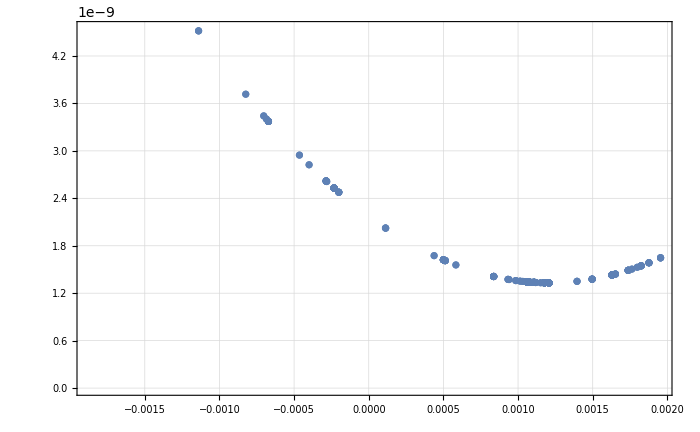

```mathematica
ListPlot[Table[{b,
Total[(PERCData180[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam70p05,3],{bin,1,32}])^2]},{b,drAFitPERC[[2,1]]}]]
```

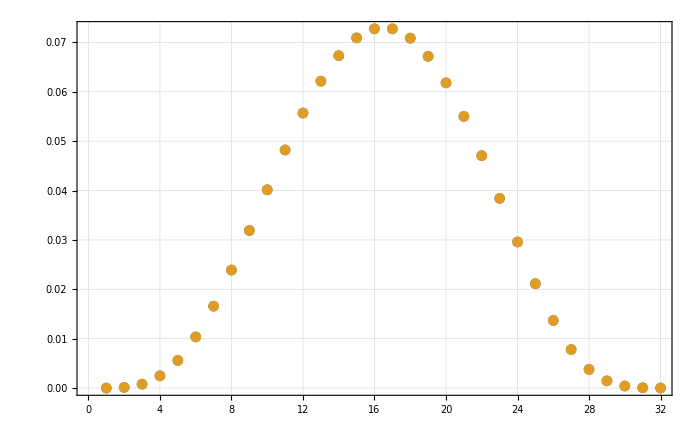

```mathematica
ListPlot[{PERCData180,Table[{bin,FitFuncBinNormArith[bin,{drAFitPERC[[1]]["BestFitParameters"][[1,2]],Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam70p05,3]},{bin,1,32}]}]
```

# 90° but with filter!

### data

```mathematica
t0=AbsoluteTime[];
ILLData90WFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi/2,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010828 and 0.00240031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26797 and 0.00317965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.1044 and 0.00433095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.60251 and 0.00530303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9489 and 0.00586929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10023 and 0.00617257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.01576 and 0.00547174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67541 and 0.00522039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750963 and 0.00289333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271332 and 0.0148705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423872 and 0.000119545 for the integral and error estimates.

403.520077

### took 470s

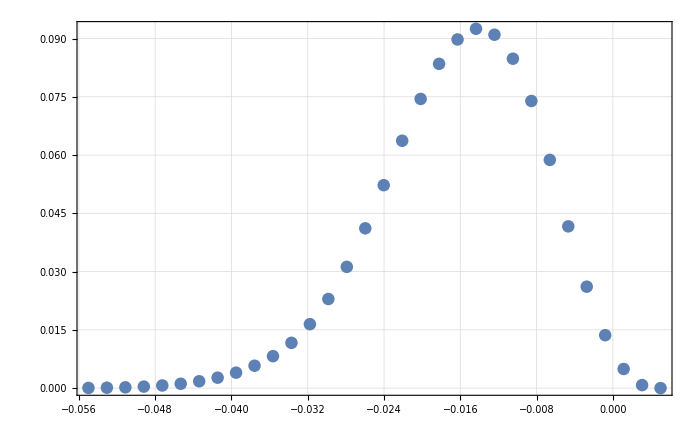

```mathematica
ListPlot[Transpose[{Reverse[XDatam55p05],ILLData90WFilter[[All,2]]}]]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/Electron_ILL90WFilter_Xm55p05_32Bins.txt",Transpose[{Reverse[XDatam55p05],ILLData90WFilter[[All,2]]}],"Table"];
```

fits

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFit=Reap[NonlinearModelFit[
ILLData90WFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 9 Sep 2019 13:15:43

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108189 and 0.00239724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26774 and 0.00318934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10442 and 0.0043809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60258 and 0.00539105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94904 and 0.00583332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10062 and 0.00617211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01614 and 0.00537371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67592 and 0.00520797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751093 and 0.00290106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271388 and 0.0148712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423965 and 0.000119309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108232 and 0.00239825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26822 and 0.00319003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10489 and 0.00432129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60293 and 0.00539155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10052 and 0.00612525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01576 and 0.00538249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67533 and 0.00520711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750806 and 0.0029002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271262 and 0.014867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423723 and 0.000119239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108235 and 0.00239833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26826 and 0.00319008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10492 and 0.00432134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60295 and 0.00539158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9492 and 0.00583351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10051 and 0.00612523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01573 and 0.00538245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67528 and 0.00520704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750784 and 0.00290014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271252 and 0.0148666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423705 and 0.000119233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010823 and 0.0023982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.2682 and 0.00319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10486 and 0.00432126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60291 and 0.00539152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.00583349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10053 and 0.00612526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01578 and 0.00538252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67536 and 0.00520715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.75082 and 0.00290024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271268 and 0.0148672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423735 and 0.000119242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108196 and 0.00239742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26783 and 0.00318947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.1045 and 0.00438101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60264 and 0.00539114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94907 and 0.00583336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.1006 and 0.00617206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01607 and 0.00537362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67582 and 0.00520781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751041 and 0.00290091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271366 and 0.0148704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423921 and 0.000119296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010823 and 0.00239822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26821 and 0.00319001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10487 and 0.00432127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60291 and 0.00539153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10053 and 0.00612526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01577 and 0.00538251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67535 and 0.00520714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750816 and 0.00290023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271266 and 0.0148671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423732 and 0.000119241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010815 and 0.00239633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26731 and 0.00318873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10399 and 0.00438034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60228 and 0.00539061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94892 and 0.00583316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10072 and 0.00622741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01646 and 0.00537416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67645 and 0.00520873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751347 and 0.00290183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271501 and 0.014875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424179 and 0.000119371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108231 and 0.00239824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26822 and 0.00319003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10488 and 0.00432129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60292 and 0.00539154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10052 and 0.00612525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01576 and 0.0053825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67533 and 0.00520712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750808 and 0.00290021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271263 and 0.014867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423725 and 0.000119239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108166 and 0.00239671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26749 and 0.00318899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10417 and 0.00438057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.6024 and 0.00539079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94897 and 0.00583323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10068 and 0.00622731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01633 and 0.00537397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67623 and 0.00520842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271454 and 0.0148734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751242 and 0.00290151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.042409 and 0.000119345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108147 and 0.00239626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26728 and 0.00318868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10395 and 0.0043803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60225 and 0.00539057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94891 and 0.00583315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10073 and 0.00622744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01649 and 0.0053742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67649 and 0.0052088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751369 and 0.00290189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.27151 and 0.0148753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424197 and 0.000119376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108232 and 0.00239825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26822 and 0.00319003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10489 and 0.00432129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60293 and 0.00539155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10052 and 0.00612525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01576 and 0.00538249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67533 and 0.00520711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750806 and 0.0029002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271262 and 0.014867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423723 and 0.000119239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108161 and 0.0023966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26744 and 0.00318891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10412 and 0.00438051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60237 and 0.00539074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94895 and 0.00583321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10069 and 0.00622734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01637 and 0.00537403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67629 and 0.00520851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751273 and 0.0029016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271468 and 0.0148739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424116 and 0.000119352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108198 and 0.00239745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26784 and 0.00318949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10452 and 0.00438103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60265 and 0.00539115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94907 and 0.00583336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.1006 and 0.00617205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01606 and 0.0053736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.6758 and 0.00520779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751033 and 0.00290088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271362 and 0.0148703 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423914 and 0.000119294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108188 and 0.00239723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26774 and 0.00318934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10441 and 0.00438089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60258 and 0.00539105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94904 and 0.00583332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10062 and 0.00617211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01614 and 0.00537371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67593 and 0.00520798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751095 and 0.00290107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271389 and 0.0148712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423966 and 0.000119309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108229 and 0.00239818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26819 and 0.00318998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10485 and 0.00432125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.6029 and 0.00539151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94917 and 0.00583349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10053 and 0.00612527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01578 and 0.00538253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67537 and 0.00520717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750827 and 0.00290026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271271 and 0.0148673 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423741 and 0.000119244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108236 and 0.00239835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26827 and 0.0031901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10494 and 0.00432135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60296 and 0.00539159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9492 and 0.00583352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10051 and 0.00612522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01572 and 0.00538244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67527 and 0.00520702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750778 and 0.00290012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271249 and 0.0148665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423699 and 0.000119232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108191 and 0.00239731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26777 and 0.00318939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10445 and 0.00438094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60261 and 0.00539108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94905 and 0.00583333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10062 and 0.00617209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01611 and 0.00537368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67588 and 0.00520791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751073 and 0.002901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.27138 and 0.0148709 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423948 and 0.000119304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108152 and 0.00239638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26733 and 0.00318876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10401 and 0.00438037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60229 and 0.00539063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94892 and 0.00583317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10072 and 0.0062274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01645 and 0.00537414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67642 and 0.0052087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751335 and 0.00290179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271495 and 0.0148748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424169 and 0.000119368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108212 and 0.00239778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.268 and 0.00318971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10464 and 0.00443237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60277 and 0.00539132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94912 and 0.00583342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10057 and 0.00612538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01594 and 0.00537344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.6756 and 0.00520751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750939 and 0.0029006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271321 and 0.0148689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423835 and 0.000119271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108145 and 0.00239621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26726 and 0.00318865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10393 and 0.00438027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60224 and 0.00539055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9489 and 0.00583314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10073 and 0.00622745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01651 and 0.00537422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67652 and 0.00520884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751381 and 0.00290193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271516 and 0.0148755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424208 and 0.000119379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108219 and 0.00239795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26808 and 0.00318983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10472 and 0.00443247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60282 and 0.0053914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94914 and 0.00583345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10056 and 0.00612533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01588 and 0.00537336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67551 and 0.00520737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750892 and 0.00290046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.2713 and 0.0148682 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423795 and 0.00011926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108177 and 0.00239697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26761 and 0.00318916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10429 and 0.00438073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

9303.862958

### took 43751s or 12h

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
dBFit[[1]]["BestFitParameters"]
```

{b→0.0001}

### rA fit

```mathematica
t0=AbsoluteTime[];
drAFit=Reap[NonlinearModelFit[
ILLData90WFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2,1.,1.,2.,1.+1*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.003<b<0.003
},
{{b,-0.0001}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33501 and 0.00491574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14672 and 0.00554208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03696 and 0.00899823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4589 and 0.0150687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8606 and 0.0156764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0994 and 0.0141473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3593 and 0.0103892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94598 and 0.00516014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06067 and 0.0367192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72814 and 0.0121515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172693 and 0.000385474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33489 and 0.00491544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14658 and 0.00554175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00899792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3597 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94624 and 0.00516032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7283 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.000385516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33419 and 0.00491358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14568 and 0.00553973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03511 and 0.00899599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.015055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1016 and 0.0141504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94788 and 0.00516139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72935 and 0.0121555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06126 and 0.0367315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17282 and 0.000385773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3349 and 0.00491548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14659 and 0.00554179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03673 and 0.00899795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94621 and 0.0051603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72829 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000385512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3332 and 0.00488867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14444 and 0.00543444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03293 and 0.00899873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4546 and 0.0150521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.026995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8637 and 0.0156778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1043 and 0.0141541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3657 and 0.0104267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95016 and 0.00516288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06196 and 0.0367462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73081 and 0.0121602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17297 and 0.00038613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33493 and 0.00491554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03678 and 0.00899802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72825 and 0.0121519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94616 and 0.00516026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06073 and 0.0367204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000385503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33355 and 0.00491188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14487 and 0.00543538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03369 and 0.00899965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8631 and 0.015677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1034 and 0.0141528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3645 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94937 and 0.00516237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73031 and 0.0121586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06172 and 0.0367411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172918 and 0.000386007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33313 and 0.00488849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14436 and 0.00543424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03277 and 0.00899854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8638 and 0.015678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95032 and 0.00516299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06201 and 0.0367472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73091 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172981 and 0.000386155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3335 and 0.00491175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14481 and 0.00543524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03358 and 0.00899952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8632 and 0.0156771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1035 and 0.014153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3647 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94949 and 0.00516244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73038 and 0.0121588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06175 and 0.0367418 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172926 and 0.000386025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14571 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03517 and 0.00899606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72932 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172816 and 0.000385764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33402 and 0.00491312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14547 and 0.00544018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03474 and 0.00900093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1021 and 0.014151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94828 and 0.00516166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72961 and 0.0121563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06138 and 0.0367341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172846 and 0.000385836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33487 and 0.00491539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14655 and 0.00554169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00899786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3598 and 0.0103894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94629 and 0.00516035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72834 and 0.0121521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172714 and 0.000385524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00491459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14617 and 0.00554083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03598 and 0.00899704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4579 and 0.0150675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1006 and 0.0141489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3608 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94699 and 0.00516081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72878 and 0.0121536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06098 and 0.0367258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17276 and 0.000385633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33325 and 0.00488881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14451 and 0.00543459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03305 and 0.00899887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4547 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8636 and 0.0156777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1042 and 0.0141539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3655 and 0.0104266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95003 and 0.0051628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73073 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06192 and 0.0367454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172962 and 0.00038611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14431 and 0.00543414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.000386169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33376 and 0.00491244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00543597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03416 and 0.00900023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1028 and 0.014152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94888 and 0.00516205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72999 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06157 and 0.036738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172886 and 0.00038593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00491371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14574 and 0.00553987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03522 and 0.00899612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94777 and 0.00516132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172812 and 0.000385755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33367 and 0.0049122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14502 and 0.00543572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03396 and 0.00899998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.027128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0157297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1031 and 0.0141523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3641 and 0.010426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94909 and 0.00516219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73013 and 0.012158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06163 and 0.0367393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1729 and 0.000385963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00491393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14585 and 0.00554011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03541 and 0.00899635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00516119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72916 and 0.0121548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06117 and 0.0367295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000385725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33381 and 0.00491257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14521 and 0.0054396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00900036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1027 and 0.0141518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94877 and 0.00516197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72992 and 0.0121573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06153 and 0.0367372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172878 and 0.000385912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1443 and 0.00543413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.00038617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33311 and 0.00488845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14433 and 0.0054342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03273 and 0.00899849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95036 and 0.00516301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73094 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06202 and 0.0367474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172984 and 0.000386161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06107 and 0.0367276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14572 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03518 and 0.00899607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172815 and 0.000385763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00491389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14583 and 0.00554007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.00899631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94761 and 0.00516122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72918 and 0.0121549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0367298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172802 and 0.000385731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33374 and 0.00491238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14511 and 0.00543591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03411 and 0.00900017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94893 and 0.00516208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73003 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.000385938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33386 and 0.0049127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14527 and 0.00543973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03438 and 0.0090005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.0051619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72985 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172871 and 0.000385894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3347 and 0.00491492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14633 and 0.00554119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03626 and 0.00899738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8611 and 0.0156772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1002 and 0.0141484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3604 and 0.0103897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9467 and 0.00516062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7286 and 0.012153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06089 and 0.0367239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172741 and 0.000385588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33434 and 0.00491399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14588 and 0.00554018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03546 and 0.00899641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.015728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1012 and 0.0141498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94752 and 0.00516116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72912 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06115 and 0.0367292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172796 and 0.000385717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06108 and 0.0367277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.00491373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14575 and 0.0055399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03524 and 0.00899615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8619 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94775 and 0.0051613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172811 and 0.000385752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33416 and 0.0049135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14564 and 0.00553965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03505 and 0.00899591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3623 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94795 and 0.00516144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7294 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06128 and 0.0367319 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172824 and 0.000385783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33415 and 0.00491347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14563 and 0.00553962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03502 and 0.00899588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94797 and 0.00516145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72941 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172826 and 0.000385788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00491268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14526 and 0.00543971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03436 and 0.00900047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94867 and 0.00516191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72986 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172872 and 0.000385897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00491294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14538 and 0.00543999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.0150543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.015729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1023 and 0.0141513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3631 and 0.0104255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94844 and 0.00516176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72971 and 0.0121566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06143 and 0.0367351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172857 and 0.000385861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0049134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1456 and 0.00544047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03496 and 0.0089958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1018 and 0.0141506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3625 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94804 and 0.0051615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72946 and 0.0121558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0367325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17283 and 0.000385798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33451 and 0.00491442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14609 and 0.00554064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03583 and 0.00899686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1007 and 0.0141492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94714 and 0.00516091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06103 and 0.0367267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17277 and 0.000385657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33409 and 0.00491331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14556 and 0.00544038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03488 and 0.00899571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4567 and 0.0150547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1019 and 0.0141507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94812 and 0.00516155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7295 and 0.012156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172835 and 0.00038581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.0049132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03478 and 0.00899559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94822 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72957 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172842 and 0.000385826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.0049128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14532 and 0.00543984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03447 and 0.0090006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94857 and 0.00516184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72979 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172865 and 0.000385881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33388 and 0.00491276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1453 and 0.0054398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00900056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9486 and 0.00516186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72981 and 0.012157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06148 and 0.0367361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172867 and 0.000385885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00491324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14553 and 0.00544031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03483 and 0.00899564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94818 and 0.00516158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72954 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06135 and 0.0367334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172839 and 0.000385819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00491282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14533 and 0.00543986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03448 and 0.00900062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94855 and 0.00516183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72978 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172864 and 0.000385878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

22516.43869

### took 22516 s or 6,25h

```mathematica
drAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0000750132 | 0.0000470927 | 1.59288 | 0.121333

### Alpha Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dAlphaFit=Reap[NonlinearModelFit[
ILLData90WFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->5,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 00:27:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33444 and 0.00487253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.0089724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94748 and 0.00531564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0609 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33509 and 0.00487425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14676 and 0.00545655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03685 and 0.0089742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.015018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8601 and 0.0154271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3591 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94593 and 0.00514742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72811 and 0.0121574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06043 and 0.0367862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172697 and 0.000375918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14666 and 0.00545633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03668 and 0.00897399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94611 and 0.00514754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72822 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06049 and 0.0367874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000375945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33455 and 0.00487282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14606 and 0.00545501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03562 and 0.0089727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94719 and 0.00514047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14667 and 0.00545636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00897401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94609 and 0.00514753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72821 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06048 and 0.0367872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172708 and 0.000375942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00487111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14523 and 0.00545319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03419 and 0.00896316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4555 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94874 and 0.00531653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72989 and 0.0121632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0368042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172882 and 0.000376344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33504 and 0.00487412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14669 and 0.0054564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03674 and 0.00897405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94605 and 0.0051475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72819 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.036787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0048717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14552 and 0.00545382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03466 and 0.00897153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8618 and 0.0154293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00531616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0368008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172847 and 0.000376264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14517 and 0.00545306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03409 and 0.00896304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72996 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94884 and 0.00531661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.0368049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.00037636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00487153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14543 and 0.00545363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03451 and 0.00897135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8619 and 0.0154294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94837 and 0.00531627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0368018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172858 and 0.000376287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00487287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14609 and 0.00545506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03566 and 0.00897275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.361 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94715 and 0.00514044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000376106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03536 and 0.00897239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94749 and 0.00531565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.335 and 0.00487402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14664 and 0.00545629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00897395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4581 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8603 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00514756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0605 and 0.0367876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.00037595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33482 and 0.00487353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14641 and 0.00545577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03623 and 0.00897344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0271078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8606 and 0.0154277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3601 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94658 and 0.00514784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06063 and 0.0367904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72852 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000376017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33393 and 0.0048712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00487092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00545299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03403 and 0.00896297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9489 and 0.00531665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0368053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73 and 0.0121636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172893 and 0.000376369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00487202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14567 and 0.00545416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03493 and 0.00897186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8616 and 0.015429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94793 and 0.00531596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.036799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172829 and 0.000376221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.004873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14615 and 0.0054552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03577 and 0.00897288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8609 and 0.0154282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3608 and 0.010448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94704 and 0.00514037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06078 and 0.0367934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172771 and 0.000376089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03606 and 0.00897324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3603 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94675 and 0.00514795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72863 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06068 and 0.0367915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172751 and 0.000376043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14516 and 0.00545304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03407 and 0.00896302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94886 and 0.00531662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17289 and 0.000376363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14537 and 0.00545349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00896346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.010449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00531635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72973 and 0.0121627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06121 and 0.0368026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172866 and 0.000376306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00487219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14575 and 0.00545434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03508 and 0.00897204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94778 and 0.00531586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.061 and 0.036798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000376198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14591 and 0.00545468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.00897237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9475 and 0.00531566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7291 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1728 and 0.000376155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33458 and 0.0048729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1461 and 0.0054551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00897278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3609 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94713 and 0.00514043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.036794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172777 and 0.000376102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00487104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1452 and 0.00545311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03413 and 0.00896309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9488 and 0.00531658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72994 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0368046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172887 and 0.000376354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33394 and 0.00487121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33454 and 0.00487279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14605 and 0.00545499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0356 and 0.00897267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94722 and 0.00514049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72894 and 0.0121601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06083 and 0.0367946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000376116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03605 and 0.00897322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3604 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94676 and 0.00514796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06069 and 0.0367916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172752 and 0.000376045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00487222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14577 and 0.00545437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0351 and 0.00897207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.027109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94776 and 0.00531584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172817 and 0.000376194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

13770.33362

### took 13770s or 3,8h

```mathematica
dAlphaFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000916626 | 0.0000928275 | 9.87451 | 4.32917×10^-11

```mathematica
dAlphaFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

18.3325

# 180° no filter

Data 180° no Filter

```mathematica
XDatam85p05=XDataCreation[{-0.085,0.005,0.},32]
```

{-0.085,-0.0820968,-0.0791935,-0.0762903,-0.0733871,-0.0704839,-0.0675806,-0.0646774,-0.0617742,-0.058871,-0.0559677,-0.0530645,-0.0501613,-0.0472581,-0.0443548,-0.0414516,-0.0385484,-0.0356452,-0.0327419,-0.0298387,-0.0269355,-0.0240323,-0.021129,-0.0182258,-0.0153226,-0.0124194,-0.00951613,-0.0066129,-0.00370968,-0.000806452,0.00209677,0.005}

```mathematica
t0=AbsoluteTime[];
ILLData180noFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam85p05,3]},{bin,1,Length[XDatam85p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15781 and 0.00348409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14876 and 0.00971364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50206 and 0.00832328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03134 and 0.00891677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43525 and 0.00404331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198118 and 0.000214276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289792 and 0.0000757957 for the integral and error estimates.

438.364107

### 438s

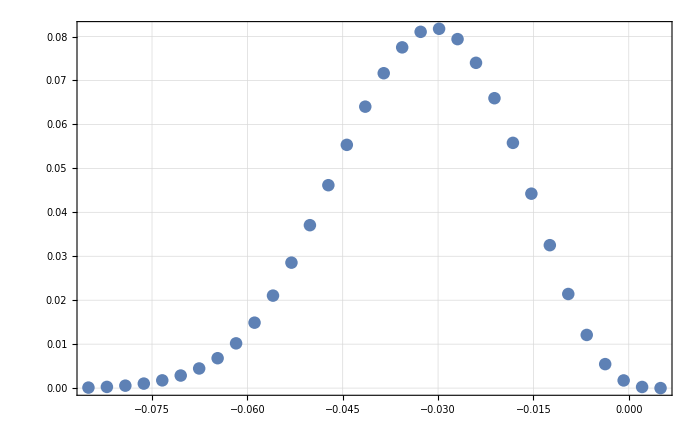

```mathematica
ListPlot[Transpose[{Reverse[XDatam85p05],ILLData180noFilter[[All,2]]}]]
```

```mathematica
(*Export["~/Dropbox/PhD/ElectronTransportSpectrum.txt",Transpose[{Reverse[XDatam55p05],ILLData90noFilter[[All,2]]}],"Table"]*)
```

~/Dropbox/PhD/ElectronTransportSpectrum.txt

Fits

### drRxB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drRxBFit=Reap[NonlinearModelFit[
ILLData180noFilter,
{
FitFuncBinNormArith[bin,{b,Pi,0.2,1./2+1/2.*10^-4,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam85p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Tue 29 Oct 2019 18:10:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15821 and 0.00349626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14899 and 0.00972169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5001 and 0.00832466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02944 and 0.00890401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43404 and 0.00407084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197998 and 0.000219606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289656 and 0.0000773233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15824 and 0.00349636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14907 and 0.00972178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.49999 and 0.00832458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02931 and 0.00890395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43395 and 0.00407073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197989 and 0.000219596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289642 and 0.0000773197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15819 and 0.00349619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14894 and 0.00972163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50017 and 0.00832472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02952 and 0.00890405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43409 and 0.00407091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198003 and 0.000219613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289665 and 0.0000773257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1579 and 0.00349514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14811 and 0.00972075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50128 and 0.00832559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03081 and 0.00890466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43497 and 0.00407203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198096 and 0.000219714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289805 and 0.0000773629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1582 and 0.00349621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14895 and 0.00972165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50015 and 0.0083247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.0295 and 0.00890404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43408 and 0.00407089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198002 and 0.000219611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289662 and 0.000077325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1575 and 0.00349367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14697 and 0.00971952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50282 and 0.00832679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03261 and 0.00890551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43618 and 0.00407358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198223 and 0.000219854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289999 and 0.0000774145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15821 and 0.00349625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14898 and 0.00972168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50011 and 0.00832467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02945 and 0.00890402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43405 and 0.00407086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197999 and 0.000219607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289657 and 0.0000773237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15764 and 0.00349418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14737 and 0.00971994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50229 and 0.00832637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03199 and 0.00890522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43577 and 0.00407305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198179 and 0.000219805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289932 and 0.0000773967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15747 and 0.00349357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14689 and 0.00971943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50293 and 0.00832687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03274 and 0.00890557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43627 and 0.00407369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198232 and 0.000219863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0290012 and 0.0000774182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15821 and 0.00349626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14899 and 0.00972169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5001 and 0.00832466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02944 and 0.00890401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43404 and 0.00407084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197998 and 0.000219606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289656 and 0.0000773233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1576 and 0.00349403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14725 and 0.00971982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50245 and 0.0083265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03217 and 0.0089053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43589 and 0.0040732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198192 and 0.000219819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289951 and 0.0000774019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15791 and 0.00349518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14815 and 0.00972078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50124 and 0.00832555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03077 and 0.00890464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43494 and 0.00407199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198092 and 0.00021971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289799 and 0.0000773615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14791 and 0.00972053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50155 and 0.0083258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03113 and 0.00890481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43518 and 0.0040723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198118 and 0.000219738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289839 and 0.000077372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15818 and 0.00349616 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14891 and 0.00972161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5002 and 0.00832475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02956 and 0.00890407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43412 and 0.00407095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198006 and 0.000219616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289669 and 0.0000773268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15807 and 0.00349574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14859 and 0.00972125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50064 and 0.00832509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03007 and 0.00890431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43447 and 0.00407139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198043 and 0.000219656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289725 and 0.0000773416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15752 and 0.00349375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14703 and 0.00971959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50274 and 0.00832672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03251 and 0.00890546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43612 and 0.0040735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198216 and 0.000219846 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289988 and 0.0000774117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15745 and 0.00349351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14685 and 0.00971938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50299 and 0.00832692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03281 and 0.0089056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43632 and 0.00407375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198237 and 0.000219869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.029002 and 0.0000774202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15771 and 0.00349445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14758 and 0.00972017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50201 and 0.00832615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03166 and 0.00890506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43554 and 0.00407276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198156 and 0.000219779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289896 and 0.0000773871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15794 and 0.00349529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14823 and 0.00972087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50112 and 0.00832546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03063 and 0.00890457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43485 and 0.00407187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198083 and 0.000219699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289785 and 0.0000773577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15769 and 0.00349436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14751 and 0.00972009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5021 and 0.00832623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03177 and 0.00890511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43562 and 0.00407286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198164 and 0.000219788 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289908 and 0.0000773904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15792 and 0.00349519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14816 and 0.00972079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50122 and 0.00832554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03075 and 0.00890463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43492 and 0.00407197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198091 and 0.000219708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289797 and 0.0000773609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15776 and 0.00349462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14771 and 0.00972031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50183 and 0.00832601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03145 and 0.00890496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4354 and 0.00407258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198141 and 0.000219763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289874 and 0.0000773813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15745 and 0.00349351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14684 and 0.00971938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.503 and 0.00832692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03281 and 0.00890561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43632 and 0.00407376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198238 and 0.000219869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.029002 and 0.0000774203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15746 and 0.00349354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14687 and 0.00971941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50296 and 0.00832689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03277 and 0.00890558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43629 and 0.00407372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198234 and 0.000219866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0290016 and 0.0000774191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15801 and 0.00349554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14843 and 0.00972109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50086 and 0.00832526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03032 and 0.00890443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43464 and 0.00407161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.19806 and 0.000219675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289751 and 0.0000773487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15787 and 0.00349504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14804 and 0.00972067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50138 and 0.00832567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03094 and 0.00890472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43505 and 0.00407214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198104 and 0.000219723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289818 and 0.0000773664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15797 and 0.00349537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.1483 and 0.00972095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50103 and 0.00832539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03053 and 0.00890452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43477 and 0.00407178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198075 and 0.000219691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289773 and 0.0000773546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15771 and 0.00349446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14759 and 0.00972018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50199 and 0.00832614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03164 and 0.00890505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43553 and 0.00407275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198155 and 0.000219778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289894 and 0.0000773867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15787 and 0.00349503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14803 and 0.00972066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5014 and 0.00832568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03095 and 0.00890472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43506 and 0.00407215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198105 and 0.000219724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289819 and 0.0000773667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1578 and 0.00349476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14782 and 0.00972043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50167 and 0.00832589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03127 and 0.00890488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43528 and 0.00407243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198128 and 0.000219749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289854 and 0.0000773761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15787 and 0.00349504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14804 and 0.00972066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50138 and 0.00832567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03094 and 0.00890472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43505 and 0.00407214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198104 and 0.000219723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289818 and 0.0000773664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1581 and 0.00349586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14868 and 0.00972135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50052 and 0.00832499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02993 and 0.00890424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43437 and 0.00407127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198032 and 0.000219645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289709 and 0.0000773374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15797 and 0.0034954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14832 and 0.00972097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50101 and 0.00832537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03049 and 0.00890451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43475 and 0.00407175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198073 and 0.000219689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.028977 and 0.0000773537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15796 and 0.00349535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14828 and 0.00972093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.